```mathematica
ToVars3[g_]:=Block[{exp,sep,vertex, vertices,var,var1, var2,  edges, edgeIndex, edge},
(* works only for graphs in which 1,2 and 3 are connected *)
sep="";
exp="";
vertices=VertexList[g];
For[vertex=1,vertex<=Length[vertices], vertex++,
var ="x" <> ToString[ vertices[[vertex]] ];
exp= exp<>sep<> "Element["<>var<>", Integers]";
sep=" && " 
];

For[vertex=1,vertex<=Length[vertices], vertex++,
var ="x" <> ToString[ vertices[[vertex]] ];
exp= exp<>sep<> "(1<="<>var<>" <=4)";
sep=" && " 
];

edges=EdgeList[g];

exp= exp<>sep<> "x1 == 1 && x2== 2 && x3==3";
sep=" && " ;

For[edgeIndex=1,edgeIndex≤Length[edges],edgeIndex++,
edge=edges[[edgeIndex]];
var1 ="x" <> ToString[ edge[[1]] ];
var2 ="x" <> ToString[ edge[[2]] ];
exp= exp<>sep<> var1<>"!="<>var2;
sep=" && " 
];
(*
exp=exp <> ", {";
sep="";
For[vertex=1,vertex<=Length[vertices], vertex++,
var ="x" <> ToString[ vertices[[vertex]] ];
exp= exp<>sep<> var;
sep=", " 
];
exp=exp <> "}";*)
Print[exp];
Return[Read[StringToStream[ exp],Expression]]
]
```

```mathematica
constrFull=ToVars3[expMixedBisWithHair]
```

Element[x1, Integers] && Element[x2, Integers] && Element[x3, Integers] && Element[x4, Integers] && Element[x5, Integers] && Element[x6, Integers] && Element[x16, Integers] && Element[x11, Integers] && Element[x7, Integers] && Element[x17, Integers] && Element[x12, Integers] && Element[x8, Integers] && Element[x18, Integers] && Element[x13, Integers] && Element[x9, Integers] && Element[x19, Integers] && Element[x14, Integers] && Element[x10, Integers] && Element[x20, Integers] && Element[x15, Integers] && (1<=x1 <=4) && (1<=x2 <=4) && (1<=x3 <=4) && (1<=x4 <=4) && (1<=x5 <=4) && (1<=x6 <=4) && (1<=x16 <=4) && (1<=x11 <=4) && (1<=x7 <=4) && (1<=x17 <=4) && (1<=x12 <=4) && (1<=x8 <=4) && (1<=x18 <=4) && (1<=x13 <=4) && (1<=x9 <=4) && (1<=x19 <=4) && (1<=x14 <=4) && (1<=x10 <=4) && (1<=x20 <=4) && (1<=x15 <=4) && x1 == 1 && x2== 2 && x3==3 && x1!=x2 && x1!=x5 && x1!=x6 && x1!=x11 && x1!=x15 && x2!=x3 && x2!=x11 && x2!=x7 && x2!=x12 && x3!=x4 && x3!=x12 && x3!=x8 && x3!=x13 && x4!=x5 && x4!=x13 && x4!=x9 && x4!=x14 && x5!=x14 && x5!=x10 && x5!=x15 && x6!=x16 && x6!=x11 && x6!=x15 && x11!=x7 && x7!=x17 && x7!=x12 && x12!=x8 && x8!=x18 && x8!=x13 && x13!=x9 && x9!=x19 && x9!=x14 && x14!=x10 && x10!=x20 && x10!=x15

x1∈Integers&&x2∈Integers&&x3∈Integers&&x4∈Integers&&x5∈Integers&&x6∈Integers&&x16∈Integers&&x11∈Integers&&x7∈Integers&&x17∈Integers&&x12∈Integers&&x8∈Integers&&x18∈Integers&&x13∈Integers&&x9∈Integers&&x19∈Integers&&x14∈Integers&&x10∈Integers&&x20∈Integers&&x15∈Integers&&1≤x1≤4&&1≤x2≤4&&1≤x3≤4&&1≤x4≤4&&1≤x5≤4&&1≤x6≤4&&1≤x16≤4&&1≤x11≤4&&1≤x7≤4&&1≤x17≤4&&1≤x12≤4&&1≤x8≤4&&1≤x18≤4&&1≤x13≤4&&1≤x9≤4&&1≤x19≤4&&1≤x14≤4&&1≤x10≤4&&1≤x20≤4&&1≤x15≤4&&x1==1&&x2==2&&x3==3&&x1≠x2&&x1≠x5&&x1≠x6&&x1≠x11&&x1≠x15&&x2≠x3&&x2≠x11&&x2≠x7&&x2≠x12&&x3≠x4&&x3≠x12&&x3≠x8&&x3≠x13&&x4≠x5&&x4≠x13&&x4≠x9&&x4≠x14&&x5≠x14&&x5≠x10&&x5≠x15&&x6≠x16&&x6≠x11&&x6≠x15&&x11≠x7&&x7≠x17&&x7≠x12&&x12≠x8&&x8≠x18&&x8≠x13&&x13≠x9&&x9≠x19&&x9≠x14&&x14≠x10&&x10≠x20&&x10≠x15

```mathematica
Solve
```

```mathematica
NumberToConstraint7[val_, vertices_]:=Block[
{n=IntegerDigits[val,4,Length[vertices]],res, sep=""},
res=Fold[And,Table[Symbol["x"<>ToString[vertices[[i]]]]==n[[i]]+1,{i,1,Length[vertices]}]];
res]
```

```mathematica
hasDoubles=FullSimplify[Fold[Or,
Table[Symbol["x"<>ToString[i]]==Symbol["x"<>ToString[Mod[i+1,5]+1]] &&
Symbol["x"<>ToString[Mod[i+1,5]+1]]==Symbol["x"<>ToString[Mod[i+2,5]+1]] &&
Symbol["x"<>ToString[i]]!=Symbol["x"<>ToString[Mod[i+3,5]+1]] &&
Symbol["x"<>ToString[Mod[i,5]+1]]==Symbol["x"<>ToString[Mod[i+3,5]+1]],{i,1,5}]
]]
```

(x1==x4&&((x1==x2&&x3==x5&&x3≠x4)||(x2==x3&&x2==x5&&x4≠x5)))||(x1==x3&&((x2==x4&&x4==x5&&x1≠x2)||(x2==x5&&x3==x4&&x1≠x5)))||(x1==x5&&x2≠x3&&x2==x4&&x3==x5)

```mathematica
constrEdge1=Simplify[ToVars3[EdgeAdd[expMixedBisWithHair,{1<->3,1<->4}]]]
```

Element[x1, Integers] && Element[x2, Integers] && Element[x3, Integers] && Element[x4, Integers] && Element[x5, Integers] && Element[x6, Integers] && Element[x16, Integers] && Element[x11, Integers] && Element[x7, Integers] && Element[x17, Integers] && Element[x12, Integers] && Element[x8, Integers] && Element[x18, Integers] && Element[x13, Integers] && Element[x9, Integers] && Element[x19, Integers] && Element[x14, Integers] && Element[x10, Integers] && Element[x20, Integers] && Element[x15, Integers] && (1<=x1 <=4) && (1<=x2 <=4) && (1<=x3 <=4) && (1<=x4 <=4) && (1<=x5 <=4) && (1<=x6 <=4) && (1<=x16 <=4) && (1<=x11 <=4) && (1<=x7 <=4) && (1<=x17 <=4) && (1<=x12 <=4) && (1<=x8 <=4) && (1<=x18 <=4) && (1<=x13 <=4) && (1<=x9 <=4) && (1<=x19 <=4) && (1<=x14 <=4) && (1<=x10 <=4) && (1<=x20 <=4) && (1<=x15 <=4) && x1 == 1 && x2== 2 && x3==3 && x1!=x2 && x1!=x5 && x1!=x6 && x1!=x11 && x1!=x15 && x1!=x3 && x1!=x4 && x2!=x3 && x2!=x11 && x2!=x7 && x2!=x12 && x3!=x4 && x3!=x12 && x3!=x8 && x3!=x13 && x4!=x5 && x4!=x13 && x4!=x9 && x4!=x14 && x5!=x14 && x5!=x10 && x5!=x15 && x6!=x16 && x6!=x11 && x6!=x15 && x11!=x7 && x7!=x17 && x7!=x12 && x12!=x8 && x8!=x18 && x8!=x13 && x13!=x9 && x9!=x19 && x9!=x14 && x14!=x10 && x10!=x20 && x10!=x15

x1∈Integers&&x2∈Integers&&x3∈Integers&&x4∈Integers&&x5∈Integers&&x6∈Integers&&x16∈Integers&&x11∈Integers&&x7∈Integers&&x17∈Integers&&x12∈Integers&&x8∈Integers&&x18∈Integers&&x13∈Integers&&x9∈Integers&&x19∈Integers&&x14∈Integers&&x10∈Integers&&x20∈Integers&&x15∈Integers&&1≤x1≤4&&1≤x2≤4&&1≤x3≤4&&1≤x4≤4&&1≤x5≤4&&1≤x6≤4&&1≤x16≤4&&1≤x11≤4&&1≤x7≤4&&1≤x17≤4&&1≤x12≤4&&1≤x8≤4&&1≤x18≤4&&1≤x13≤4&&1≤x9≤4&&1≤x19≤4&&1≤x14≤4&&1≤x10≤4&&1≤x20≤4&&1≤x15≤4&&x1==1&&x2==2&&x3==3&&x1≠x2&&x1≠x5&&x1≠x6&&x1≠x11&&x1≠x15&&x1≠x3&&x1≠x4&&x2≠x3&&x11≠x2&&x2≠x7&&x12≠x2&&x3≠x4&&x12≠x3&&x3≠x8&&x13≠x3&&x4≠x5&&x13≠x4&&x4≠x9&&x14≠x4&&x14≠x5&&x10≠x5&&x15≠x5&&x16≠x6&&x11≠x6&&x15≠x6&&x11≠x7&&x17≠x7&&x12≠x7&&x12≠x8&&x18≠x8&&x13≠x8&&x13≠x9&&x19≠x9&&x14≠x9&&x10≠x14&&x10≠x20&&x10≠x15

```mathematica
constrEdge2=Simplify[ToVars3[EdgeAdd[expMixedBisWithHair,{2<->4,2<->5}]]]
```

Element[x1, Integers] && Element[x2, Integers] && Element[x3, Integers] && Element[x4, Integers] && Element[x5, Integers] && Element[x6, Integers] && Element[x16, Integers] && Element[x11, Integers] && Element[x7, Integers] && Element[x17, Integers] && Element[x12, Integers] && Element[x8, Integers] && Element[x18, Integers] && Element[x13, Integers] && Element[x9, Integers] && Element[x19, Integers] && Element[x14, Integers] && Element[x10, Integers] && Element[x20, Integers] && Element[x15, Integers] && (1<=x1 <=4) && (1<=x2 <=4) && (1<=x3 <=4) && (1<=x4 <=4) && (1<=x5 <=4) && (1<=x6 <=4) && (1<=x16 <=4) && (1<=x11 <=4) && (1<=x7 <=4) && (1<=x17 <=4) && (1<=x12 <=4) && (1<=x8 <=4) && (1<=x18 <=4) && (1<=x13 <=4) && (1<=x9 <=4) && (1<=x19 <=4) && (1<=x14 <=4) && (1<=x10 <=4) && (1<=x20 <=4) && (1<=x15 <=4) && x1 == 1 && x2== 2 && x3==3 && x1!=x2 && x1!=x5 && x1!=x6 && x1!=x11 && x1!=x15 && x2!=x3 && x2!=x11 && x2!=x7 && x2!=x12 && x2!=x4 && x2!=x5 && x3!=x4 && x3!=x12 && x3!=x8 && x3!=x13 && x4!=x5 && x4!=x13 && x4!=x9 && x4!=x14 && x5!=x14 && x5!=x10 && x5!=x15 && x6!=x16 && x6!=x11 && x6!=x15 && x11!=x7 && x7!=x17 && x7!=x12 && x12!=x8 && x8!=x18 && x8!=x13 && x13!=x9 && x9!=x19 && x9!=x14 && x14!=x10 && x10!=x20 && x10!=x15

x1∈Integers&&x2∈Integers&&x3∈Integers&&x4∈Integers&&x5∈Integers&&x6∈Integers&&x16∈Integers&&x11∈Integers&&x7∈Integers&&x17∈Integers&&x12∈Integers&&x8∈Integers&&x18∈Integers&&x13∈Integers&&x9∈Integers&&x19∈Integers&&x14∈Integers&&x10∈Integers&&x20∈Integers&&x15∈Integers&&1≤x1≤4&&1≤x2≤4&&1≤x3≤4&&1≤x4≤4&&1≤x5≤4&&1≤x6≤4&&1≤x16≤4&&1≤x11≤4&&1≤x7≤4&&1≤x17≤4&&1≤x12≤4&&1≤x8≤4&&1≤x18≤4&&1≤x13≤4&&1≤x9≤4&&1≤x19≤4&&1≤x14≤4&&1≤x10≤4&&1≤x20≤4&&1≤x15≤4&&x1==1&&x2==2&&x3==3&&x1≠x2&&x1≠x5&&x1≠x6&&x1≠x11&&x1≠x15&&x2≠x3&&x11≠x2&&x2≠x7&&x12≠x2&&x2≠x4&&x2≠x5&&x3≠x4&&x12≠x3&&x3≠x8&&x13≠x3&&x4≠x5&&x13≠x4&&x4≠x9&&x14≠x4&&x14≠x5&&x10≠x5&&x15≠x5&&x16≠x6&&x11≠x6&&x15≠x6&&x11≠x7&&x17≠x7&&x12≠x7&&x12≠x8&&x18≠x8&&x13≠x8&&x13≠x9&&x19≠x9&&x14≠x9&&x10≠x14&&x10≠x20&&x10≠x15

```mathematica
constrEdge3=Simplify[ToVars3[EdgeAdd[expMixedBisWithHair,{3<->5}]]]
```

Element[x1, Integers] && Element[x2, Integers] && Element[x3, Integers] && Element[x4, Integers] && Element[x5, Integers] && Element[x6, Integers] && Element[x16, Integers] && Element[x11, Integers] && Element[x7, Integers] && Element[x17, Integers] && Element[x12, Integers] && Element[x8, Integers] && Element[x18, Integers] && Element[x13, Integers] && Element[x9, Integers] && Element[x19, Integers] && Element[x14, Integers] && Element[x10, Integers] && Element[x20, Integers] && Element[x15, Integers] && (1<=x1 <=4) && (1<=x2 <=4) && (1<=x3 <=4) && (1<=x4 <=4) && (1<=x5 <=4) && (1<=x6 <=4) && (1<=x16 <=4) && (1<=x11 <=4) && (1<=x7 <=4) && (1<=x17 <=4) && (1<=x12 <=4) && (1<=x8 <=4) && (1<=x18 <=4) && (1<=x13 <=4) && (1<=x9 <=4) && (1<=x19 <=4) && (1<=x14 <=4) && (1<=x10 <=4) && (1<=x20 <=4) && (1<=x15 <=4) && x1 == 1 && x2== 2 && x3==3 && x1!=x2 && x1!=x5 && x1!=x6 && x1!=x11 && x1!=x15 && x2!=x3 && x2!=x11 && x2!=x7 && x2!=x12 && x3!=x4 && x3!=x12 && x3!=x8 && x3!=x13 && x3!=x5 && x4!=x5 && x4!=x13 && x4!=x9 && x4!=x14 && x5!=x14 && x5!=x10 && x5!=x15 && x6!=x16 && x6!=x11 && x6!=x15 && x11!=x7 && x7!=x17 && x7!=x12 && x12!=x8 && x8!=x18 && x8!=x13 && x13!=x9 && x9!=x19 && x9!=x14 && x14!=x10 && x10!=x20 && x10!=x15

x1∈Integers&&x2∈Integers&&x3∈Integers&&x4∈Integers&&x5∈Integers&&x6∈Integers&&x16∈Integers&&x11∈Integers&&x7∈Integers&&x17∈Integers&&x12∈Integers&&x8∈Integers&&x18∈Integers&&x13∈Integers&&x9∈Integers&&x19∈Integers&&x14∈Integers&&x10∈Integers&&x20∈Integers&&x15∈Integers&&1≤x1≤4&&1≤x2≤4&&1≤x3≤4&&1≤x4≤4&&1≤x5≤4&&1≤x6≤4&&1≤x16≤4&&1≤x11≤4&&1≤x7≤4&&1≤x17≤4&&1≤x12≤4&&1≤x8≤4&&1≤x18≤4&&1≤x13≤4&&1≤x9≤4&&1≤x19≤4&&1≤x14≤4&&1≤x10≤4&&1≤x20≤4&&1≤x15≤4&&x1==1&&x2==2&&x3==3&&x1≠x2&&x1≠x5&&x1≠x6&&x1≠x11&&x1≠x15&&x2≠x3&&x11≠x2&&x2≠x7&&x12≠x2&&x3≠x4&&x12≠x3&&x3≠x8&&x13≠x3&&x3≠x5&&x4≠x5&&x13≠x4&&x4≠x9&&x14≠x4&&x14≠x5&&x10≠x5&&x15≠x5&&x16≠x6&&x11≠x6&&x15≠x6&&x11≠x7&&x17≠x7&&x12≠x7&&x12≠x8&&x18≠x8&&x13≠x8&&x13≠x9&&x19≠x9&&x14≠x9&&x10≠x14&&x10≠x20&&x10≠x15

```mathematica
Clear[constrFull]
```

```mathematica
CountSolutions7[n_,constr_]:=Block[{ass, per,i,sols,result2,keys, other, temp, result3},
ass=Association[];
sols=Solve[constrFull&&(constr),{x1,x2,x3,x4,x5,x6,x7,x8,x9,x10,x11,x12,x13,x14,x15,x16,x17,x18,x19,x20}];
per=Map[Map[Last[#]&,#]&,sols];
For[i=1,i<=Length[per],i++,
ass[per[[i]]]={}
];
sols=Solve[constrEdge1&&(constr),{x1,x2,x3,x4,x5,x6,x7,x8,x9,x10,x11,x12,x13,x14,x15,x16,x17,x18,x19,x20}];
per=Map[Map[Last[#]&,#]&,sols];
For[i=1,i<=Length[per],i++,
ass[per[[i]]]=Append[ass[per[[i]]],1]
];
sols=Solve[constrEdge2&&(constr),{x1,x2,x3,x4,x5,x6,x7,x8,x9,x10,x11,x12,x13,x14,x15,x16,x17,x18,x19,x20}];
per=Map[Map[Last[#]&,#]&,sols];
For[i=1,i<=Length[per],i++,
ass[per[[i]]]=Append[ass[per[[i]]],2]
];
sols=Solve[constrEdge3&&(constr),{x1,x2,x3,x4,x5,x6,x7,x8,x9,x10,x11,x12,x13,x14,x15,x16,x17,x18,x19,x20}];
per=Map[Map[Last[#]&,#]&,sols];
For[i=1,i<=Length[per],i++,
ass[per[[i]]]=Append[ass[per[[i]]],3]
];
result2={};
keys=Keys[ass];
For[i=1,i≤Length[keys],i++,
AppendTo[result2,ass[keys[[i]]]]
];
temp=Sort[Tally[result2]];
result3={};
AppendTo[result3,Map[#[[2]]&,Select[temp,#[[1]]=={1}&]]];
AppendTo[result3,Map[#[[2]]&,Select[temp,#[[1]]=={2}&]]];
AppendTo[result3,Map[#[[2]]&,Select[temp,#[[1]]=={3}&]]];
AppendTo[result3,Map[#[[2]]&,Select[temp,#[[1]]=={1,2}&]]];
AppendTo[result3,Map[#[[2]]&,Select[temp,#[[1]]=={2,3}&]]];
AppendTo[result3,Map[#[[2]]&,Select[temp,#[[1]]=={1,3}&]]];
AppendTo[result3,Map[#[[2]]&,Select[temp,#[[1]]=={1,2,3}&]]];
result3=Map[If[#=={},0,First[#]]&,result3];
Print[{ n,IntegerDigits[n,4,10]+1,result3}];
{ n,IntegerDigits[n,4,10]+1,result3}
]
```

```mathematica
DistributeDefinitions[NumberToConstraint7,constrFull,constrEdge1, constrEdge2, constrEdge3,CountSolutions7]
```

{CountSolutions7}

```mathematica
AbsoluteTiming[
TableForm[
Monitor[
ParallelTable[
With[
{constr=NumberToConstraint7[k,Range[11,20]]},
CountSolutions7[k,constr]
],{k,0,1024*2}],k], TableDepth->2
]
]
```

{0, {1, 1, 1, 1, 1, 1, 1, 1, 1, 1}, {0, 0, 0, 0, 0, 0, 0}}

{65, {1, 1, 1, 1, 1, 1, 2, 1, 1, 2}, {0, 0, 0, 0, 0, 0, 0}}

{193, {1, 1, 1, 1, 1, 1, 4, 1, 1, 2}, {0, 0, 0, 0, 0, 0, 0}}

{129, {1, 1, 1, 1, 1, 1, 3, 1, 1, 2}, {0, 0, 0, 0, 0, 0, 0}}

{1, {1, 1, 1, 1, 1, 1, 1, 1, 1, 2}, {0, 0, 0, 0, 0, 0, 0}}

{66, {1, 1, 1, 1, 1, 1, 2, 1, 1, 3}, {0, 0, 0, 0, 0, 0, 0}}

{194, {1, 1, 1, 1, 1, 1, 4, 1, 1, 3}, {0, 0, 0, 0, 0, 0, 0}}

{67, {1, 1, 1, 1, 1, 1, 2, 1, 1, 4}, {0, 0, 0, 0, 0, 0, 0}}

{2, {1, 1, 1, 1, 1, 1, 1, 1, 1, 3}, {0, 0, 0, 0, 0, 0, 0}}

{195, {1, 1, 1, 1, 1, 1, 4, 1, 1, 4}, {0, 0, 0, 0, 0, 0, 0}}

{130, {1, 1, 1, 1, 1, 1, 3, 1, 1, 3}, {0, 0, 0, 0, 0, 0, 0}}

{3, {1, 1, 1, 1, 1, 1, 1, 1, 1, 4}, {0, 0, 0, 0, 0, 0, 0}}

{68, {1, 1, 1, 1, 1, 1, 2, 1, 2, 1}, {0, 0, 0, 0, 0, 0, 0}}

{196, {1, 1, 1, 1, 1, 1, 4, 1, 2, 1}, {0, 0, 0, 0, 0, 0, 0}}

{131, {1, 1, 1, 1, 1, 1, 3, 1, 1, 4}, {0, 0, 0, 0, 0, 0, 0}}

{4, {1, 1, 1, 1, 1, 1, 1, 1, 2, 1}, {0, 0, 0, 0, 0, 0, 0}}

{132, {1, 1, 1, 1, 1, 1, 3, 1, 2, 1}, {0, 0, 0, 0, 0, 0, 0}}

{69, {1, 1, 1, 1, 1, 1, 2, 1, 2, 2}, {0, 0, 0, 0, 0, 0, 0}}

{197, {1, 1, 1, 1, 1, 1, 4, 1, 2, 2}, {0, 0, 0, 0, 0, 0, 0}}

{5, {1, 1, 1, 1, 1, 1, 1, 1, 2, 2}, {0, 0, 0, 0, 0, 0, 0}}

{70, {1, 1, 1, 1, 1, 1, 2, 1, 2, 3}, {0, 0, 0, 0, 0, 0, 0}}

{198, {1, 1, 1, 1, 1, 1, 4, 1, 2, 3}, {0, 0, 0, 0, 0, 0, 0}}

{133, {1, 1, 1, 1, 1, 1, 3, 1, 2, 2}, {0, 0, 0, 0, 0, 0, 0}}

{6, {1, 1, 1, 1, 1, 1, 1, 1, 2, 3}, {0, 0, 0, 0, 0, 0, 0}}

{71, {1, 1, 1, 1, 1, 1, 2, 1, 2, 4}, {0, 0, 0, 0, 0, 0, 0}}

{199, {1, 1, 1, 1, 1, 1, 4, 1, 2, 4}, {0, 0, 0, 0, 0, 0, 0}}

{7, {1, 1, 1, 1, 1, 1, 1, 1, 2, 4}, {0, 0, 0, 0, 0, 0, 0}}

{72, {1, 1, 1, 1, 1, 1, 2, 1, 3, 1}, {0, 0, 0, 0, 0, 0, 0}}

{200, {1, 1, 1, 1, 1, 1, 4, 1, 3, 1}, {0, 0, 0, 0, 0, 0, 0}}

{8, {1, 1, 1, 1, 1, 1, 1, 1, 3, 1}, {0, 0, 0, 0, 0, 0, 0}}

{73, {1, 1, 1, 1, 1, 1, 2, 1, 3, 2}, {0, 0, 0, 0, 0, 0, 0}}

{134, {1, 1, 1, 1, 1, 1, 3, 1, 2, 3}, {0, 0, 0, 0, 0, 0, 0}}

{201, {1, 1, 1, 1, 1, 1, 4, 1, 3, 2}, {0, 0, 0, 0, 0, 0, 0}}

{9, {1, 1, 1, 1, 1, 1, 1, 1, 3, 2}, {0, 0, 0, 0, 0, 0, 0}}

{74, {1, 1, 1, 1, 1, 1, 2, 1, 3, 3}, {0, 0, 0, 0, 0, 0, 0}}

{202, {1, 1, 1, 1, 1, 1, 4, 1, 3, 3}, {0, 0, 0, 0, 0, 0, 0}}

{135, {1, 1, 1, 1, 1, 1, 3, 1, 2, 4}, {0, 0, 0, 0, 0, 0, 0}}

{10, {1, 1, 1, 1, 1, 1, 1, 1, 3, 3}, {0, 0, 0, 0, 0, 0, 0}}

{75, {1, 1, 1, 1, 1, 1, 2, 1, 3, 4}, {0, 0, 0, 0, 0, 0, 0}}

{203, {1, 1, 1, 1, 1, 1, 4, 1, 3, 4}, {0, 0, 0, 0, 0, 0, 0}}

{76, {1, 1, 1, 1, 1, 1, 2, 1, 4, 1}, {0, 0, 0, 0, 0, 0, 0}}

{11, {1, 1, 1, 1, 1, 1, 1, 1, 3, 4}, {0, 0, 0, 0, 0, 0, 0}}

{136, {1, 1, 1, 1, 1, 1, 3, 1, 3, 1}, {0, 0, 0, 0, 0, 0, 0}}

{204, {1, 1, 1, 1, 1, 1, 4, 1, 4, 1}, {0, 0, 0, 0, 0, 0, 0}}

{12, {1, 1, 1, 1, 1, 1, 1, 1, 4, 1}, {0, 0, 0, 0, 0, 0, 0}}

{77, {1, 1, 1, 1, 1, 1, 2, 1, 4, 2}, {0, 0, 0, 0, 0, 0, 0}}

{205, {1, 1, 1, 1, 1, 1, 4, 1, 4, 2}, {0, 0, 0, 0, 0, 0, 0}}

{13, {1, 1, 1, 1, 1, 1, 1, 1, 4, 2}, {0, 0, 0, 0, 0, 0, 0}}

{78, {1, 1, 1, 1, 1, 1, 2, 1, 4, 3}, {0, 0, 0, 0, 0, 0, 0}}

{206, {1, 1, 1, 1, 1, 1, 4, 1, 4, 3}, {0, 0, 0, 0, 0, 0, 0}}

{79, {1, 1, 1, 1, 1, 1, 2, 1, 4, 4}, {0, 0, 0, 0, 0, 0, 0}}

{14, {1, 1, 1, 1, 1, 1, 1, 1, 4, 3}, {0, 0, 0, 0, 0, 0, 0}}

{137, {1, 1, 1, 1, 1, 1, 3, 1, 3, 2}, {0, 0, 0, 0, 0, 0, 0}}

{207, {1, 1, 1, 1, 1, 1, 4, 1, 4, 4}, {0, 0, 0, 0, 0, 0, 0}}

{15, {1, 1, 1, 1, 1, 1, 1, 1, 4, 4}, {0, 0, 0, 0, 0, 0, 0}}

{80, {1, 1, 1, 1, 1, 1, 2, 2, 1, 1}, {0, 0, 0, 0, 0, 0, 0}}

{208, {1, 1, 1, 1, 1, 1, 4, 2, 1, 1}, {0, 0, 0, 0, 0, 0, 0}}

{16, {1, 1, 1, 1, 1, 1, 1, 2, 1, 1}, {0, 0, 0, 0, 0, 0, 0}}

{138, {1, 1, 1, 1, 1, 1, 3, 1, 3, 3}, {0, 0, 0, 0, 0, 0, 0}}

{81, {1, 1, 1, 1, 1, 1, 2, 2, 1, 2}, {0, 0, 0, 0, 0, 0, 0}}

{209, {1, 1, 1, 1, 1, 1, 4, 2, 1, 2}, {0, 0, 0, 0, 0, 0, 0}}

{139, {1, 1, 1, 1, 1, 1, 3, 1, 3, 4}, {0, 0, 0, 0, 0, 0, 0}}

{17, {1, 1, 1, 1, 1, 1, 1, 2, 1, 2}, {0, 0, 0, 0, 0, 0, 0}}

{82, {1, 1, 1, 1, 1, 1, 2, 2, 1, 3}, {0, 0, 0, 0, 0, 0, 0}}

{140, {1, 1, 1, 1, 1, 1, 3, 1, 4, 1}, {0, 0, 0, 0, 0, 0, 0}}

{210, {1, 1, 1, 1, 1, 1, 4, 2, 1, 3}, {0, 0, 0, 0, 0, 0, 0}}

{18, {1, 1, 1, 1, 1, 1, 1, 2, 1, 3}, {0, 0, 0, 0, 0, 0, 0}}

{83, {1, 1, 1, 1, 1, 1, 2, 2, 1, 4}, {0, 0, 0, 0, 0, 0, 0}}

{211, {1, 1, 1, 1, 1, 1, 4, 2, 1, 4}, {0, 0, 0, 0, 0, 0, 0}}

{19, {1, 1, 1, 1, 1, 1, 1, 2, 1, 4}, {0, 0, 0, 0, 0, 0, 0}}

{141, {1, 1, 1, 1, 1, 1, 3, 1, 4, 2}, {0, 0, 0, 0, 0, 0, 0}}

{84, {1, 1, 1, 1, 1, 1, 2, 2, 2, 1}, {0, 0, 0, 0, 0, 0, 0}}

{212, {1, 1, 1, 1, 1, 1, 4, 2, 2, 1}, {0, 0, 0, 0, 0, 0, 0}}

{20, {1, 1, 1, 1, 1, 1, 1, 2, 2, 1}, {0, 0, 0, 0, 0, 0, 0}}

{142, {1, 1, 1, 1, 1, 1, 3, 1, 4, 3}, {0, 0, 0, 0, 0, 0, 0}}

{143, {1, 1, 1, 1, 1, 1, 3, 1, 4, 4}, {0, 0, 0, 0, 0, 0, 0}}

{144, {1, 1, 1, 1, 1, 1, 3, 2, 1, 1}, {0, 0, 0, 0, 0, 0, 0}}

{85, {1, 1, 1, 1, 1, 1, 2, 2, 2, 2}, {0, 0, 0, 0, 0, 0, 0}}

{213, {1, 1, 1, 1, 1, 1, 4, 2, 2, 2}, {0, 0, 0, 0, 0, 0, 0}}

{21, {1, 1, 1, 1, 1, 1, 1, 2, 2, 2}, {0, 0, 0, 0, 0, 0, 0}}

{145, {1, 1, 1, 1, 1, 1, 3, 2, 1, 2}, {0, 0, 0, 0, 0, 0, 0}}

{86, {1, 1, 1, 1, 1, 1, 2, 2, 2, 3}, {0, 0, 0, 0, 0, 0, 0}}

{214, {1, 1, 1, 1, 1, 1, 4, 2, 2, 3}, {0, 0, 0, 0, 0, 0, 0}}

{22, {1, 1, 1, 1, 1, 1, 1, 2, 2, 3}, {0, 0, 0, 0, 0, 0, 0}}

{146, {1, 1, 1, 1, 1, 1, 3, 2, 1, 3}, {0, 0, 0, 0, 0, 0, 0}}

{87, {1, 1, 1, 1, 1, 1, 2, 2, 2, 4}, {0, 0, 0, 0, 0, 0, 0}}

{215, {1, 1, 1, 1, 1, 1, 4, 2, 2, 4}, {0, 0, 0, 0, 0, 0, 0}}

{147, {1, 1, 1, 1, 1, 1, 3, 2, 1, 4}, {0, 0, 0, 0, 0, 0, 0}}

{23, {1, 1, 1, 1, 1, 1, 1, 2, 2, 4}, {0, 0, 0, 0, 0, 0, 0}}

{88, {1, 1, 1, 1, 1, 1, 2, 2, 3, 1}, {0, 0, 0, 0, 0, 0, 0}}

{216, {1, 1, 1, 1, 1, 1, 4, 2, 3, 1}, {0, 0, 0, 0, 0, 0, 0}}

{24, {1, 1, 1, 1, 1, 1, 1, 2, 3, 1}, {0, 0, 0, 0, 0, 0, 0}}

{148, {1, 1, 1, 1, 1, 1, 3, 2, 2, 1}, {0, 0, 0, 0, 0, 0, 0}}

{89, {1, 1, 1, 1, 1, 1, 2, 2, 3, 2}, {0, 0, 0, 0, 0, 0, 0}}

{217, {1, 1, 1, 1, 1, 1, 4, 2, 3, 2}, {0, 0, 0, 0, 0, 0, 0}}

{25, {1, 1, 1, 1, 1, 1, 1, 2, 3, 2}, {0, 0, 0, 0, 0, 0, 0}}

{90, {1, 1, 1, 1, 1, 1, 2, 2, 3, 3}, {0, 0, 0, 0, 0, 0, 0}}

{218, {1, 1, 1, 1, 1, 1, 4, 2, 3, 3}, {0, 0, 0, 0, 0, 0, 0}}

{26, {1, 1, 1, 1, 1, 1, 1, 2, 3, 3}, {0, 0, 0, 0, 0, 0, 0}}

{91, {1, 1, 1, 1, 1, 1, 2, 2, 3, 4}, {0, 0, 0, 0, 0, 0, 0}}

{219, {1, 1, 1, 1, 1, 1, 4, 2, 3, 4}, {0, 0, 0, 0, 0, 0, 0}}

{149, {1, 1, 1, 1, 1, 1, 3, 2, 2, 2}, {0, 0, 0, 0, 0, 0, 0}}

{27, {1, 1, 1, 1, 1, 1, 1, 2, 3, 4}, {0, 0, 0, 0, 0, 0, 0}}

{92, {1, 1, 1, 1, 1, 1, 2, 2, 4, 1}, {0, 0, 0, 0, 0, 0, 0}}

{220, {1, 1, 1, 1, 1, 1, 4, 2, 4, 1}, {0, 0, 0, 0, 0, 0, 0}}

{28, {1, 1, 1, 1, 1, 1, 1, 2, 4, 1}, {0, 0, 0, 0, 0, 0, 0}}

{93, {1, 1, 1, 1, 1, 1, 2, 2, 4, 2}, {0, 0, 0, 0, 0, 0, 0}}

{221, {1, 1, 1, 1, 1, 1, 4, 2, 4, 2}, {0, 0, 0, 0, 0, 0, 0}}

{29, {1, 1, 1, 1, 1, 1, 1, 2, 4, 2}, {0, 0, 0, 0, 0, 0, 0}}

{94, {1, 1, 1, 1, 1, 1, 2, 2, 4, 3}, {0, 0, 0, 0, 0, 0, 0}}

{222, {1, 1, 1, 1, 1, 1, 4, 2, 4, 3}, {0, 0, 0, 0, 0, 0, 0}}

{30, {1, 1, 1, 1, 1, 1, 1, 2, 4, 3}, {0, 0, 0, 0, 0, 0, 0}}

{95, {1, 1, 1, 1, 1, 1, 2, 2, 4, 4}, {0, 0, 0, 0, 0, 0, 0}}

{96, {1, 1, 1, 1, 1, 1, 2, 3, 1, 1}, {0, 0, 0, 0, 0, 0, 0}}

{150, {1, 1, 1, 1, 1, 1, 3, 2, 2, 3}, {0, 0, 0, 0, 0, 0, 0}}

{223, {1, 1, 1, 1, 1, 1, 4, 2, 4, 4}, {0, 0, 0, 0, 0, 0, 0}}

{31, {1, 1, 1, 1, 1, 1, 1, 2, 4, 4}, {0, 0, 0, 0, 0, 0, 0}}

{224, {1, 1, 1, 1, 1, 1, 4, 3, 1, 1}, {0, 0, 0, 0, 0, 0, 0}}

{32, {1, 1, 1, 1, 1, 1, 1, 3, 1, 1}, {0, 0, 0, 0, 0, 0, 0}}

{97, {1, 1, 1, 1, 1, 1, 2, 3, 1, 2}, {0, 0, 0, 0, 0, 0, 0}}

{225, {1, 1, 1, 1, 1, 1, 4, 3, 1, 2}, {0, 0, 0, 0, 0, 0, 0}}

{33, {1, 1, 1, 1, 1, 1, 1, 3, 1, 2}, {0, 0, 0, 0, 0, 0, 0}}

{98, {1, 1, 1, 1, 1, 1, 2, 3, 1, 3}, {0, 0, 0, 0, 0, 0, 0}}

{151, {1, 1, 1, 1, 1, 1, 3, 2, 2, 4}, {0, 0, 0, 0, 0, 0, 0}}

{99, {1, 1, 1, 1, 1, 1, 2, 3, 1, 4}, {0, 0, 0, 0, 0, 0, 0}}

{226, {1, 1, 1, 1, 1, 1, 4, 3, 1, 3}, {0, 0, 0, 0, 0, 0, 0}}

{34, {1, 1, 1, 1, 1, 1, 1, 3, 1, 3}, {0, 0, 0, 0, 0, 0, 0}}

{227, {1, 1, 1, 1, 1, 1, 4, 3, 1, 4}, {0, 0, 0, 0, 0, 0, 0}}

{35, {1, 1, 1, 1, 1, 1, 1, 3, 1, 4}, {0, 0, 0, 0, 0, 0, 0}}

{100, {1, 1, 1, 1, 1, 1, 2, 3, 2, 1}, {0, 0, 0, 0, 0, 0, 0}}

{152, {1, 1, 1, 1, 1, 1, 3, 2, 3, 1}, {0, 0, 0, 0, 0, 0, 0}}

{228, {1, 1, 1, 1, 1, 1, 4, 3, 2, 1}, {0, 0, 0, 0, 0, 0, 0}}

{36, {1, 1, 1, 1, 1, 1, 1, 3, 2, 1}, {0, 0, 0, 0, 0, 0, 0}}

{101, {1, 1, 1, 1, 1, 1, 2, 3, 2, 2}, {0, 0, 0, 0, 0, 0, 0}}

{229, {1, 1, 1, 1, 1, 1, 4, 3, 2, 2}, {0, 0, 0, 0, 0, 0, 0}}

{37, {1, 1, 1, 1, 1, 1, 1, 3, 2, 2}, {0, 0, 0, 0, 0, 0, 0}}

{153, {1, 1, 1, 1, 1, 1, 3, 2, 3, 2}, {0, 0, 0, 0, 0, 0, 0}}

{102, {1, 1, 1, 1, 1, 1, 2, 3, 2, 3}, {0, 0, 0, 0, 0, 0, 0}}

{230, {1, 1, 1, 1, 1, 1, 4, 3, 2, 3}, {0, 0, 0, 0, 0, 0, 0}}

{38, {1, 1, 1, 1, 1, 1, 1, 3, 2, 3}, {0, 0, 0, 0, 0, 0, 0}}

{103, {1, 1, 1, 1, 1, 1, 2, 3, 2, 4}, {0, 0, 0, 0, 0, 0, 0}}

{104, {1, 1, 1, 1, 1, 1, 2, 3, 3, 1}, {0, 0, 0, 0, 0, 0, 0}}

{231, {1, 1, 1, 1, 1, 1, 4, 3, 2, 4}, {0, 0, 0, 0, 0, 0, 0}}

{39, {1, 1, 1, 1, 1, 1, 1, 3, 2, 4}, {0, 0, 0, 0, 0, 0, 0}}

{154, {1, 1, 1, 1, 1, 1, 3, 2, 3, 3}, {0, 0, 0, 0, 0, 0, 0}}

{232, {1, 1, 1, 1, 1, 1, 4, 3, 3, 1}, {0, 0, 0, 0, 0, 0, 0}}

{40, {1, 1, 1, 1, 1, 1, 1, 3, 3, 1}, {0, 0, 0, 0, 0, 0, 0}}

{155, {1, 1, 1, 1, 1, 1, 3, 2, 3, 4}, {0, 0, 0, 0, 0, 0, 0}}

{105, {1, 1, 1, 1, 1, 1, 2, 3, 3, 2}, {0, 0, 0, 0, 0, 0, 0}}

{233, {1, 1, 1, 1, 1, 1, 4, 3, 3, 2}, {0, 0, 0, 0, 0, 0, 0}}

{41, {1, 1, 1, 1, 1, 1, 1, 3, 3, 2}, {0, 0, 0, 0, 0, 0, 0}}

{156, {1, 1, 1, 1, 1, 1, 3, 2, 4, 1}, {0, 0, 0, 0, 0, 0, 0}}

{106, {1, 1, 1, 1, 1, 1, 2, 3, 3, 3}, {0, 0, 0, 0, 0, 0, 0}}

{107, {1, 1, 1, 1, 1, 1, 2, 3, 3, 4}, {0, 0, 0, 0, 0, 0, 0}}

{234, {1, 1, 1, 1, 1, 1, 4, 3, 3, 3}, {0, 0, 0, 0, 0, 0, 0}}

{42, {1, 1, 1, 1, 1, 1, 1, 3, 3, 3}, {0, 0, 0, 0, 0, 0, 0}}

{108, {1, 1, 1, 1, 1, 1, 2, 3, 4, 1}, {0, 0, 0, 0, 0, 0, 0}}

{235, {1, 1, 1, 1, 1, 1, 4, 3, 3, 4}, {0, 0, 0, 0, 0, 0, 0}}

{43, {1, 1, 1, 1, 1, 1, 1, 3, 3, 4}, {0, 0, 0, 0, 0, 0, 0}}

{236, {1, 1, 1, 1, 1, 1, 4, 3, 4, 1}, {0, 0, 0, 0, 0, 0, 0}}

{44, {1, 1, 1, 1, 1, 1, 1, 3, 4, 1}, {0, 0, 0, 0, 0, 0, 0}}

{157, {1, 1, 1, 1, 1, 1, 3, 2, 4, 2}, {0, 0, 0, 0, 0, 0, 0}}

{109, {1, 1, 1, 1, 1, 1, 2, 3, 4, 2}, {0, 0, 0, 0, 0, 0, 0}}

{237, {1, 1, 1, 1, 1, 1, 4, 3, 4, 2}, {0, 0, 0, 0, 0, 0, 0}}

{110, {1, 1, 1, 1, 1, 1, 2, 3, 4, 3}, {0, 0, 0, 0, 0, 0, 0}}

{45, {1, 1, 1, 1, 1, 1, 1, 3, 4, 2}, {0, 0, 0, 0, 0, 0, 0}}

{111, {1, 1, 1, 1, 1, 1, 2, 3, 4, 4}, {0, 0, 0, 0, 0, 0, 0}}

{158, {1, 1, 1, 1, 1, 1, 3, 2, 4, 3}, {0, 0, 0, 0, 0, 0, 0}}

{238, {1, 1, 1, 1, 1, 1, 4, 3, 4, 3}, {0, 0, 0, 0, 0, 0, 0}}

{46, {1, 1, 1, 1, 1, 1, 1, 3, 4, 3}, {0, 0, 0, 0, 0, 0, 0}}

{112, {1, 1, 1, 1, 1, 1, 2, 4, 1, 1}, {0, 0, 0, 0, 0, 0, 0}}

{239, {1, 1, 1, 1, 1, 1, 4, 3, 4, 4}, {0, 0, 0, 0, 0, 0, 0}}

{47, {1, 1, 1, 1, 1, 1, 1, 3, 4, 4}, {0, 0, 0, 0, 0, 0, 0}}

{159, {1, 1, 1, 1, 1, 1, 3, 2, 4, 4}, {0, 0, 0, 0, 0, 0, 0}}

{240, {1, 1, 1, 1, 1, 1, 4, 4, 1, 1}, {0, 0, 0, 0, 0, 0, 0}}

{48, {1, 1, 1, 1, 1, 1, 1, 4, 1, 1}, {0, 0, 0, 0, 0, 0, 0}}

{113, {1, 1, 1, 1, 1, 1, 2, 4, 1, 2}, {0, 0, 0, 0, 0, 0, 0}}

{160, {1, 1, 1, 1, 1, 1, 3, 3, 1, 1}, {0, 0, 0, 0, 0, 0, 0}}

{114, {1, 1, 1, 1, 1, 1, 2, 4, 1, 3}, {0, 0, 0, 0, 0, 0, 0}}

{49, {1, 1, 1, 1, 1, 1, 1, 4, 1, 2}, {0, 0, 0, 0, 0, 0, 0}}

{241, {1, 1, 1, 1, 1, 1, 4, 4, 1, 2}, {0, 0, 0, 0, 0, 0, 0}}

{115, {1, 1, 1, 1, 1, 1, 2, 4, 1, 4}, {0, 0, 0, 0, 0, 0, 0}}

{50, {1, 1, 1, 1, 1, 1, 1, 4, 1, 3}, {0, 0, 0, 0, 0, 0, 0}}

{242, {1, 1, 1, 1, 1, 1, 4, 4, 1, 3}, {0, 0, 0, 0, 0, 0, 0}}

{161, {1, 1, 1, 1, 1, 1, 3, 3, 1, 2}, {0, 0, 0, 0, 0, 0, 0}}

{51, {1, 1, 1, 1, 1, 1, 1, 4, 1, 4}, {0, 0, 0, 0, 0, 0, 0}}

{243, {1, 1, 1, 1, 1, 1, 4, 4, 1, 4}, {0, 0, 0, 0, 0, 0, 0}}

{116, {1, 1, 1, 1, 1, 1, 2, 4, 2, 1}, {0, 0, 0, 0, 0, 0, 0}}

{162, {1, 1, 1, 1, 1, 1, 3, 3, 1, 3}, {0, 0, 0, 0, 0, 0, 0}}

{52, {1, 1, 1, 1, 1, 1, 1, 4, 2, 1}, {0, 0, 0, 0, 0, 0, 0}}

{244, {1, 1, 1, 1, 1, 1, 4, 4, 2, 1}, {0, 0, 0, 0, 0, 0, 0}}

{163, {1, 1, 1, 1, 1, 1, 3, 3, 1, 4}, {0, 0, 0, 0, 0, 0, 0}}

{117, {1, 1, 1, 1, 1, 1, 2, 4, 2, 2}, {0, 0, 0, 0, 0, 0, 0}}

{164, {1, 1, 1, 1, 1, 1, 3, 3, 2, 1}, {0, 0, 0, 0, 0, 0, 0}}

{53, {1, 1, 1, 1, 1, 1, 1, 4, 2, 2}, {0, 0, 0, 0, 0, 0, 0}}

{245, {1, 1, 1, 1, 1, 1, 4, 4, 2, 2}, {0, 0, 0, 0, 0, 0, 0}}

{118, {1, 1, 1, 1, 1, 1, 2, 4, 2, 3}, {0, 0, 0, 0, 0, 0, 0}}

{54, {1, 1, 1, 1, 1, 1, 1, 4, 2, 3}, {0, 0, 0, 0, 0, 0, 0}}

{246, {1, 1, 1, 1, 1, 1, 4, 4, 2, 3}, {0, 0, 0, 0, 0, 0, 0}}

{119, {1, 1, 1, 1, 1, 1, 2, 4, 2, 4}, {0, 0, 0, 0, 0, 0, 0}}

{120, {1, 1, 1, 1, 1, 1, 2, 4, 3, 1}, {0, 0, 0, 0, 0, 0, 0}}

{165, {1, 1, 1, 1, 1, 1, 3, 3, 2, 2}, {0, 0, 0, 0, 0, 0, 0}}

{55, {1, 1, 1, 1, 1, 1, 1, 4, 2, 4}, {0, 0, 0, 0, 0, 0, 0}}

{247, {1, 1, 1, 1, 1, 1, 4, 4, 2, 4}, {0, 0, 0, 0, 0, 0, 0}}

{56, {1, 1, 1, 1, 1, 1, 1, 4, 3, 1}, {0, 0, 0, 0, 0, 0, 0}}

{248, {1, 1, 1, 1, 1, 1, 4, 4, 3, 1}, {0, 0, 0, 0, 0, 0, 0}}

{121, {1, 1, 1, 1, 1, 1, 2, 4, 3, 2}, {0, 0, 0, 0, 0, 0, 0}}

{57, {1, 1, 1, 1, 1, 1, 1, 4, 3, 2}, {0, 0, 0, 0, 0, 0, 0}}

{249, {1, 1, 1, 1, 1, 1, 4, 4, 3, 2}, {0, 0, 0, 0, 0, 0, 0}}

{122, {1, 1, 1, 1, 1, 1, 2, 4, 3, 3}, {0, 0, 0, 0, 0, 0, 0}}

{166, {1, 1, 1, 1, 1, 1, 3, 3, 2, 3}, {0, 0, 0, 0, 0, 0, 0}}

{123, {1, 1, 1, 1, 1, 1, 2, 4, 3, 4}, {0, 0, 0, 0, 0, 0, 0}}

{58, {1, 1, 1, 1, 1, 1, 1, 4, 3, 3}, {0, 0, 0, 0, 0, 0, 0}}

{250, {1, 1, 1, 1, 1, 1, 4, 4, 3, 3}, {0, 0, 0, 0, 0, 0, 0}}

{124, {1, 1, 1, 1, 1, 1, 2, 4, 4, 1}, {0, 0, 0, 0, 0, 0, 0}}

{167, {1, 1, 1, 1, 1, 1, 3, 3, 2, 4}, {0, 0, 0, 0, 0, 0, 0}}

{59, {1, 1, 1, 1, 1, 1, 1, 4, 3, 4}, {0, 0, 0, 0, 0, 0, 0}}

{251, {1, 1, 1, 1, 1, 1, 4, 4, 3, 4}, {0, 0, 0, 0, 0, 0, 0}}

{60, {1, 1, 1, 1, 1, 1, 1, 4, 4, 1}, {0, 0, 0, 0, 0, 0, 0}}

{252, {1, 1, 1, 1, 1, 1, 4, 4, 4, 1}, {0, 0, 0, 0, 0, 0, 0}}

{125, {1, 1, 1, 1, 1, 1, 2, 4, 4, 2}, {0, 0, 0, 0, 0, 0, 0}}

{168, {1, 1, 1, 1, 1, 1, 3, 3, 3, 1}, {0, 0, 0, 0, 0, 0, 0}}

{126, {1, 1, 1, 1, 1, 1, 2, 4, 4, 3}, {0, 0, 0, 0, 0, 0, 0}}

{61, {1, 1, 1, 1, 1, 1, 1, 4, 4, 2}, {0, 0, 0, 0, 0, 0, 0}}

{253, {1, 1, 1, 1, 1, 1, 4, 4, 4, 2}, {0, 0, 0, 0, 0, 0, 0}}

{127, {1, 1, 1, 1, 1, 1, 2, 4, 4, 4}, {0, 0, 0, 0, 0, 0, 0}}

{62, {1, 1, 1, 1, 1, 1, 1, 4, 4, 3}, {0, 0, 0, 0, 0, 0, 0}}

{254, {1, 1, 1, 1, 1, 1, 4, 4, 4, 3}, {0, 0, 0, 0, 0, 0, 0}}

{128, {1, 1, 1, 1, 1, 1, 3, 1, 1, 1}, {0, 0, 0, 0, 0, 0, 0}}

{63, {1, 1, 1, 1, 1, 1, 1, 4, 4, 4}, {0, 0, 0, 0, 0, 0, 0}}

{255, {1, 1, 1, 1, 1, 1, 4, 4, 4, 4}, {0, 0, 0, 0, 0, 0, 0}}

{169, {1, 1, 1, 1, 1, 1, 3, 3, 3, 2}, {0, 0, 0, 0, 0, 0, 0}}

{64, {1, 1, 1, 1, 1, 1, 2, 1, 1, 1}, {0, 0, 0, 0, 0, 0, 0}}

{256, {1, 1, 1, 1, 1, 2, 1, 1, 1, 1}, {0, 0, 0, 0, 0, 0, 0}}

{257, {1, 1, 1, 1, 1, 2, 1, 1, 1, 2}, {0, 0, 0, 0, 0, 0, 0}}

{170, {1, 1, 1, 1, 1, 1, 3, 3, 3, 3}, {0, 0, 0, 0, 0, 0, 0}}

{321, {1, 1, 1, 1, 1, 2, 2, 1, 1, 2}, {0, 0, 0, 0, 0, 0, 0}}

{171, {1, 1, 1, 1, 1, 1, 3, 3, 3, 4}, {0, 0, 0, 0, 0, 0, 0}}

{258, {1, 1, 1, 1, 1, 2, 1, 1, 1, 3}, {0, 0, 0, 0, 0, 0, 0}}

{172, {1, 1, 1, 1, 1, 1, 3, 3, 4, 1}, {0, 0, 0, 0, 0, 0, 0}}

{322, {1, 1, 1, 1, 1, 2, 2, 1, 1, 3}, {0, 0, 0, 0, 0, 0, 0}}

{385, {1, 1, 1, 1, 1, 2, 3, 1, 1, 2}, {0, 0, 0, 0, 0, 0, 0}}

{259, {1, 1, 1, 1, 1, 2, 1, 1, 1, 4}, {0, 0, 0, 0, 0, 0, 0}}

{323, {1, 1, 1, 1, 1, 2, 2, 1, 1, 4}, {0, 0, 0, 0, 0, 0, 0}}

{173, {1, 1, 1, 1, 1, 1, 3, 3, 4, 2}, {0, 0, 0, 0, 0, 0, 0}}

{260, {1, 1, 1, 1, 1, 2, 1, 1, 2, 1}, {0, 0, 0, 0, 0, 0, 0}}

{386, {1, 1, 1, 1, 1, 2, 3, 1, 1, 3}, {0, 0, 0, 0, 0, 0, 0}}

{324, {1, 1, 1, 1, 1, 2, 2, 1, 2, 1}, {0, 0, 0, 0, 0, 0, 0}}

{174, {1, 1, 1, 1, 1, 1, 3, 3, 4, 3}, {0, 0, 0, 0, 0, 0, 0}}

{387, {1, 1, 1, 1, 1, 2, 3, 1, 1, 4}, {0, 0, 0, 0, 0, 0, 0}}

{175, {1, 1, 1, 1, 1, 1, 3, 3, 4, 4}, {0, 0, 0, 0, 0, 0, 0}}

{176, {1, 1, 1, 1, 1, 1, 3, 4, 1, 1}, {0, 0, 0, 0, 0, 0, 0}}

{261, {1, 1, 1, 1, 1, 2, 1, 1, 2, 2}, {0, 0, 0, 0, 0, 0, 0}}

{388, {1, 1, 1, 1, 1, 2, 3, 1, 2, 1}, {0, 0, 0, 0, 0, 0, 0}}

{177, {1, 1, 1, 1, 1, 1, 3, 4, 1, 2}, {0, 0, 0, 0, 0, 0, 0}}

{325, {1, 1, 1, 1, 1, 2, 2, 1, 2, 2}, {0, 0, 0, 0, 0, 0, 0}}

{178, {1, 1, 1, 1, 1, 1, 3, 4, 1, 3}, {0, 0, 0, 0, 0, 0, 0}}

{179, {1, 1, 1, 1, 1, 1, 3, 4, 1, 4}, {0, 0, 0, 0, 0, 0, 0}}

{262, {1, 1, 1, 1, 1, 2, 1, 1, 2, 3}, {0, 0, 0, 0, 0, 0, 0}}

{180, {1, 1, 1, 1, 1, 1, 3, 4, 2, 1}, {0, 0, 0, 0, 0, 0, 0}}

{326, {1, 1, 1, 1, 1, 2, 2, 1, 2, 3}, {0, 0, 0, 0, 0, 0, 0}}

{263, {1, 1, 1, 1, 1, 2, 1, 1, 2, 4}, {0, 0, 0, 0, 0, 0, 0}}

{389, {1, 1, 1, 1, 1, 2, 3, 1, 2, 2}, {0, 0, 0, 0, 0, 0, 0}}

{327, {1, 1, 1, 1, 1, 2, 2, 1, 2, 4}, {0, 0, 0, 0, 0, 0, 0}}

{264, {1, 1, 1, 1, 1, 2, 1, 1, 3, 1}, {0, 0, 0, 0, 0, 0, 0}}

{181, {1, 1, 1, 1, 1, 1, 3, 4, 2, 2}, {0, 0, 0, 0, 0, 0, 0}}

{328, {1, 1, 1, 1, 1, 2, 2, 1, 3, 1}, {0, 0, 0, 0, 0, 0, 0}}

{265, {1, 1, 1, 1, 1, 2, 1, 1, 3, 2}, {0, 0, 0, 0, 0, 0, 0}}

{182, {1, 1, 1, 1, 1, 1, 3, 4, 2, 3}, {0, 0, 0, 0, 0, 0, 0}}

{329, {1, 1, 1, 1, 1, 2, 2, 1, 3, 2}, {0, 0, 0, 0, 0, 0, 0}}

{390, {1, 1, 1, 1, 1, 2, 3, 1, 2, 3}, {0, 0, 0, 0, 0, 0, 0}}

{183, {1, 1, 1, 1, 1, 1, 3, 4, 2, 4}, {0, 0, 0, 0, 0, 0, 0}}

{266, {1, 1, 1, 1, 1, 2, 1, 1, 3, 3}, {0, 0, 0, 0, 0, 0, 0}}

{330, {1, 1, 1, 1, 1, 2, 2, 1, 3, 3}, {0, 0, 0, 0, 0, 0, 0}}

{184, {1, 1, 1, 1, 1, 1, 3, 4, 3, 1}, {0, 0, 0, 0, 0, 0, 0}}

{267, {1, 1, 1, 1, 1, 2, 1, 1, 3, 4}, {0, 0, 0, 0, 0, 0, 0}}

{391, {1, 1, 1, 1, 1, 2, 3, 1, 2, 4}, {0, 0, 0, 0, 0, 0, 0}}

{331, {1, 1, 1, 1, 1, 2, 2, 1, 3, 4}, {0, 0, 0, 0, 0, 0, 0}}

{268, {1, 1, 1, 1, 1, 2, 1, 1, 4, 1}, {0, 0, 0, 0, 0, 0, 0}}

{332, {1, 1, 1, 1, 1, 2, 2, 1, 4, 1}, {0, 0, 0, 0, 0, 0, 0}}

{185, {1, 1, 1, 1, 1, 1, 3, 4, 3, 2}, {0, 0, 0, 0, 0, 0, 0}}

{392, {1, 1, 1, 1, 1, 2, 3, 1, 3, 1}, {0, 0, 0, 0, 0, 0, 0}}

{269, {1, 1, 1, 1, 1, 2, 1, 1, 4, 2}, {0, 0, 0, 0, 0, 0, 0}}

{333, {1, 1, 1, 1, 1, 2, 2, 1, 4, 2}, {0, 0, 0, 0, 0, 0, 0}}

{186, {1, 1, 1, 1, 1, 1, 3, 4, 3, 3}, {0, 0, 0, 0, 0, 0, 0}}

{270, {1, 1, 1, 1, 1, 2, 1, 1, 4, 3}, {0, 0, 0, 0, 0, 0, 0}}

{187, {1, 1, 1, 1, 1, 1, 3, 4, 3, 4}, {0, 0, 0, 0, 0, 0, 0}}

{334, {1, 1, 1, 1, 1, 2, 2, 1, 4, 3}, {0, 0, 0, 0, 0, 0, 0}}

{271, {1, 1, 1, 1, 1, 2, 1, 1, 4, 4}, {0, 0, 0, 0, 0, 0, 0}}

{188, {1, 1, 1, 1, 1, 1, 3, 4, 4, 1}, {0, 0, 0, 0, 0, 0, 0}}

{335, {1, 1, 1, 1, 1, 2, 2, 1, 4, 4}, {0, 0, 0, 0, 0, 0, 0}}

{272, {1, 1, 1, 1, 1, 2, 1, 2, 1, 1}, {0, 0, 0, 0, 0, 0, 0}}

{393, {1, 1, 1, 1, 1, 2, 3, 1, 3, 2}, {0, 0, 0, 0, 0, 0, 0}}

{189, {1, 1, 1, 1, 1, 1, 3, 4, 4, 2}, {0, 0, 0, 0, 0, 0, 0}}

{336, {1, 1, 1, 1, 1, 2, 2, 2, 1, 1}, {0, 0, 0, 0, 0, 0, 0}}

{190, {1, 1, 1, 1, 1, 1, 3, 4, 4, 3}, {0, 0, 0, 0, 0, 0, 0}}

{191, {1, 1, 1, 1, 1, 1, 3, 4, 4, 4}, {0, 0, 0, 0, 0, 0, 0}}

{273, {1, 1, 1, 1, 1, 2, 1, 2, 1, 2}, {0, 0, 0, 0, 0, 0, 0}}

{394, {1, 1, 1, 1, 1, 2, 3, 1, 3, 3}, {0, 0, 0, 0, 0, 0, 0}}

{192, {1, 1, 1, 1, 1, 1, 4, 1, 1, 1}, {0, 0, 0, 0, 0, 0, 0}}

{337, {1, 1, 1, 1, 1, 2, 2, 2, 1, 2}, {0, 0, 0, 0, 0, 0, 0}}

{395, {1, 1, 1, 1, 1, 2, 3, 1, 3, 4}, {0, 0, 0, 0, 0, 0, 0}}

{274, {1, 1, 1, 1, 1, 2, 1, 2, 1, 3}, {0, 0, 0, 0, 0, 0, 0}}

{449, {1, 1, 1, 1, 1, 2, 4, 1, 1, 2}, {0, 0, 0, 0, 0, 0, 0}}

{338, {1, 1, 1, 1, 1, 2, 2, 2, 1, 3}, {0, 0, 0, 0, 0, 0, 0}}

{275, {1, 1, 1, 1, 1, 2, 1, 2, 1, 4}, {0, 0, 0, 0, 0, 0, 0}}

{396, {1, 1, 1, 1, 1, 2, 3, 1, 4, 1}, {0, 0, 0, 0, 0, 0, 0}}

{450, {1, 1, 1, 1, 1, 2, 4, 1, 1, 3}, {0, 0, 0, 0, 0, 0, 0}}

{339, {1, 1, 1, 1, 1, 2, 2, 2, 1, 4}, {0, 0, 0, 0, 0, 0, 0}}

{451, {1, 1, 1, 1, 1, 2, 4, 1, 1, 4}, {0, 0, 0, 0, 0, 0, 0}}

{276, {1, 1, 1, 1, 1, 2, 1, 2, 2, 1}, {0, 0, 0, 0, 0, 0, 0}}

{397, {1, 1, 1, 1, 1, 2, 3, 1, 4, 2}, {0, 0, 0, 0, 0, 0, 0}}

{340, {1, 1, 1, 1, 1, 2, 2, 2, 2, 1}, {0, 0, 0, 0, 0, 0, 0}}

{452, {1, 1, 1, 1, 1, 2, 4, 1, 2, 1}, {0, 0, 0, 0, 0, 0, 0}}

{398, {1, 1, 1, 1, 1, 2, 3, 1, 4, 3}, {0, 0, 0, 0, 0, 0, 0}}

{399, {1, 1, 1, 1, 1, 2, 3, 1, 4, 4}, {0, 0, 0, 0, 0, 0, 0}}

{453, {1, 1, 1, 1, 1, 2, 4, 1, 2, 2}, {0, 0, 0, 0, 0, 0, 0}}

{277, {1, 1, 1, 1, 1, 2, 1, 2, 2, 2}, {0, 0, 0, 0, 0, 0, 0}}

{400, {1, 1, 1, 1, 1, 2, 3, 2, 1, 1}, {0, 0, 0, 0, 0, 0, 0}}

{341, {1, 1, 1, 1, 1, 2, 2, 2, 2, 2}, {0, 0, 0, 0, 0, 0, 0}}

{454, {1, 1, 1, 1, 1, 2, 4, 1, 2, 3}, {0, 0, 0, 0, 0, 0, 0}}

{401, {1, 1, 1, 1, 1, 2, 3, 2, 1, 2}, {0, 0, 0, 0, 0, 0, 0}}

{455, {1, 1, 1, 1, 1, 2, 4, 1, 2, 4}, {0, 0, 0, 0, 0, 0, 0}}

{278, {1, 1, 1, 1, 1, 2, 1, 2, 2, 3}, {0, 0, 0, 0, 0, 0, 0}}

{342, {1, 1, 1, 1, 1, 2, 2, 2, 2, 3}, {0, 0, 0, 0, 0, 0, 0}}

{456, {1, 1, 1, 1, 1, 2, 4, 1, 3, 1}, {0, 0, 0, 0, 0, 0, 0}}

{279, {1, 1, 1, 1, 1, 2, 1, 2, 2, 4}, {0, 0, 0, 0, 0, 0, 0}}

{402, {1, 1, 1, 1, 1, 2, 3, 2, 1, 3}, {0, 0, 0, 0, 0, 0, 0}}

{343, {1, 1, 1, 1, 1, 2, 2, 2, 2, 4}, {0, 0, 0, 0, 0, 0, 0}}

{280, {1, 1, 1, 1, 1, 2, 1, 2, 3, 1}, {0, 0, 0, 0, 0, 0, 0}}

{403, {1, 1, 1, 1, 1, 2, 3, 2, 1, 4}, {0, 0, 0, 0, 0, 0, 0}}

{457, {1, 1, 1, 1, 1, 2, 4, 1, 3, 2}, {0, 0, 0, 0, 0, 0, 0}}

{344, {1, 1, 1, 1, 1, 2, 2, 2, 3, 1}, {0, 0, 0, 0, 0, 0, 0}}

{458, {1, 1, 1, 1, 1, 2, 4, 1, 3, 3}, {0, 0, 0, 0, 0, 0, 0}}

{459, {1, 1, 1, 1, 1, 2, 4, 1, 3, 4}, {0, 0, 0, 0, 0, 0, 0}}

{404, {1, 1, 1, 1, 1, 2, 3, 2, 2, 1}, {0, 0, 0, 0, 0, 0, 0}}

{281, {1, 1, 1, 1, 1, 2, 1, 2, 3, 2}, {0, 0, 0, 0, 0, 0, 0}}

{460, {1, 1, 1, 1, 1, 2, 4, 1, 4, 1}, {0, 0, 0, 0, 0, 0, 0}}

{345, {1, 1, 1, 1, 1, 2, 2, 2, 3, 2}, {0, 0, 0, 0, 0, 0, 0}}

{461, {1, 1, 1, 1, 1, 2, 4, 1, 4, 2}, {0, 0, 0, 0, 0, 0, 0}}

{282, {1, 1, 1, 1, 1, 2, 1, 2, 3, 3}, {0, 0, 0, 0, 0, 0, 0}}

{462, {1, 1, 1, 1, 1, 2, 4, 1, 4, 3}, {0, 0, 0, 0, 0, 0, 0}}

{346, {1, 1, 1, 1, 1, 2, 2, 2, 3, 3}, {0, 0, 0, 0, 0, 0, 0}}

{283, {1, 1, 1, 1, 1, 2, 1, 2, 3, 4}, {0, 0, 0, 0, 0, 0, 0}}

{463, {1, 1, 1, 1, 1, 2, 4, 1, 4, 4}, {0, 0, 0, 0, 0, 0, 0}}

{347, {1, 1, 1, 1, 1, 2, 2, 2, 3, 4}, {0, 0, 0, 0, 0, 0, 0}}

{284, {1, 1, 1, 1, 1, 2, 1, 2, 4, 1}, {0, 0, 0, 0, 0, 0, 0}}

{464, {1, 1, 1, 1, 1, 2, 4, 2, 1, 1}, {0, 0, 0, 0, 0, 0, 0}}

{405, {1, 1, 1, 1, 1, 2, 3, 2, 2, 2}, {0, 0, 0, 0, 0, 0, 0}}

{348, {1, 1, 1, 1, 1, 2, 2, 2, 4, 1}, {0, 0, 0, 0, 0, 0, 0}}

{285, {1, 1, 1, 1, 1, 2, 1, 2, 4, 2}, {0, 0, 0, 0, 0, 0, 0}}

{465, {1, 1, 1, 1, 1, 2, 4, 2, 1, 2}, {0, 0, 0, 0, 0, 0, 0}}

{349, {1, 1, 1, 1, 1, 2, 2, 2, 4, 2}, {0, 0, 0, 0, 0, 0, 0}}

{286, {1, 1, 1, 1, 1, 2, 1, 2, 4, 3}, {0, 0, 0, 0, 0, 0, 0}}

{466, {1, 1, 1, 1, 1, 2, 4, 2, 1, 3}, {0, 0, 0, 0, 0, 0, 0}}

{350, {1, 1, 1, 1, 1, 2, 2, 2, 4, 3}, {0, 0, 0, 0, 0, 0, 0}}

{287, {1, 1, 1, 1, 1, 2, 1, 2, 4, 4}, {0, 0, 0, 0, 0, 0, 0}}

{467, {1, 1, 1, 1, 1, 2, 4, 2, 1, 4}, {0, 0, 0, 0, 0, 0, 0}}

{288, {1, 1, 1, 1, 1, 2, 1, 3, 1, 1}, {0, 0, 0, 0, 0, 0, 0}}

{351, {1, 1, 1, 1, 1, 2, 2, 2, 4, 4}, {0, 0, 0, 0, 0, 0, 0}}

{352, {1, 1, 1, 1, 1, 2, 2, 3, 1, 1}, {0, 0, 0, 0, 0, 0, 0}}

{406, {1, 1, 1, 1, 1, 2, 3, 2, 2, 3}, {0, 0, 0, 0, 0, 0, 0}}

{468, {1, 1, 1, 1, 1, 2, 4, 2, 2, 1}, {0, 0, 0, 0, 0, 0, 0}}

{289, {1, 1, 1, 1, 1, 2, 1, 3, 1, 2}, {0, 0, 0, 0, 0, 0, 0}}

{353, {1, 1, 1, 1, 1, 2, 2, 3, 1, 2}, {0, 0, 0, 0, 0, 0, 0}}

{290, {1, 1, 1, 1, 1, 2, 1, 3, 1, 3}, {0, 0, 0, 0, 0, 0, 0}}

{291, {1, 1, 1, 1, 1, 2, 1, 3, 1, 4}, {0, 0, 0, 0, 0, 0, 0}}

{354, {1, 1, 1, 1, 1, 2, 2, 3, 1, 3}, {0, 0, 0, 0, 0, 0, 0}}

{407, {1, 1, 1, 1, 1, 2, 3, 2, 2, 4}, {0, 0, 0, 0, 0, 0, 0}}

{355, {1, 1, 1, 1, 1, 2, 2, 3, 1, 4}, {0, 0, 0, 0, 0, 0, 0}}

{292, {1, 1, 1, 1, 1, 2, 1, 3, 2, 1}, {0, 0, 0, 0, 0, 0, 0}}

{469, {1, 1, 1, 1, 1, 2, 4, 2, 2, 2}, {0, 0, 0, 0, 0, 0, 0}}

{408, {1, 1, 1, 1, 1, 2, 3, 2, 3, 1}, {0, 0, 0, 0, 0, 0, 0}}

{356, {1, 1, 1, 1, 1, 2, 2, 3, 2, 1}, {0, 0, 0, 0, 0, 0, 0}}

{293, {1, 1, 1, 1, 1, 2, 1, 3, 2, 2}, {0, 0, 0, 0, 0, 0, 0}}

{357, {1, 1, 1, 1, 1, 2, 2, 3, 2, 2}, {0, 0, 0, 0, 0, 0, 0}}

{470, {1, 1, 1, 1, 1, 2, 4, 2, 2, 3}, {0, 0, 0, 0, 0, 0, 0}}

{294, {1, 1, 1, 1, 1, 2, 1, 3, 2, 3}, {0, 0, 0, 0, 0, 0, 0}}

{409, {1, 1, 1, 1, 1, 2, 3, 2, 3, 2}, {0, 0, 0, 0, 0, 0, 0}}

{358, {1, 1, 1, 1, 1, 2, 2, 3, 2, 3}, {0, 0, 0, 0, 0, 0, 0}}

{471, {1, 1, 1, 1, 1, 2, 4, 2, 2, 4}, {0, 0, 0, 0, 0, 0, 0}}

{295, {1, 1, 1, 1, 1, 2, 1, 3, 2, 4}, {0, 0, 0, 0, 0, 0, 0}}

{359, {1, 1, 1, 1, 1, 2, 2, 3, 2, 4}, {0, 0, 0, 0, 0, 0, 0}}

{296, {1, 1, 1, 1, 1, 2, 1, 3, 3, 1}, {0, 0, 0, 0, 0, 0, 0}}

{472, {1, 1, 1, 1, 1, 2, 4, 2, 3, 1}, {0, 0, 0, 0, 0, 0, 0}}

{360, {1, 1, 1, 1, 1, 2, 2, 3, 3, 1}, {0, 0, 0, 0, 0, 0, 0}}

{410, {1, 1, 1, 1, 1, 2, 3, 2, 3, 3}, {0, 0, 0, 0, 0, 0, 0}}

{297, {1, 1, 1, 1, 1, 2, 1, 3, 3, 2}, {0, 0, 0, 0, 0, 0, 0}}

{411, {1, 1, 1, 1, 1, 2, 3, 2, 3, 4}, {0, 0, 0, 0, 0, 0, 0}}

{361, {1, 1, 1, 1, 1, 2, 2, 3, 3, 2}, {0, 0, 0, 0, 0, 0, 0}}

{473, {1, 1, 1, 1, 1, 2, 4, 2, 3, 2}, {0, 0, 0, 0, 0, 0, 0}}

{298, {1, 1, 1, 1, 1, 2, 1, 3, 3, 3}, {0, 0, 0, 0, 0, 0, 0}}

{412, {1, 1, 1, 1, 1, 2, 3, 2, 4, 1}, {0, 0, 0, 0, 0, 0, 0}}

{362, {1, 1, 1, 1, 1, 2, 2, 3, 3, 3}, {0, 0, 0, 0, 0, 0, 0}}

{299, {1, 1, 1, 1, 1, 2, 1, 3, 3, 4}, {0, 0, 0, 0, 0, 0, 0}}

{300, {1, 1, 1, 1, 1, 2, 1, 3, 4, 1}, {0, 0, 0, 0, 0, 0, 0}}

{363, {1, 1, 1, 1, 1, 2, 2, 3, 3, 4}, {0, 0, 0, 0, 0, 0, 0}}

{474, {1, 1, 1, 1, 1, 2, 4, 2, 3, 3}, {0, 0, 0, 0, 0, 0, 0}}

{364, {1, 1, 1, 1, 1, 2, 2, 3, 4, 1}, {0, 0, 0, 0, 0, 0, 0}}

{475, {1, 1, 1, 1, 1, 2, 4, 2, 3, 4}, {0, 0, 0, 0, 0, 0, 0}}

{301, {1, 1, 1, 1, 1, 2, 1, 3, 4, 2}, {0, 0, 0, 0, 0, 0, 0}}

{413, {1, 1, 1, 1, 1, 2, 3, 2, 4, 2}, {0, 0, 0, 0, 0, 0, 0}}

{365, {1, 1, 1, 1, 1, 2, 2, 3, 4, 2}, {0, 0, 0, 0, 0, 0, 0}}

{476, {1, 1, 1, 1, 1, 2, 4, 2, 4, 1}, {0, 0, 0, 0, 0, 0, 0}}

{302, {1, 1, 1, 1, 1, 2, 1, 3, 4, 3}, {0, 0, 0, 0, 0, 0, 0}}

{303, {1, 1, 1, 1, 1, 2, 1, 3, 4, 4}, {0, 0, 0, 0, 0, 0, 0}}

{366, {1, 1, 1, 1, 1, 2, 2, 3, 4, 3}, {0, 0, 0, 0, 0, 0, 0}}

{304, {1, 1, 1, 1, 1, 2, 1, 4, 1, 1}, {0, 0, 0, 0, 0, 0, 0}}

{414, {1, 1, 1, 1, 1, 2, 3, 2, 4, 3}, {0, 0, 0, 0, 0, 0, 0}}

{367, {1, 1, 1, 1, 1, 2, 2, 3, 4, 4}, {0, 0, 0, 0, 0, 0, 0}}

{477, {1, 1, 1, 1, 1, 2, 4, 2, 4, 2}, {0, 0, 0, 0, 0, 0, 0}}

{368, {1, 1, 1, 1, 1, 2, 2, 4, 1, 1}, {0, 0, 0, 0, 0, 0, 0}}

{415, {1, 1, 1, 1, 1, 2, 3, 2, 4, 4}, {0, 0, 0, 0, 0, 0, 0}}

{305, {1, 1, 1, 1, 1, 2, 1, 4, 1, 2}, {0, 0, 0, 0, 0, 0, 0}}

{478, {1, 1, 1, 1, 1, 2, 4, 2, 4, 3}, {0, 0, 0, 0, 0, 0, 0}}

{416, {1, 1, 1, 1, 1, 2, 3, 3, 1, 1}, {0, 0, 0, 0, 0, 0, 0}}

{369, {1, 1, 1, 1, 1, 2, 2, 4, 1, 2}, {0, 0, 0, 0, 0, 0, 0}}

{306, {1, 1, 1, 1, 1, 2, 1, 4, 1, 3}, {0, 0, 0, 0, 0, 0, 0}}

{479, {1, 1, 1, 1, 1, 2, 4, 2, 4, 4}, {0, 0, 0, 0, 0, 0, 0}}

{307, {1, 1, 1, 1, 1, 2, 1, 4, 1, 4}, {0, 0, 0, 0, 0, 0, 0}}

{370, {1, 1, 1, 1, 1, 2, 2, 4, 1, 3}, {0, 0, 0, 0, 0, 0, 0}}

{480, {1, 1, 1, 1, 1, 2, 4, 3, 1, 1}, {0, 0, 0, 0, 0, 0, 0}}

{371, {1, 1, 1, 1, 1, 2, 2, 4, 1, 4}, {0, 0, 0, 0, 0, 0, 0}}

{417, {1, 1, 1, 1, 1, 2, 3, 3, 1, 2}, {0, 0, 0, 0, 0, 0, 0}}

{308, {1, 1, 1, 1, 1, 2, 1, 4, 2, 1}, {0, 0, 0, 0, 0, 0, 0}}

{372, {1, 1, 1, 1, 1, 2, 2, 4, 2, 1}, {0, 0, 0, 0, 0, 0, 0}}

{481, {1, 1, 1, 1, 1, 2, 4, 3, 1, 2}, {0, 0, 0, 0, 0, 0, 0}}

{418, {1, 1, 1, 1, 1, 2, 3, 3, 1, 3}, {0, 0, 0, 0, 0, 0, 0}}

{482, {1, 1, 1, 1, 1, 2, 4, 3, 1, 3}, {0, 0, 0, 0, 0, 0, 0}}

{419, {1, 1, 1, 1, 1, 2, 3, 3, 1, 4}, {0, 0, 0, 0, 0, 0, 0}}

{309, {1, 1, 1, 1, 1, 2, 1, 4, 2, 2}, {0, 0, 0, 0, 0, 0, 0}}

{483, {1, 1, 1, 1, 1, 2, 4, 3, 1, 4}, {0, 0, 0, 0, 0, 0, 0}}

{373, {1, 1, 1, 1, 1, 2, 2, 4, 2, 2}, {0, 0, 0, 0, 0, 0, 0}}

{484, {1, 1, 1, 1, 1, 2, 4, 3, 2, 1}, {0, 0, 0, 0, 0, 0, 0}}

{420, {1, 1, 1, 1, 1, 2, 3, 3, 2, 1}, {0, 0, 0, 0, 0, 0, 0}}

{310, {1, 1, 1, 1, 1, 2, 1, 4, 2, 3}, {0, 0, 0, 0, 0, 0, 0}}

{374, {1, 1, 1, 1, 1, 2, 2, 4, 2, 3}, {0, 0, 0, 0, 0, 0, 0}}

{311, {1, 1, 1, 1, 1, 2, 1, 4, 2, 4}, {0, 0, 0, 0, 0, 0, 0}}

{485, {1, 1, 1, 1, 1, 2, 4, 3, 2, 2}, {0, 0, 0, 0, 0, 0, 0}}

{312, {1, 1, 1, 1, 1, 2, 1, 4, 3, 1}, {0, 0, 0, 0, 0, 0, 0}}

{375, {1, 1, 1, 1, 1, 2, 2, 4, 2, 4}, {0, 0, 0, 0, 0, 0, 0}}

{421, {1, 1, 1, 1, 1, 2, 3, 3, 2, 2}, {0, 0, 0, 0, 0, 0, 0}}

{376, {1, 1, 1, 1, 1, 2, 2, 4, 3, 1}, {0, 0, 0, 0, 0, 0, 0}}

{486, {1, 1, 1, 1, 1, 2, 4, 3, 2, 3}, {0, 0, 0, 0, 0, 0, 0}}

{313, {1, 1, 1, 1, 1, 2, 1, 4, 3, 2}, {0, 0, 0, 0, 0, 0, 0}}

{377, {1, 1, 1, 1, 1, 2, 2, 4, 3, 2}, {0, 0, 0, 0, 0, 0, 0}}

{487, {1, 1, 1, 1, 1, 2, 4, 3, 2, 4}, {0, 0, 0, 0, 0, 0, 0}}

{314, {1, 1, 1, 1, 1, 2, 1, 4, 3, 3}, {0, 0, 0, 0, 0, 0, 0}}

{488, {1, 1, 1, 1, 1, 2, 4, 3, 3, 1}, {0, 0, 0, 0, 0, 0, 0}}

{422, {1, 1, 1, 1, 1, 2, 3, 3, 2, 3}, {0, 0, 0, 0, 0, 0, 0}}

{315, {1, 1, 1, 1, 1, 2, 1, 4, 3, 4}, {0, 0, 0, 0, 0, 0, 0}}

{378, {1, 1, 1, 1, 1, 2, 2, 4, 3, 3}, {0, 0, 0, 0, 0, 0, 0}}

{316, {1, 1, 1, 1, 1, 2, 1, 4, 4, 1}, {0, 0, 0, 0, 0, 0, 0}}

{379, {1, 1, 1, 1, 1, 2, 2, 4, 3, 4}, {0, 0, 0, 0, 0, 0, 0}}

{380, {1, 1, 1, 1, 1, 2, 2, 4, 4, 1}, {0, 0, 0, 0, 0, 0, 0}}

{423, {1, 1, 1, 1, 1, 2, 3, 3, 2, 4}, {0, 0, 0, 0, 0, 0, 0}}

{489, {1, 1, 1, 1, 1, 2, 4, 3, 3, 2}, {0, 0, 0, 0, 0, 0, 0}}

{317, {1, 1, 1, 1, 1, 2, 1, 4, 4, 2}, {0, 0, 0, 0, 0, 0, 0}}

{424, {1, 1, 1, 1, 1, 2, 3, 3, 3, 1}, {0, 0, 0, 0, 0, 0, 0}}

{381, {1, 1, 1, 1, 1, 2, 2, 4, 4, 2}, {0, 0, 0, 0, 0, 0, 0}}

{318, {1, 1, 1, 1, 1, 2, 1, 4, 4, 3}, {0, 0, 0, 0, 0, 0, 0}}

{490, {1, 1, 1, 1, 1, 2, 4, 3, 3, 3}, {0, 0, 0, 0, 0, 0, 0}}

{319, {1, 1, 1, 1, 1, 2, 1, 4, 4, 4}, {0, 0, 0, 0, 0, 0, 0}}

{382, {1, 1, 1, 1, 1, 2, 2, 4, 4, 3}, {0, 0, 0, 0, 0, 0, 0}}

{491, {1, 1, 1, 1, 1, 2, 4, 3, 3, 4}, {0, 0, 0, 0, 0, 0, 0}}

{320, {1, 1, 1, 1, 1, 2, 2, 1, 1, 1}, {0, 0, 0, 0, 0, 0, 0}}

{383, {1, 1, 1, 1, 1, 2, 2, 4, 4, 4}, {0, 0, 0, 0, 0, 0, 0}}

{492, {1, 1, 1, 1, 1, 2, 4, 3, 4, 1}, {0, 0, 0, 0, 0, 0, 0}}

{384, {1, 1, 1, 1, 1, 2, 3, 1, 1, 1}, {0, 0, 0, 0, 0, 0, 0}}

{513, {1, 1, 1, 1, 1, 3, 1, 1, 1, 2}, {0, 0, 0, 0, 0, 0, 0}}

{425, {1, 1, 1, 1, 1, 2, 3, 3, 3, 2}, {0, 0, 0, 0, 0, 0, 0}}

{493, {1, 1, 1, 1, 1, 2, 4, 3, 4, 2}, {0, 0, 0, 0, 0, 0, 0}}

{514, {1, 1, 1, 1, 1, 3, 1, 1, 1, 3}, {0, 0, 0, 0, 0, 0, 0}}

{577, {1, 1, 1, 1, 1, 3, 2, 1, 1, 2}, {0, 0, 0, 0, 0, 0, 0}}

{494, {1, 1, 1, 1, 1, 2, 4, 3, 4, 3}, {0, 0, 0, 0, 0, 0, 0}}

{515, {1, 1, 1, 1, 1, 3, 1, 1, 1, 4}, {0, 0, 0, 0, 0, 0, 0}}

{495, {1, 1, 1, 1, 1, 2, 4, 3, 4, 4}, {0, 0, 0, 0, 0, 0, 0}}

{578, {1, 1, 1, 1, 1, 3, 2, 1, 1, 3}, {0, 0, 0, 0, 0, 0, 0}}

{426, {1, 1, 1, 1, 1, 2, 3, 3, 3, 3}, {0, 0, 0, 0, 0, 0, 0}}

{496, {1, 1, 1, 1, 1, 2, 4, 4, 1, 1}, {0, 0, 0, 0, 0, 0, 0}}

{579, {1, 1, 1, 1, 1, 3, 2, 1, 1, 4}, {0, 0, 0, 0, 0, 0, 0}}

{516, {1, 1, 1, 1, 1, 3, 1, 1, 2, 1}, {0, 0, 0, 0, 0, 0, 0}}

{427, {1, 1, 1, 1, 1, 2, 3, 3, 3, 4}, {0, 0, 0, 0, 0, 0, 0}}

{580, {1, 1, 1, 1, 1, 3, 2, 1, 2, 1}, {0, 0, 0, 0, 0, 0, 0}}

{497, {1, 1, 1, 1, 1, 2, 4, 4, 1, 2}, {0, 0, 0, 0, 0, 0, 0}}

{428, {1, 1, 1, 1, 1, 2, 3, 3, 4, 1}, {0, 0, 0, 0, 0, 0, 0}}

{498, {1, 1, 1, 1, 1, 2, 4, 4, 1, 3}, {0, 0, 0, 0, 0, 0, 0}}

{517, {1, 1, 1, 1, 1, 3, 1, 1, 2, 2}, {0, 0, 0, 0, 0, 0, 0}}

{499, {1, 1, 1, 1, 1, 2, 4, 4, 1, 4}, {0, 0, 0, 0, 0, 0, 0}}

{429, {1, 1, 1, 1, 1, 2, 3, 3, 4, 2}, {0, 0, 0, 0, 0, 0, 0}}

{581, {1, 1, 1, 1, 1, 3, 2, 1, 2, 2}, {0, 0, 0, 0, 0, 0, 0}}

{500, {1, 1, 1, 1, 1, 2, 4, 4, 2, 1}, {0, 0, 0, 0, 0, 0, 0}}

{430, {1, 1, 1, 1, 1, 2, 3, 3, 4, 3}, {0, 0, 0, 0, 0, 0, 0}}

{518, {1, 1, 1, 1, 1, 3, 1, 1, 2, 3}, {0, 0, 0, 0, 0, 0, 0}}

{431, {1, 1, 1, 1, 1, 2, 3, 3, 4, 4}, {0, 0, 0, 0, 0, 0, 0}}

{582, {1, 1, 1, 1, 1, 3, 2, 1, 2, 3}, {0, 0, 0, 0, 0, 0, 0}}

{519, {1, 1, 1, 1, 1, 3, 1, 1, 2, 4}, {0, 0, 0, 0, 0, 0, 0}}

{501, {1, 1, 1, 1, 1, 2, 4, 4, 2, 2}, {0, 0, 0, 0, 0, 0, 0}}

{432, {1, 1, 1, 1, 1, 2, 3, 4, 1, 1}, {0, 0, 0, 0, 0, 0, 0}}

{520, {1, 1, 1, 1, 1, 3, 1, 1, 3, 1}, {0, 0, 0, 0, 0, 0, 0}}

{583, {1, 1, 1, 1, 1, 3, 2, 1, 2, 4}, {0, 0, 0, 0, 0, 0, 0}}

{584, {1, 1, 1, 1, 1, 3, 2, 1, 3, 1}, {0, 0, 0, 0, 0, 0, 0}}

{433, {1, 1, 1, 1, 1, 2, 3, 4, 1, 2}, {0, 0, 0, 0, 0, 0, 0}}

{521, {1, 1, 1, 1, 1, 3, 1, 1, 3, 2}, {0, 0, 0, 0, 0, 0, 0}}

{502, {1, 1, 1, 1, 1, 2, 4, 4, 2, 3}, {0, 0, 0, 0, 0, 0, 0}}

{434, {1, 1, 1, 1, 1, 2, 3, 4, 1, 3}, {0, 0, 0, 0, 0, 0, 0}}

{585, {1, 1, 1, 1, 1, 3, 2, 1, 3, 2}, {0, 0, 0, 0, 0, 0, 0}}

{503, {1, 1, 1, 1, 1, 2, 4, 4, 2, 4}, {0, 0, 0, 0, 0, 0, 0}}

{522, {1, 1, 1, 1, 1, 3, 1, 1, 3, 3}, {0, 0, 0, 0, 0, 0, 0}}

{435, {1, 1, 1, 1, 1, 2, 3, 4, 1, 4}, {0, 0, 0, 0, 0, 0, 0}}

{504, {1, 1, 1, 1, 1, 2, 4, 4, 3, 1}, {0, 0, 0, 0, 0, 0, 0}}

{523, {1, 1, 1, 1, 1, 3, 1, 1, 3, 4}, {0, 0, 0, 0, 0, 0, 0}}

{586, {1, 1, 1, 1, 1, 3, 2, 1, 3, 3}, {0, 0, 0, 0, 0, 0, 0}}

{524, {1, 1, 1, 1, 1, 3, 1, 1, 4, 1}, {0, 0, 0, 0, 0, 0, 0}}

{587, {1, 1, 1, 1, 1, 3, 2, 1, 3, 4}, {0, 0, 0, 0, 0, 0, 0}}

{436, {1, 1, 1, 1, 1, 2, 3, 4, 2, 1}, {0, 0, 0, 0, 0, 0, 0}}

{588, {1, 1, 1, 1, 1, 3, 2, 1, 4, 1}, {0, 0, 0, 0, 0, 0, 0}}

{525, {1, 1, 1, 1, 1, 3, 1, 1, 4, 2}, {0, 0, 0, 0, 0, 0, 0}}

{505, {1, 1, 1, 1, 1, 2, 4, 4, 3, 2}, {0, 0, 0, 0, 0, 0, 0}}

{526, {1, 1, 1, 1, 1, 3, 1, 1, 4, 3}, {0, 0, 0, 0, 0, 0, 0}}

{589, {1, 1, 1, 1, 1, 3, 2, 1, 4, 2}, {0, 0, 0, 0, 0, 0, 0}}

{506, {1, 1, 1, 1, 1, 2, 4, 4, 3, 3}, {0, 0, 0, 0, 0, 0, 0}}

{527, {1, 1, 1, 1, 1, 3, 1, 1, 4, 4}, {0, 0, 0, 0, 0, 0, 0}}

{590, {1, 1, 1, 1, 1, 3, 2, 1, 4, 3}, {0, 0, 0, 0, 0, 0, 0}}

{507, {1, 1, 1, 1, 1, 2, 4, 4, 3, 4}, {0, 0, 0, 0, 0, 0, 0}}

{528, {1, 1, 1, 1, 1, 3, 1, 2, 1, 1}, {0, 0, 0, 0, 0, 0, 0}}

{591, {1, 1, 1, 1, 1, 3, 2, 1, 4, 4}, {0, 0, 0, 0, 0, 0, 0}}

{508, {1, 1, 1, 1, 1, 2, 4, 4, 4, 1}, {0, 0, 0, 0, 0, 0, 0}}

{437, {1, 1, 1, 1, 1, 2, 3, 4, 2, 2}, {0, 0, 0, 0, 0, 0, 0}}

{592, {1, 1, 1, 1, 1, 3, 2, 2, 1, 1}, {0, 0, 0, 0, 0, 0, 0}}

{509, {1, 1, 1, 1, 1, 2, 4, 4, 4, 2}, {0, 0, 0, 0, 0, 0, 0}}

{529, {1, 1, 1, 1, 1, 3, 1, 2, 1, 2}, {0, 0, 0, 0, 0, 0, 0}}

{510, {1, 1, 1, 1, 1, 2, 4, 4, 4, 3}, {0, 0, 0, 0, 0, 0, 0}}

{593, {1, 1, 1, 1, 1, 3, 2, 2, 1, 2}, {0, 0, 0, 0, 0, 0, 0}}

{530, {1, 1, 1, 1, 1, 3, 1, 2, 1, 3}, {0, 0, 0, 0, 0, 0, 0}}

{511, {1, 1, 1, 1, 1, 2, 4, 4, 4, 4}, {0, 0, 0, 0, 0, 0, 0}}

{512, {1, 1, 1, 1, 1, 3, 1, 1, 1, 1}, {0, 0, 0, 0, 0, 0, 0}}

{438, {1, 1, 1, 1, 1, 2, 3, 4, 2, 3}, {0, 0, 0, 0, 0, 0, 0}}

{531, {1, 1, 1, 1, 1, 3, 1, 2, 1, 4}, {0, 0, 0, 0, 0, 0, 0}}

{594, {1, 1, 1, 1, 1, 3, 2, 2, 1, 3}, {0, 0, 0, 0, 0, 0, 0}}

{595, {1, 1, 1, 1, 1, 3, 2, 2, 1, 4}, {0, 0, 0, 0, 0, 0, 0}}

{532, {1, 1, 1, 1, 1, 3, 1, 2, 2, 1}, {0, 0, 0, 0, 0, 0, 0}}

{439, {1, 1, 1, 1, 1, 2, 3, 4, 2, 4}, {0, 0, 0, 0, 0, 0, 0}}

{641, {1, 1, 1, 1, 1, 3, 3, 1, 1, 2}, {0, 0, 0, 0, 0, 0, 0}}

{440, {1, 1, 1, 1, 1, 2, 3, 4, 3, 1}, {0, 0, 0, 0, 0, 0, 0}}

{596, {1, 1, 1, 1, 1, 3, 2, 2, 2, 1}, {0, 0, 0, 0, 0, 0, 0}}

{642, {1, 1, 1, 1, 1, 3, 3, 1, 1, 3}, {0, 0, 0, 0, 0, 0, 0}}

{643, {1, 1, 1, 1, 1, 3, 3, 1, 1, 4}, {0, 0, 0, 0, 0, 0, 0}}

{533, {1, 1, 1, 1, 1, 3, 1, 2, 2, 2}, {0, 0, 0, 0, 0, 0, 0}}

{441, {1, 1, 1, 1, 1, 2, 3, 4, 3, 2}, {0, 0, 0, 0, 0, 0, 0}}

{644, {1, 1, 1, 1, 1, 3, 3, 1, 2, 1}, {0, 0, 0, 0, 0, 0, 0}}

{597, {1, 1, 1, 1, 1, 3, 2, 2, 2, 2}, {0, 0, 0, 0, 0, 0, 0}}

{442, {1, 1, 1, 1, 1, 2, 3, 4, 3, 3}, {0, 0, 0, 0, 0, 0, 0}}

{534, {1, 1, 1, 1, 1, 3, 1, 2, 2, 3}, {0, 0, 0, 0, 0, 0, 0}}

{443, {1, 1, 1, 1, 1, 2, 3, 4, 3, 4}, {0, 0, 0, 0, 0, 0, 0}}

{645, {1, 1, 1, 1, 1, 3, 3, 1, 2, 2}, {0, 0, 0, 0, 0, 0, 0}}

{598, {1, 1, 1, 1, 1, 3, 2, 2, 2, 3}, {0, 0, 0, 0, 0, 0, 0}}

{444, {1, 1, 1, 1, 1, 2, 3, 4, 4, 1}, {0, 0, 0, 0, 0, 0, 0}}

{535, {1, 1, 1, 1, 1, 3, 1, 2, 2, 4}, {0, 0, 0, 0, 0, 0, 0}}

{536, {1, 1, 1, 1, 1, 3, 1, 2, 3, 1}, {0, 0, 0, 0, 0, 0, 0}}

{599, {1, 1, 1, 1, 1, 3, 2, 2, 2, 4}, {0, 0, 0, 0, 0, 0, 0}}

{445, {1, 1, 1, 1, 1, 2, 3, 4, 4, 2}, {0, 0, 0, 0, 0, 0, 0}}

{600, {1, 1, 1, 1, 1, 3, 2, 2, 3, 1}, {0, 0, 0, 0, 0, 0, 0}}

{646, {1, 1, 1, 1, 1, 3, 3, 1, 2, 3}, {0, 0, 0, 0, 0, 0, 0}}

{446, {1, 1, 1, 1, 1, 2, 3, 4, 4, 3}, {0, 0, 0, 0, 0, 0, 0}}

{537, {1, 1, 1, 1, 1, 3, 1, 2, 3, 2}, {0, 0, 0, 0, 0, 0, 0}}

{447, {1, 1, 1, 1, 1, 2, 3, 4, 4, 4}, {0, 0, 0, 0, 0, 0, 0}}

{647, {1, 1, 1, 1, 1, 3, 3, 1, 2, 4}, {0, 0, 0, 0, 0, 0, 0}}

{448, {1, 1, 1, 1, 1, 2, 4, 1, 1, 1}, {0, 0, 0, 0, 0, 0, 0}}

{601, {1, 1, 1, 1, 1, 3, 2, 2, 3, 2}, {0, 0, 0, 0, 0, 0, 0}}

{648, {1, 1, 1, 1, 1, 3, 3, 1, 3, 1}, {0, 0, 0, 0, 0, 0, 0}}

{538, {1, 1, 1, 1, 1, 3, 1, 2, 3, 3}, {0, 0, 0, 0, 0, 0, 0}}

{705, {1, 1, 1, 1, 1, 3, 4, 1, 1, 2}, {0, 0, 0, 0, 0, 0, 0}}

{706, {1, 1, 1, 1, 1, 3, 4, 1, 1, 3}, {0, 0, 0, 0, 0, 0, 0}}

{539, {1, 1, 1, 1, 1, 3, 1, 2, 3, 4}, {0, 0, 0, 0, 0, 0, 0}}

{602, {1, 1, 1, 1, 1, 3, 2, 2, 3, 3}, {0, 0, 0, 0, 0, 0, 0}}

{707, {1, 1, 1, 1, 1, 3, 4, 1, 1, 4}, {0, 0, 0, 0, 0, 0, 0}}

{540, {1, 1, 1, 1, 1, 3, 1, 2, 4, 1}, {0, 0, 0, 0, 0, 0, 0}}

{603, {1, 1, 1, 1, 1, 3, 2, 2, 3, 4}, {0, 0, 0, 0, 0, 0, 0}}

{649, {1, 1, 1, 1, 1, 3, 3, 1, 3, 2}, {0, 0, 0, 0, 0, 0, 0}}

{708, {1, 1, 1, 1, 1, 3, 4, 1, 2, 1}, {0, 0, 0, 0, 0, 0, 0}}

{604, {1, 1, 1, 1, 1, 3, 2, 2, 4, 1}, {0, 0, 0, 0, 0, 0, 0}}

{541, {1, 1, 1, 1, 1, 3, 1, 2, 4, 2}, {0, 0, 0, 0, 0, 0, 0}}

{650, {1, 1, 1, 1, 1, 3, 3, 1, 3, 3}, {0, 0, 0, 0, 0, 0, 0}}

{605, {1, 1, 1, 1, 1, 3, 2, 2, 4, 2}, {0, 0, 0, 0, 0, 0, 0}}

{542, {1, 1, 1, 1, 1, 3, 1, 2, 4, 3}, {0, 0, 0, 0, 0, 0, 0}}

{709, {1, 1, 1, 1, 1, 3, 4, 1, 2, 2}, {0, 0, 0, 0, 0, 0, 0}}

{651, {1, 1, 1, 1, 1, 3, 3, 1, 3, 4}, {0, 0, 0, 0, 0, 0, 0}}

{543, {1, 1, 1, 1, 1, 3, 1, 2, 4, 4}, {0, 0, 0, 0, 0, 0, 0}}

{606, {1, 1, 1, 1, 1, 3, 2, 2, 4, 3}, {0, 0, 0, 0, 0, 0, 0}}

{544, {1, 1, 1, 1, 1, 3, 1, 3, 1, 1}, {0, 0, 0, 0, 0, 0, 0}}

{652, {1, 1, 1, 1, 1, 3, 3, 1, 4, 1}, {0, 0, 0, 0, 0, 0, 0}}

{607, {1, 1, 1, 1, 1, 3, 2, 2, 4, 4}, {0, 0, 0, 0, 0, 0, 0}}

{710, {1, 1, 1, 1, 1, 3, 4, 1, 2, 3}, {0, 0, 0, 0, 0, 0, 0}}

{608, {1, 1, 1, 1, 1, 3, 2, 3, 1, 1}, {0, 0, 0, 0, 0, 0, 0}}

{545, {1, 1, 1, 1, 1, 3, 1, 3, 1, 2}, {0, 0, 0, 0, 0, 0, 0}}

{711, {1, 1, 1, 1, 1, 3, 4, 1, 2, 4}, {0, 0, 0, 0, 0, 0, 0}}

{653, {1, 1, 1, 1, 1, 3, 3, 1, 4, 2}, {0, 0, 0, 0, 0, 0, 0}}

{546, {1, 1, 1, 1, 1, 3, 1, 3, 1, 3}, {0, 0, 0, 0, 0, 0, 0}}

{609, {1, 1, 1, 1, 1, 3, 2, 3, 1, 2}, {0, 0, 0, 0, 0, 0, 0}}

{547, {1, 1, 1, 1, 1, 3, 1, 3, 1, 4}, {0, 0, 0, 0, 0, 0, 0}}

{712, {1, 1, 1, 1, 1, 3, 4, 1, 3, 1}, {0, 0, 0, 0, 0, 0, 0}}

{654, {1, 1, 1, 1, 1, 3, 3, 1, 4, 3}, {0, 0, 0, 0, 0, 0, 0}}

{610, {1, 1, 1, 1, 1, 3, 2, 3, 1, 3}, {0, 0, 0, 0, 0, 0, 0}}

{548, {1, 1, 1, 1, 1, 3, 1, 3, 2, 1}, {0, 0, 0, 0, 0, 0, 0}}

{611, {1, 1, 1, 1, 1, 3, 2, 3, 1, 4}, {0, 0, 0, 0, 0, 0, 0}}

{655, {1, 1, 1, 1, 1, 3, 3, 1, 4, 4}, {0, 0, 0, 0, 0, 0, 0}}

{713, {1, 1, 1, 1, 1, 3, 4, 1, 3, 2}, {0, 0, 0, 0, 0, 0, 0}}

{612, {1, 1, 1, 1, 1, 3, 2, 3, 2, 1}, {0, 0, 0, 0, 0, 0, 0}}

{656, {1, 1, 1, 1, 1, 3, 3, 2, 1, 1}, {0, 0, 0, 0, 0, 0, 0}}

{714, {1, 1, 1, 1, 1, 3, 4, 1, 3, 3}, {0, 0, 0, 0, 0, 0, 0}}

{549, {1, 1, 1, 1, 1, 3, 1, 3, 2, 2}, {0, 0, 0, 0, 0, 0, 0}}

{715, {1, 1, 1, 1, 1, 3, 4, 1, 3, 4}, {0, 0, 0, 0, 0, 0, 0}}

{613, {1, 1, 1, 1, 1, 3, 2, 3, 2, 2}, {0, 0, 0, 0, 0, 0, 0}}

{716, {1, 1, 1, 1, 1, 3, 4, 1, 4, 1}, {0, 0, 0, 0, 0, 0, 0}}

{657, {1, 1, 1, 1, 1, 3, 3, 2, 1, 2}, {0, 0, 0, 0, 0, 0, 0}}

{550, {1, 1, 1, 1, 1, 3, 1, 3, 2, 3}, {0, 0, 0, 0, 0, 0, 0}}

{717, {1, 1, 1, 1, 1, 3, 4, 1, 4, 2}, {0, 0, 0, 0, 0, 0, 0}}

{551, {1, 1, 1, 1, 1, 3, 1, 3, 2, 4}, {0, 0, 0, 0, 0, 0, 0}}

{718, {1, 1, 1, 1, 1, 3, 4, 1, 4, 3}, {0, 0, 0, 0, 0, 0, 0}}

{614, {1, 1, 1, 1, 1, 3, 2, 3, 2, 3}, {0, 0, 0, 0, 0, 0, 0}}

{658, {1, 1, 1, 1, 1, 3, 3, 2, 1, 3}, {0, 0, 0, 0, 0, 0, 0}}

{719, {1, 1, 1, 1, 1, 3, 4, 1, 4, 4}, {0, 0, 0, 0, 0, 0, 0}}

{552, {1, 1, 1, 1, 1, 3, 1, 3, 3, 1}, {0, 0, 0, 0, 0, 0, 0}}

{615, {1, 1, 1, 1, 1, 3, 2, 3, 2, 4}, {0, 0, 0, 0, 0, 0, 0}}

{659, {1, 1, 1, 1, 1, 3, 3, 2, 1, 4}, {0, 0, 0, 0, 0, 0, 0}}

{720, {1, 1, 1, 1, 1, 3, 4, 2, 1, 1}, {0, 0, 0, 0, 0, 0, 0}}

{616, {1, 1, 1, 1, 1, 3, 2, 3, 3, 1}, {0, 0, 0, 0, 0, 0, 0}}

{553, {1, 1, 1, 1, 1, 3, 1, 3, 3, 2}, {0, 0, 0, 0, 0, 0, 0}}

{721, {1, 1, 1, 1, 1, 3, 4, 2, 1, 2}, {0, 0, 0, 0, 0, 0, 0}}

{660, {1, 1, 1, 1, 1, 3, 3, 2, 2, 1}, {0, 0, 0, 0, 0, 0, 0}}

{617, {1, 1, 1, 1, 1, 3, 2, 3, 3, 2}, {0, 0, 0, 0, 0, 0, 0}}

{554, {1, 1, 1, 1, 1, 3, 1, 3, 3, 3}, {0, 0, 0, 0, 0, 0, 0}}

{722, {1, 1, 1, 1, 1, 3, 4, 2, 1, 3}, {0, 0, 0, 0, 0, 0, 0}}

{555, {1, 1, 1, 1, 1, 3, 1, 3, 3, 4}, {0, 0, 0, 0, 0, 0, 0}}

{618, {1, 1, 1, 1, 1, 3, 2, 3, 3, 3}, {0, 0, 0, 0, 0, 0, 0}}

{556, {1, 1, 1, 1, 1, 3, 1, 3, 4, 1}, {0, 0, 0, 0, 0, 0, 0}}

{723, {1, 1, 1, 1, 1, 3, 4, 2, 1, 4}, {0, 0, 0, 0, 0, 0, 0}}

{619, {1, 1, 1, 1, 1, 3, 2, 3, 3, 4}, {0, 0, 0, 0, 0, 0, 0}}

{620, {1, 1, 1, 1, 1, 3, 2, 3, 4, 1}, {0, 0, 0, 0, 0, 0, 0}}

{557, {1, 1, 1, 1, 1, 3, 1, 3, 4, 2}, {0, 0, 0, 0, 0, 0, 0}}

{724, {1, 1, 1, 1, 1, 3, 4, 2, 2, 1}, {0, 0, 0, 0, 0, 0, 0}}

{558, {1, 1, 1, 1, 1, 3, 1, 3, 4, 3}, {0, 0, 0, 0, 0, 0, 0}}

{621, {1, 1, 1, 1, 1, 3, 2, 3, 4, 2}, {0, 0, 0, 0, 0, 0, 0}}

{559, {1, 1, 1, 1, 1, 3, 1, 3, 4, 4}, {0, 0, 0, 0, 0, 0, 0}}

{661, {1, 1, 1, 1, 1, 3, 3, 2, 2, 2}, {0, 0, 0, 0, 0, 0, 0}}

{560, {1, 1, 1, 1, 1, 3, 1, 4, 1, 1}, {0, 0, 0, 0, 0, 0, 0}}

{622, {1, 1, 1, 1, 1, 3, 2, 3, 4, 3}, {0, 0, 0, 0, 0, 0, 0}}

{623, {1, 1, 1, 1, 1, 3, 2, 3, 4, 4}, {0, 0, 0, 0, 0, 0, 0}}

{561, {1, 1, 1, 1, 1, 3, 1, 4, 1, 2}, {0, 0, 0, 0, 0, 0, 0}}

{624, {1, 1, 1, 1, 1, 3, 2, 4, 1, 1}, {0, 0, 0, 0, 0, 0, 0}}

{725, {1, 1, 1, 1, 1, 3, 4, 2, 2, 2}, {0, 0, 0, 0, 0, 0, 0}}

{562, {1, 1, 1, 1, 1, 3, 1, 4, 1, 3}, {0, 0, 0, 0, 0, 0, 0}}

{625, {1, 1, 1, 1, 1, 3, 2, 4, 1, 2}, {0, 0, 0, 0, 0, 0, 0}}

{563, {1, 1, 1, 1, 1, 3, 1, 4, 1, 4}, {0, 0, 0, 0, 0, 0, 0}}

{626, {1, 1, 1, 1, 1, 3, 2, 4, 1, 3}, {0, 0, 0, 0, 0, 0, 0}}

{564, {1, 1, 1, 1, 1, 3, 1, 4, 2, 1}, {0, 0, 0, 0, 0, 0, 0}}

{627, {1, 1, 1, 1, 1, 3, 2, 4, 1, 4}, {0, 0, 0, 0, 0, 0, 0}}

{662, {1, 1, 1, 1, 1, 3, 3, 2, 2, 3}, {0, 0, 0, 0, 0, 0, 0}}

{726, {1, 1, 1, 1, 1, 3, 4, 2, 2, 3}, {0, 0, 0, 0, 0, 0, 0}}

{628, {1, 1, 1, 1, 1, 3, 2, 4, 2, 1}, {0, 0, 0, 0, 0, 0, 0}}

{565, {1, 1, 1, 1, 1, 3, 1, 4, 2, 2}, {0, 0, 0, 0, 0, 0, 0}}

{727, {1, 1, 1, 1, 1, 3, 4, 2, 2, 4}, {0, 0, 0, 0, 0, 0, 0}}

{663, {1, 1, 1, 1, 1, 3, 3, 2, 2, 4}, {0, 0, 0, 0, 0, 0, 0}}

{629, {1, 1, 1, 1, 1, 3, 2, 4, 2, 2}, {0, 0, 0, 0, 0, 0, 0}}

{728, {1, 1, 1, 1, 1, 3, 4, 2, 3, 1}, {0, 0, 0, 0, 0, 0, 0}}

{664, {1, 1, 1, 1, 1, 3, 3, 2, 3, 1}, {0, 0, 0, 0, 0, 0, 0}}

{566, {1, 1, 1, 1, 1, 3, 1, 4, 2, 3}, {0, 0, 0, 0, 0, 0, 0}}

{567, {1, 1, 1, 1, 1, 3, 1, 4, 2, 4}, {0, 0, 0, 0, 0, 0, 0}}

{630, {1, 1, 1, 1, 1, 3, 2, 4, 2, 3}, {0, 0, 0, 0, 0, 0, 0}}

{568, {1, 1, 1, 1, 1, 3, 1, 4, 3, 1}, {0, 0, 0, 0, 0, 0, 0}}

{729, {1, 1, 1, 1, 1, 3, 4, 2, 3, 2}, {0, 0, 0, 0, 0, 0, 0}}

{631, {1, 1, 1, 1, 1, 3, 2, 4, 2, 4}, {0, 0, 0, 0, 0, 0, 0}}

{632, {1, 1, 1, 1, 1, 3, 2, 4, 3, 1}, {0, 0, 0, 0, 0, 0, 0}}

{569, {1, 1, 1, 1, 1, 3, 1, 4, 3, 2}, {0, 0, 0, 0, 0, 0, 0}}

{665, {1, 1, 1, 1, 1, 3, 3, 2, 3, 2}, {0, 0, 0, 0, 0, 0, 0}}

{730, {1, 1, 1, 1, 1, 3, 4, 2, 3, 3}, {0, 0, 0, 0, 0, 0, 0}}

{731, {1, 1, 1, 1, 1, 3, 4, 2, 3, 4}, {0, 0, 0, 0, 0, 0, 0}}

{570, {1, 1, 1, 1, 1, 3, 1, 4, 3, 3}, {0, 0, 0, 0, 0, 0, 0}}

{633, {1, 1, 1, 1, 1, 3, 2, 4, 3, 2}, {0, 0, 0, 0, 0, 0, 0}}

{732, {1, 1, 1, 1, 1, 3, 4, 2, 4, 1}, {0, 0, 0, 0, 0, 0, 0}}

{571, {1, 1, 1, 1, 1, 3, 1, 4, 3, 4}, {0, 0, 0, 0, 0, 0, 0}}

{572, {1, 1, 1, 1, 1, 3, 1, 4, 4, 1}, {0, 0, 0, 0, 0, 0, 0}}

{634, {1, 1, 1, 1, 1, 3, 2, 4, 3, 3}, {0, 0, 0, 0, 0, 0, 0}}

{666, {1, 1, 1, 1, 1, 3, 3, 2, 3, 3}, {0, 0, 0, 0, 0, 0, 0}}

{635, {1, 1, 1, 1, 1, 3, 2, 4, 3, 4}, {0, 0, 0, 0, 0, 0, 0}}

{733, {1, 1, 1, 1, 1, 3, 4, 2, 4, 2}, {0, 0, 0, 0, 0, 0, 0}}

{573, {1, 1, 1, 1, 1, 3, 1, 4, 4, 2}, {0, 0, 0, 0, 0, 0, 0}}

{636, {1, 1, 1, 1, 1, 3, 2, 4, 4, 1}, {0, 0, 0, 0, 0, 0, 0}}

{667, {1, 1, 1, 1, 1, 3, 3, 2, 3, 4}, {0, 0, 0, 0, 0, 0, 0}}

{574, {1, 1, 1, 1, 1, 3, 1, 4, 4, 3}, {0, 0, 0, 0, 0, 0, 0}}

{734, {1, 1, 1, 1, 1, 3, 4, 2, 4, 3}, {0, 0, 0, 0, 0, 0, 0}}

{668, {1, 1, 1, 1, 1, 3, 3, 2, 4, 1}, {0, 0, 0, 0, 0, 0, 0}}

{637, {1, 1, 1, 1, 1, 3, 2, 4, 4, 2}, {0, 0, 0, 0, 0, 0, 0}}

{575, {1, 1, 1, 1, 1, 3, 1, 4, 4, 4}, {0, 0, 0, 0, 0, 0, 0}}

{735, {1, 1, 1, 1, 1, 3, 4, 2, 4, 4}, {0, 0, 0, 0, 0, 0, 0}}

{576, {1, 1, 1, 1, 1, 3, 2, 1, 1, 1}, {0, 0, 0, 0, 0, 0, 0}}

{638, {1, 1, 1, 1, 1, 3, 2, 4, 4, 3}, {0, 0, 0, 0, 0, 0, 0}}

{736, {1, 1, 1, 1, 1, 3, 4, 3, 1, 1}, {0, 0, 0, 0, 0, 0, 0}}

{769, {1, 1, 1, 1, 1, 4, 1, 1, 1, 2}, {0, 0, 0, 0, 0, 0, 0}}

{639, {1, 1, 1, 1, 1, 3, 2, 4, 4, 4}, {0, 0, 0, 0, 0, 0, 0}}

{770, {1, 1, 1, 1, 1, 4, 1, 1, 1, 3}, {0, 0, 0, 0, 0, 0, 0}}

{771, {1, 1, 1, 1, 1, 4, 1, 1, 1, 4}, {0, 0, 0, 0, 0, 0, 0}}

{640, {1, 1, 1, 1, 1, 3, 3, 1, 1, 1}, {0, 0, 0, 0, 0, 0, 0}}

{737, {1, 1, 1, 1, 1, 3, 4, 3, 1, 2}, {0, 0, 0, 0, 0, 0, 0}}

{669, {1, 1, 1, 1, 1, 3, 3, 2, 4, 2}, {0, 0, 0, 0, 0, 0, 0}}

{772, {1, 1, 1, 1, 1, 4, 1, 1, 2, 1}, {0, 0, 0, 0, 0, 0, 0}}

{833, {1, 1, 1, 1, 1, 4, 2, 1, 1, 2}, {0, 0, 0, 0, 0, 0, 0}}

{738, {1, 1, 1, 1, 1, 3, 4, 3, 1, 3}, {0, 0, 0, 0, 0, 0, 0}}

{834, {1, 1, 1, 1, 1, 4, 2, 1, 1, 3}, {0, 0, 0, 0, 0, 0, 0}}

{835, {1, 1, 1, 1, 1, 4, 2, 1, 1, 4}, {0, 0, 0, 0, 0, 0, 0}}

{739, {1, 1, 1, 1, 1, 3, 4, 3, 1, 4}, {0, 0, 0, 0, 0, 0, 0}}

{773, {1, 1, 1, 1, 1, 4, 1, 1, 2, 2}, {0, 0, 0, 0, 0, 0, 0}}

{670, {1, 1, 1, 1, 1, 3, 3, 2, 4, 3}, {0, 0, 0, 0, 0, 0, 0}}

{836, {1, 1, 1, 1, 1, 4, 2, 1, 2, 1}, {0, 0, 0, 0, 0, 0, 0}}

{740, {1, 1, 1, 1, 1, 3, 4, 3, 2, 1}, {0, 0, 0, 0, 0, 0, 0}}

{774, {1, 1, 1, 1, 1, 4, 1, 1, 2, 3}, {0, 0, 0, 0, 0, 0, 0}}

{671, {1, 1, 1, 1, 1, 3, 3, 2, 4, 4}, {0, 0, 0, 0, 0, 0, 0}}

{837, {1, 1, 1, 1, 1, 4, 2, 1, 2, 2}, {0, 0, 0, 0, 0, 0, 0}}

{775, {1, 1, 1, 1, 1, 4, 1, 1, 2, 4}, {0, 0, 0, 0, 0, 0, 0}}

{672, {1, 1, 1, 1, 1, 3, 3, 3, 1, 1}, {0, 0, 0, 0, 0, 0, 0}}

{776, {1, 1, 1, 1, 1, 4, 1, 1, 3, 1}, {0, 0, 0, 0, 0, 0, 0}}

{838, {1, 1, 1, 1, 1, 4, 2, 1, 2, 3}, {0, 0, 0, 0, 0, 0, 0}}

{741, {1, 1, 1, 1, 1, 3, 4, 3, 2, 2}, {0, 0, 0, 0, 0, 0, 0}}

{777, {1, 1, 1, 1, 1, 4, 1, 1, 3, 2}, {0, 0, 0, 0, 0, 0, 0}}

{839, {1, 1, 1, 1, 1, 4, 2, 1, 2, 4}, {0, 0, 0, 0, 0, 0, 0}}

{840, {1, 1, 1, 1, 1, 4, 2, 1, 3, 1}, {0, 0, 0, 0, 0, 0, 0}}

{673, {1, 1, 1, 1, 1, 3, 3, 3, 1, 2}, {0, 0, 0, 0, 0, 0, 0}}

{778, {1, 1, 1, 1, 1, 4, 1, 1, 3, 3}, {0, 0, 0, 0, 0, 0, 0}}

{779, {1, 1, 1, 1, 1, 4, 1, 1, 3, 4}, {0, 0, 0, 0, 0, 0, 0}}

{780, {1, 1, 1, 1, 1, 4, 1, 1, 4, 1}, {0, 0, 0, 0, 0, 0, 0}}

{841, {1, 1, 1, 1, 1, 4, 2, 1, 3, 2}, {0, 0, 0, 0, 0, 0, 0}}

{674, {1, 1, 1, 1, 1, 3, 3, 3, 1, 3}, {0, 0, 0, 0, 0, 0, 0}}

{742, {1, 1, 1, 1, 1, 3, 4, 3, 2, 3}, {0, 0, 0, 0, 0, 0, 0}}

{781, {1, 1, 1, 1, 1, 4, 1, 1, 4, 2}, {0, 0, 0, 0, 0, 0, 0}}

{842, {1, 1, 1, 1, 1, 4, 2, 1, 3, 3}, {0, 0, 0, 0, 0, 0, 0}}

{675, {1, 1, 1, 1, 1, 3, 3, 3, 1, 4}, {0, 0, 0, 0, 0, 0, 0}}

{782, {1, 1, 1, 1, 1, 4, 1, 1, 4, 3}, {0, 0, 0, 0, 0, 0, 0}}

{843, {1, 1, 1, 1, 1, 4, 2, 1, 3, 4}, {0, 0, 0, 0, 0, 0, 0}}

{783, {1, 1, 1, 1, 1, 4, 1, 1, 4, 4}, {0, 0, 0, 0, 0, 0, 0}}

{743, {1, 1, 1, 1, 1, 3, 4, 3, 2, 4}, {0, 0, 0, 0, 0, 0, 0}}

{844, {1, 1, 1, 1, 1, 4, 2, 1, 4, 1}, {0, 0, 0, 0, 0, 0, 0}}

{784, {1, 1, 1, 1, 1, 4, 1, 2, 1, 1}, {0, 0, 0, 0, 0, 0, 0}}

{744, {1, 1, 1, 1, 1, 3, 4, 3, 3, 1}, {0, 0, 0, 0, 0, 0, 0}}

{845, {1, 1, 1, 1, 1, 4, 2, 1, 4, 2}, {0, 0, 0, 0, 0, 0, 0}}

{676, {1, 1, 1, 1, 1, 3, 3, 3, 2, 1}, {0, 0, 0, 0, 0, 0, 0}}

{846, {1, 1, 1, 1, 1, 4, 2, 1, 4, 3}, {0, 0, 0, 0, 0, 0, 0}}

{785, {1, 1, 1, 1, 1, 4, 1, 2, 1, 2}, {0, 0, 0, 0, 0, 0, 0}}

{847, {1, 1, 1, 1, 1, 4, 2, 1, 4, 4}, {0, 0, 0, 0, 0, 0, 0}}

{848, {1, 1, 1, 1, 1, 4, 2, 2, 1, 1}, {0, 0, 0, 0, 0, 0, 0}}

{786, {1, 1, 1, 1, 1, 4, 1, 2, 1, 3}, {0, 0, 0, 0, 0, 0, 0}}

{787, {1, 1, 1, 1, 1, 4, 1, 2, 1, 4}, {0, 0, 0, 0, 0, 0, 0}}

{745, {1, 1, 1, 1, 1, 3, 4, 3, 3, 2}, {0, 0, 0, 0, 0, 0, 0}}

{849, {1, 1, 1, 1, 1, 4, 2, 2, 1, 2}, {0, 0, 0, 0, 0, 0, 0}}

{788, {1, 1, 1, 1, 1, 4, 1, 2, 2, 1}, {0, 0, 0, 0, 0, 0, 0}}

{850, {1, 1, 1, 1, 1, 4, 2, 2, 1, 3}, {0, 0, 0, 0, 0, 0, 0}}

{746, {1, 1, 1, 1, 1, 3, 4, 3, 3, 3}, {0, 0, 0, 0, 0, 0, 0}}

{851, {1, 1, 1, 1, 1, 4, 2, 2, 1, 4}, {0, 0, 0, 0, 0, 0, 0}}

{677, {1, 1, 1, 1, 1, 3, 3, 3, 2, 2}, {0, 0, 0, 0, 0, 0, 0}}

{747, {1, 1, 1, 1, 1, 3, 4, 3, 3, 4}, {0, 0, 0, 0, 0, 0, 0}}

{852, {1, 1, 1, 1, 1, 4, 2, 2, 2, 1}, {0, 0, 0, 0, 0, 0, 0}}

{748, {1, 1, 1, 1, 1, 3, 4, 3, 4, 1}, {0, 0, 0, 0, 0, 0, 0}}

{789, {1, 1, 1, 1, 1, 4, 1, 2, 2, 2}, {0, 0, 0, 0, 0, 0, 0}}

{749, {1, 1, 1, 1, 1, 3, 4, 3, 4, 2}, {0, 0, 0, 0, 0, 0, 0}}

{853, {1, 1, 1, 1, 1, 4, 2, 2, 2, 2}, {0, 0, 0, 0, 0, 0, 0}}

{790, {1, 1, 1, 1, 1, 4, 1, 2, 2, 3}, {0, 0, 0, 0, 0, 0, 0}}

{750, {1, 1, 1, 1, 1, 3, 4, 3, 4, 3}, {0, 0, 0, 0, 0, 0, 0}}

{678, {1, 1, 1, 1, 1, 3, 3, 3, 2, 3}, {0, 0, 0, 0, 0, 0, 0}}

{791, {1, 1, 1, 1, 1, 4, 1, 2, 2, 4}, {0, 0, 0, 0, 0, 0, 0}}

{751, {1, 1, 1, 1, 1, 3, 4, 3, 4, 4}, {0, 0, 0, 0, 0, 0, 0}}

{792, {1, 1, 1, 1, 1, 4, 1, 2, 3, 1}, {0, 0, 0, 0, 0, 0, 0}}

{752, {1, 1, 1, 1, 1, 3, 4, 4, 1, 1}, {0, 0, 0, 0, 0, 0, 0}}

{854, {1, 1, 1, 1, 1, 4, 2, 2, 2, 3}, {0, 0, 0, 0, 0, 0, 0}}

{679, {1, 1, 1, 1, 1, 3, 3, 3, 2, 4}, {0, 0, 0, 0, 0, 0, 0}}

{855, {1, 1, 1, 1, 1, 4, 2, 2, 2, 4}, {0, 0, 0, 0, 0, 0, 0}}

{753, {1, 1, 1, 1, 1, 3, 4, 4, 1, 2}, {0, 0, 0, 0, 0, 0, 0}}

{793, {1, 1, 1, 1, 1, 4, 1, 2, 3, 2}, {0, 0, 0, 0, 0, 0, 0}}

{856, {1, 1, 1, 1, 1, 4, 2, 2, 3, 1}, {0, 0, 0, 0, 0, 0, 0}}

{680, {1, 1, 1, 1, 1, 3, 3, 3, 3, 1}, {0, 0, 0, 0, 0, 0, 0}}

{754, {1, 1, 1, 1, 1, 3, 4, 4, 1, 3}, {0, 0, 0, 0, 0, 0, 0}}

{794, {1, 1, 1, 1, 1, 4, 1, 2, 3, 3}, {0, 0, 0, 0, 0, 0, 0}}

{755, {1, 1, 1, 1, 1, 3, 4, 4, 1, 4}, {0, 0, 0, 0, 0, 0, 0}}

{795, {1, 1, 1, 1, 1, 4, 1, 2, 3, 4}, {0, 0, 0, 0, 0, 0, 0}}

{857, {1, 1, 1, 1, 1, 4, 2, 2, 3, 2}, {0, 0, 0, 0, 0, 0, 0}}

{796, {1, 1, 1, 1, 1, 4, 1, 2, 4, 1}, {0, 0, 0, 0, 0, 0, 0}}

{756, {1, 1, 1, 1, 1, 3, 4, 4, 2, 1}, {0, 0, 0, 0, 0, 0, 0}}

{858, {1, 1, 1, 1, 1, 4, 2, 2, 3, 3}, {0, 0, 0, 0, 0, 0, 0}}

{681, {1, 1, 1, 1, 1, 3, 3, 3, 3, 2}, {0, 0, 0, 0, 0, 0, 0}}

{797, {1, 1, 1, 1, 1, 4, 1, 2, 4, 2}, {0, 0, 0, 0, 0, 0, 0}}

{859, {1, 1, 1, 1, 1, 4, 2, 2, 3, 4}, {0, 0, 0, 0, 0, 0, 0}}

{798, {1, 1, 1, 1, 1, 4, 1, 2, 4, 3}, {0, 0, 0, 0, 0, 0, 0}}

{860, {1, 1, 1, 1, 1, 4, 2, 2, 4, 1}, {0, 0, 0, 0, 0, 0, 0}}

{799, {1, 1, 1, 1, 1, 4, 1, 2, 4, 4}, {0, 0, 0, 0, 0, 0, 0}}

{757, {1, 1, 1, 1, 1, 3, 4, 4, 2, 2}, {0, 0, 0, 0, 0, 0, 0}}

{800, {1, 1, 1, 1, 1, 4, 1, 3, 1, 1}, {0, 0, 0, 0, 0, 0, 0}}

{861, {1, 1, 1, 1, 1, 4, 2, 2, 4, 2}, {0, 0, 0, 0, 0, 0, 0}}

{682, {1, 1, 1, 1, 1, 3, 3, 3, 3, 3}, {0, 0, 0, 0, 0, 0, 0}}

{801, {1, 1, 1, 1, 1, 4, 1, 3, 1, 2}, {0, 0, 0, 0, 0, 0, 0}}

{862, {1, 1, 1, 1, 1, 4, 2, 2, 4, 3}, {0, 0, 0, 0, 0, 0, 0}}

{802, {1, 1, 1, 1, 1, 4, 1, 3, 1, 3}, {0, 0, 0, 0, 0, 0, 0}}

{683, {1, 1, 1, 1, 1, 3, 3, 3, 3, 4}, {0, 0, 0, 0, 0, 0, 0}}

{863, {1, 1, 1, 1, 1, 4, 2, 2, 4, 4}, {0, 0, 0, 0, 0, 0, 0}}

{803, {1, 1, 1, 1, 1, 4, 1, 3, 1, 4}, {0, 0, 0, 0, 0, 0, 0}}

{864, {1, 1, 1, 1, 1, 4, 2, 3, 1, 1}, {0, 0, 0, 0, 0, 0, 0}}

{684, {1, 1, 1, 1, 1, 3, 3, 3, 4, 1}, {0, 0, 0, 0, 0, 0, 0}}

{804, {1, 1, 1, 1, 1, 4, 1, 3, 2, 1}, {0, 0, 0, 0, 0, 0, 0}}

{758, {1, 1, 1, 1, 1, 3, 4, 4, 2, 3}, {0, 0, 0, 0, 0, 0, 0}}

{865, {1, 1, 1, 1, 1, 4, 2, 3, 1, 2}, {0, 0, 0, 0, 0, 0, 0}}

{866, {1, 1, 1, 1, 1, 4, 2, 3, 1, 3}, {0, 0, 0, 0, 0, 0, 0}}

{759, {1, 1, 1, 1, 1, 3, 4, 4, 2, 4}, {0, 0, 0, 0, 0, 0, 0}}

{867, {1, 1, 1, 1, 1, 4, 2, 3, 1, 4}, {0, 0, 0, 0, 0, 0, 0}}

{805, {1, 1, 1, 1, 1, 4, 1, 3, 2, 2}, {0, 0, 0, 0, 0, 0, 0}}

{868, {1, 1, 1, 1, 1, 4, 2, 3, 2, 1}, {0, 0, 0, 0, 0, 0, 0}}

{760, {1, 1, 1, 1, 1, 3, 4, 4, 3, 1}, {0, 0, 0, 0, 0, 0, 0}}

{685, {1, 1, 1, 1, 1, 3, 3, 3, 4, 2}, {0, 0, 0, 0, 0, 0, 0}}

{806, {1, 1, 1, 1, 1, 4, 1, 3, 2, 3}, {0, 0, 0, 0, 0, 0, 0}}

{869, {1, 1, 1, 1, 1, 4, 2, 3, 2, 2}, {0, 0, 0, 0, 0, 0, 0}}

{686, {1, 1, 1, 1, 1, 3, 3, 3, 4, 3}, {0, 0, 0, 0, 0, 0, 0}}

{807, {1, 1, 1, 1, 1, 4, 1, 3, 2, 4}, {0, 0, 0, 0, 0, 0, 0}}

{808, {1, 1, 1, 1, 1, 4, 1, 3, 3, 1}, {0, 0, 0, 0, 0, 0, 0}}

{761, {1, 1, 1, 1, 1, 3, 4, 4, 3, 2}, {0, 0, 0, 0, 0, 0, 0}}

{687, {1, 1, 1, 1, 1, 3, 3, 3, 4, 4}, {0, 0, 0, 0, 0, 0, 0}}

{870, {1, 1, 1, 1, 1, 4, 2, 3, 2, 3}, {0, 0, 0, 0, 0, 0, 0}}

{809, {1, 1, 1, 1, 1, 4, 1, 3, 3, 2}, {0, 0, 0, 0, 0, 0, 0}}

{688, {1, 1, 1, 1, 1, 3, 3, 4, 1, 1}, {0, 0, 0, 0, 0, 0, 0}}

{871, {1, 1, 1, 1, 1, 4, 2, 3, 2, 4}, {0, 0, 0, 0, 0, 0, 0}}

{762, {1, 1, 1, 1, 1, 3, 4, 4, 3, 3}, {0, 0, 0, 0, 0, 0, 0}}

{872, {1, 1, 1, 1, 1, 4, 2, 3, 3, 1}, {0, 0, 0, 0, 0, 0, 0}}

{810, {1, 1, 1, 1, 1, 4, 1, 3, 3, 3}, {0, 0, 0, 0, 0, 0, 0}}

{763, {1, 1, 1, 1, 1, 3, 4, 4, 3, 4}, {0, 0, 0, 0, 0, 0, 0}}

{811, {1, 1, 1, 1, 1, 4, 1, 3, 3, 4}, {0, 0, 0, 0, 0, 0, 0}}

{812, {1, 1, 1, 1, 1, 4, 1, 3, 4, 1}, {0, 0, 0, 0, 0, 0, 0}}

{764, {1, 1, 1, 1, 1, 3, 4, 4, 4, 1}, {0, 0, 0, 0, 0, 0, 0}}

{873, {1, 1, 1, 1, 1, 4, 2, 3, 3, 2}, {0, 0, 0, 0, 0, 0, 0}}

{689, {1, 1, 1, 1, 1, 3, 3, 4, 1, 2}, {0, 0, 0, 0, 0, 0, 0}}

{813, {1, 1, 1, 1, 1, 4, 1, 3, 4, 2}, {0, 0, 0, 0, 0, 0, 0}}

{874, {1, 1, 1, 1, 1, 4, 2, 3, 3, 3}, {0, 0, 0, 0, 0, 0, 0}}

{814, {1, 1, 1, 1, 1, 4, 1, 3, 4, 3}, {0, 0, 0, 0, 0, 0, 0}}

{875, {1, 1, 1, 1, 1, 4, 2, 3, 3, 4}, {0, 0, 0, 0, 0, 0, 0}}

{765, {1, 1, 1, 1, 1, 3, 4, 4, 4, 2}, {0, 0, 0, 0, 0, 0, 0}}

{815, {1, 1, 1, 1, 1, 4, 1, 3, 4, 4}, {0, 0, 0, 0, 0, 0, 0}}

{690, {1, 1, 1, 1, 1, 3, 3, 4, 1, 3}, {0, 0, 0, 0, 0, 0, 0}}

{876, {1, 1, 1, 1, 1, 4, 2, 3, 4, 1}, {0, 0, 0, 0, 0, 0, 0}}

{816, {1, 1, 1, 1, 1, 4, 1, 4, 1, 1}, {0, 0, 0, 0, 0, 0, 0}}

{766, {1, 1, 1, 1, 1, 3, 4, 4, 4, 3}, {0, 0, 0, 0, 0, 0, 0}}

{877, {1, 1, 1, 1, 1, 4, 2, 3, 4, 2}, {0, 0, 0, 0, 0, 0, 0}}

{691, {1, 1, 1, 1, 1, 3, 3, 4, 1, 4}, {0, 0, 0, 0, 0, 0, 0}}

{817, {1, 1, 1, 1, 1, 4, 1, 4, 1, 2}, {0, 0, 0, 0, 0, 0, 0}}

{767, {1, 1, 1, 1, 1, 3, 4, 4, 4, 4}, {0, 0, 0, 0, 0, 0, 0}}

{878, {1, 1, 1, 1, 1, 4, 2, 3, 4, 3}, {0, 0, 0, 0, 0, 0, 0}}

{818, {1, 1, 1, 1, 1, 4, 1, 4, 1, 3}, {0, 0, 0, 0, 0, 0, 0}}

{768, {1, 1, 1, 1, 1, 4, 1, 1, 1, 1}, {0, 0, 0, 0, 0, 0, 0}}

{879, {1, 1, 1, 1, 1, 4, 2, 3, 4, 4}, {0, 0, 0, 0, 0, 0, 0}}

{819, {1, 1, 1, 1, 1, 4, 1, 4, 1, 4}, {0, 0, 0, 0, 0, 0, 0}}

{880, {1, 1, 1, 1, 1, 4, 2, 4, 1, 1}, {0, 0, 0, 0, 0, 0, 0}}

{820, {1, 1, 1, 1, 1, 4, 1, 4, 2, 1}, {0, 0, 0, 0, 0, 0, 0}}

{692, {1, 1, 1, 1, 1, 3, 3, 4, 2, 1}, {0, 0, 0, 0, 0, 0, 0}}

{897, {1, 1, 1, 1, 1, 4, 3, 1, 1, 2}, {0, 0, 0, 0, 0, 0, 0}}

{881, {1, 1, 1, 1, 1, 4, 2, 4, 1, 2}, {0, 0, 0, 0, 0, 0, 0}}

{882, {1, 1, 1, 1, 1, 4, 2, 4, 1, 3}, {0, 0, 0, 0, 0, 0, 0}}

{898, {1, 1, 1, 1, 1, 4, 3, 1, 1, 3}, {0, 0, 0, 0, 0, 0, 0}}

{883, {1, 1, 1, 1, 1, 4, 2, 4, 1, 4}, {0, 0, 0, 0, 0, 0, 0}}

{821, {1, 1, 1, 1, 1, 4, 1, 4, 2, 2}, {0, 0, 0, 0, 0, 0, 0}}

{899, {1, 1, 1, 1, 1, 4, 3, 1, 1, 4}, {0, 0, 0, 0, 0, 0, 0}}

{884, {1, 1, 1, 1, 1, 4, 2, 4, 2, 1}, {0, 0, 0, 0, 0, 0, 0}}

{900, {1, 1, 1, 1, 1, 4, 3, 1, 2, 1}, {0, 0, 0, 0, 0, 0, 0}}

{822, {1, 1, 1, 1, 1, 4, 1, 4, 2, 3}, {0, 0, 0, 0, 0, 0, 0}}

{885, {1, 1, 1, 1, 1, 4, 2, 4, 2, 2}, {0, 0, 0, 0, 0, 0, 0}}

{823, {1, 1, 1, 1, 1, 4, 1, 4, 2, 4}, {0, 0, 0, 0, 0, 0, 0}}

{693, {1, 1, 1, 1, 1, 3, 3, 4, 2, 2}, {0, 0, 0, 0, 0, 0, 0}}

{824, {1, 1, 1, 1, 1, 4, 1, 4, 3, 1}, {0, 0, 0, 0, 0, 0, 0}}

{901, {1, 1, 1, 1, 1, 4, 3, 1, 2, 2}, {0, 0, 0, 0, 0, 0, 0}}

{886, {1, 1, 1, 1, 1, 4, 2, 4, 2, 3}, {0, 0, 0, 0, 0, 0, 0}}

{825, {1, 1, 1, 1, 1, 4, 1, 4, 3, 2}, {0, 0, 0, 0, 0, 0, 0}}

{887, {1, 1, 1, 1, 1, 4, 2, 4, 2, 4}, {0, 0, 0, 0, 0, 0, 0}}

{888, {1, 1, 1, 1, 1, 4, 2, 4, 3, 1}, {0, 0, 0, 0, 0, 0, 0}}

{826, {1, 1, 1, 1, 1, 4, 1, 4, 3, 3}, {0, 0, 0, 0, 0, 0, 0}}

{827, {1, 1, 1, 1, 1, 4, 1, 4, 3, 4}, {0, 0, 0, 0, 0, 0, 0}}

{902, {1, 1, 1, 1, 1, 4, 3, 1, 2, 3}, {0, 0, 0, 0, 0, 0, 0}}

{828, {1, 1, 1, 1, 1, 4, 1, 4, 4, 1}, {0, 0, 0, 0, 0, 0, 0}}

{889, {1, 1, 1, 1, 1, 4, 2, 4, 3, 2}, {0, 0, 0, 0, 0, 0, 0}}

{694, {1, 1, 1, 1, 1, 3, 3, 4, 2, 3}, {0, 0, 0, 0, 0, 0, 0}}

{829, {1, 1, 1, 1, 1, 4, 1, 4, 4, 2}, {0, 0, 0, 0, 0, 0, 0}}

{903, {1, 1, 1, 1, 1, 4, 3, 1, 2, 4}, {0, 0, 0, 0, 0, 0, 0}}

{890, {1, 1, 1, 1, 1, 4, 2, 4, 3, 3}, {0, 0, 0, 0, 0, 0, 0}}

{830, {1, 1, 1, 1, 1, 4, 1, 4, 4, 3}, {0, 0, 0, 0, 0, 0, 0}}

{904, {1, 1, 1, 1, 1, 4, 3, 1, 3, 1}, {0, 0, 0, 0, 0, 0, 0}}

{891, {1, 1, 1, 1, 1, 4, 2, 4, 3, 4}, {0, 0, 0, 0, 0, 0, 0}}

{831, {1, 1, 1, 1, 1, 4, 1, 4, 4, 4}, {0, 0, 0, 0, 0, 0, 0}}

{892, {1, 1, 1, 1, 1, 4, 2, 4, 4, 1}, {0, 0, 0, 0, 0, 0, 0}}

{832, {1, 1, 1, 1, 1, 4, 2, 1, 1, 1}, {0, 0, 0, 0, 0, 0, 0}}

{695, {1, 1, 1, 1, 1, 3, 3, 4, 2, 4}, {0, 0, 0, 0, 0, 0, 0}}

{893, {1, 1, 1, 1, 1, 4, 2, 4, 4, 2}, {0, 0, 0, 0, 0, 0, 0}}

{961, {1, 1, 1, 1, 1, 4, 4, 1, 1, 2}, {0, 0, 0, 0, 0, 0, 0}}

{905, {1, 1, 1, 1, 1, 4, 3, 1, 3, 2}, {0, 0, 0, 0, 0, 0, 0}}

{696, {1, 1, 1, 1, 1, 3, 3, 4, 3, 1}, {0, 0, 0, 0, 0, 0, 0}}

{894, {1, 1, 1, 1, 1, 4, 2, 4, 4, 3}, {0, 0, 0, 0, 0, 0, 0}}

{962, {1, 1, 1, 1, 1, 4, 4, 1, 1, 3}, {0, 0, 0, 0, 0, 0, 0}}

{895, {1, 1, 1, 1, 1, 4, 2, 4, 4, 4}, {0, 0, 0, 0, 0, 0, 0}}

{963, {1, 1, 1, 1, 1, 4, 4, 1, 1, 4}, {0, 0, 0, 0, 0, 0, 0}}

{896, {1, 1, 1, 1, 1, 4, 3, 1, 1, 1}, {0, 0, 0, 0, 0, 0, 0}}

{906, {1, 1, 1, 1, 1, 4, 3, 1, 3, 3}, {0, 0, 0, 0, 0, 0, 0}}

{964, {1, 1, 1, 1, 1, 4, 4, 1, 2, 1}, {0, 0, 0, 0, 0, 0, 0}}

{907, {1, 1, 1, 1, 1, 4, 3, 1, 3, 4}, {0, 0, 0, 0, 0, 0, 0}}

{908, {1, 1, 1, 1, 1, 4, 3, 1, 4, 1}, {0, 0, 0, 0, 0, 0, 0}}

{1025, {1, 1, 1, 1, 2, 1, 1, 1, 1, 2}, {0, 0, 0, 0, 0, 0, 0}}

{965, {1, 1, 1, 1, 1, 4, 4, 1, 2, 2}, {0, 0, 0, 0, 0, 0, 0}}

{697, {1, 1, 1, 1, 1, 3, 3, 4, 3, 2}, {0, 0, 0, 0, 0, 0, 0}}

{909, {1, 1, 1, 1, 1, 4, 3, 1, 4, 2}, {0, 0, 0, 0, 0, 0, 0}}

{966, {1, 1, 1, 1, 1, 4, 4, 1, 2, 3}, {0, 0, 0, 0, 0, 0, 0}}

{1026, {1, 1, 1, 1, 2, 1, 1, 1, 1, 3}, {0, 0, 0, 0, 0, 0, 0}}

{910, {1, 1, 1, 1, 1, 4, 3, 1, 4, 3}, {0, 0, 0, 0, 0, 0, 0}}

{967, {1, 1, 1, 1, 1, 4, 4, 1, 2, 4}, {0, 0, 0, 0, 0, 0, 0}}

{911, {1, 1, 1, 1, 1, 4, 3, 1, 4, 4}, {0, 0, 0, 0, 0, 0, 0}}

{968, {1, 1, 1, 1, 1, 4, 4, 1, 3, 1}, {0, 0, 0, 0, 0, 0, 0}}

{698, {1, 1, 1, 1, 1, 3, 3, 4, 3, 3}, {0, 0, 0, 0, 0, 0, 0}}

{912, {1, 1, 1, 1, 1, 4, 3, 2, 1, 1}, {0, 0, 0, 0, 0, 0, 0}}

{1027, {1, 1, 1, 1, 2, 1, 1, 1, 1, 4}, {0, 0, 0, 0, 0, 0, 0}}

{969, {1, 1, 1, 1, 1, 4, 4, 1, 3, 2}, {0, 0, 0, 0, 0, 0, 0}}

{699, {1, 1, 1, 1, 1, 3, 3, 4, 3, 4}, {0, 0, 0, 0, 0, 0, 0}}

{913, {1, 1, 1, 1, 1, 4, 3, 2, 1, 2}, {0, 0, 0, 0, 0, 0, 0}}

{970, {1, 1, 1, 1, 1, 4, 4, 1, 3, 3}, {0, 0, 0, 0, 0, 0, 0}}

{700, {1, 1, 1, 1, 1, 3, 3, 4, 4, 1}, {0, 0, 0, 0, 0, 0, 0}}

{971, {1, 1, 1, 1, 1, 4, 4, 1, 3, 4}, {0, 0, 0, 0, 0, 0, 0}}

{1028, {1, 1, 1, 1, 2, 1, 1, 1, 2, 1}, {0, 0, 0, 0, 0, 0, 0}}

{972, {1, 1, 1, 1, 1, 4, 4, 1, 4, 1}, {0, 0, 0, 0, 0, 0, 0}}

{914, {1, 1, 1, 1, 1, 4, 3, 2, 1, 3}, {0, 0, 0, 0, 0, 0, 0}}

{973, {1, 1, 1, 1, 1, 4, 4, 1, 4, 2}, {0, 0, 0, 0, 0, 0, 0}}

{915, {1, 1, 1, 1, 1, 4, 3, 2, 1, 4}, {0, 0, 0, 0, 0, 0, 0}}

{701, {1, 1, 1, 1, 1, 3, 3, 4, 4, 2}, {0, 0, 0, 0, 0, 0, 0}}

{974, {1, 1, 1, 1, 1, 4, 4, 1, 4, 3}, {0, 0, 0, 0, 0, 0, 0}}

{975, {1, 1, 1, 1, 1, 4, 4, 1, 4, 4}, {0, 0, 0, 0, 0, 0, 0}}

{976, {1, 1, 1, 1, 1, 4, 4, 2, 1, 1}, {0, 0, 0, 0, 0, 0, 0}}

{916, {1, 1, 1, 1, 1, 4, 3, 2, 2, 1}, {0, 0, 0, 0, 0, 0, 0}}

{1029, {1, 1, 1, 1, 2, 1, 1, 1, 2, 2}, {0, 0, 0, 0, 0, 0, 0}}

{702, {1, 1, 1, 1, 1, 3, 3, 4, 4, 3}, {0, 0, 0, 0, 0, 0, 0}}

{977, {1, 1, 1, 1, 1, 4, 4, 2, 1, 2}, {0, 0, 0, 0, 0, 0, 0}}

{703, {1, 1, 1, 1, 1, 3, 3, 4, 4, 4}, {0, 0, 0, 0, 0, 0, 0}}

{978, {1, 1, 1, 1, 1, 4, 4, 2, 1, 3}, {0, 0, 0, 0, 0, 0, 0}}

{704, {1, 1, 1, 1, 1, 3, 4, 1, 1, 1}, {0, 0, 0, 0, 0, 0, 0}}

{979, {1, 1, 1, 1, 1, 4, 4, 2, 1, 4}, {0, 0, 0, 0, 0, 0, 0}}

{917, {1, 1, 1, 1, 1, 4, 3, 2, 2, 2}, {0, 0, 0, 0, 0, 0, 0}}

{980, {1, 1, 1, 1, 1, 4, 4, 2, 2, 1}, {0, 0, 0, 0, 0, 0, 0}}

{1030, {1, 1, 1, 1, 2, 1, 1, 1, 2, 3}, {0, 0, 0, 0, 0, 0, 0}}

{1089, {1, 1, 1, 1, 2, 1, 2, 1, 1, 2}, {0, 0, 0, 0, 0, 0, 0}}

{1090, {1, 1, 1, 1, 2, 1, 2, 1, 1, 3}, {0, 0, 0, 0, 0, 0, 0}}

{981, {1, 1, 1, 1, 1, 4, 4, 2, 2, 2}, {0, 0, 0, 0, 0, 0, 0}}

{918, {1, 1, 1, 1, 1, 4, 3, 2, 2, 3}, {0, 0, 0, 0, 0, 0, 0}}

{1031, {1, 1, 1, 1, 2, 1, 1, 1, 2, 4}, {0, 0, 0, 0, 0, 0, 0}}

{1091, {1, 1, 1, 1, 2, 1, 2, 1, 1, 4}, {0, 0, 0, 0, 0, 0, 0}}

{919, {1, 1, 1, 1, 1, 4, 3, 2, 2, 4}, {0, 0, 0, 0, 0, 0, 0}}

{982, {1, 1, 1, 1, 1, 4, 4, 2, 2, 3}, {0, 0, 0, 0, 0, 0, 0}}

{1032, {1, 1, 1, 1, 2, 1, 1, 1, 3, 1}, {0, 0, 0, 0, 0, 0, 0}}

{920, {1, 1, 1, 1, 1, 4, 3, 2, 3, 1}, {0, 0, 0, 0, 0, 0, 0}}

{983, {1, 1, 1, 1, 1, 4, 4, 2, 2, 4}, {0, 0, 0, 0, 0, 0, 0}}

{984, {1, 1, 1, 1, 1, 4, 4, 2, 3, 1}, {0, 0, 0, 0, 0, 0, 0}}

{1092, {1, 1, 1, 1, 2, 1, 2, 1, 2, 1}, {0, 0, 0, 0, 0, 0, 0}}

{1033, {1, 1, 1, 1, 2, 1, 1, 1, 3, 2}, {0, 0, 0, 0, 0, 0, 0}}

{985, {1, 1, 1, 1, 1, 4, 4, 2, 3, 2}, {0, 0, 0, 0, 0, 0, 0}}

{921, {1, 1, 1, 1, 1, 4, 3, 2, 3, 2}, {0, 0, 0, 0, 0, 0, 0}}

{1093, {1, 1, 1, 1, 2, 1, 2, 1, 2, 2}, {0, 0, 0, 0, 0, 0, 0}}

{986, {1, 1, 1, 1, 1, 4, 4, 2, 3, 3}, {0, 0, 0, 0, 0, 0, 0}}

{922, {1, 1, 1, 1, 1, 4, 3, 2, 3, 3}, {0, 0, 0, 0, 0, 0, 0}}

{987, {1, 1, 1, 1, 1, 4, 4, 2, 3, 4}, {0, 0, 0, 0, 0, 0, 0}}

{1034, {1, 1, 1, 1, 2, 1, 1, 1, 3, 3}, {0, 0, 0, 0, 0, 0, 0}}

{988, {1, 1, 1, 1, 1, 4, 4, 2, 4, 1}, {0, 0, 0, 0, 0, 0, 0}}

{923, {1, 1, 1, 1, 1, 4, 3, 2, 3, 4}, {0, 0, 0, 0, 0, 0, 0}}

{924, {1, 1, 1, 1, 1, 4, 3, 2, 4, 1}, {0, 0, 0, 0, 0, 0, 0}}

{989, {1, 1, 1, 1, 1, 4, 4, 2, 4, 2}, {0, 0, 0, 0, 0, 0, 0}}

{1035, {1, 1, 1, 1, 2, 1, 1, 1, 3, 4}, {0, 0, 0, 0, 0, 0, 0}}

{990, {1, 1, 1, 1, 1, 4, 4, 2, 4, 3}, {0, 0, 0, 0, 0, 0, 0}}

{1094, {1, 1, 1, 1, 2, 1, 2, 1, 2, 3}, {0, 0, 0, 0, 0, 0, 0}}

{991, {1, 1, 1, 1, 1, 4, 4, 2, 4, 4}, {0, 0, 0, 0, 0, 0, 0}}

{925, {1, 1, 1, 1, 1, 4, 3, 2, 4, 2}, {0, 0, 0, 0, 0, 0, 0}}

{992, {1, 1, 1, 1, 1, 4, 4, 3, 1, 1}, {0, 0, 0, 0, 0, 0, 0}}

{1036, {1, 1, 1, 1, 2, 1, 1, 1, 4, 1}, {0, 0, 0, 0, 0, 0, 0}}

{993, {1, 1, 1, 1, 1, 4, 4, 3, 1, 2}, {0, 0, 0, 0, 0, 0, 0}}

{926, {1, 1, 1, 1, 1, 4, 3, 2, 4, 3}, {0, 0, 0, 0, 0, 0, 0}}

{994, {1, 1, 1, 1, 1, 4, 4, 3, 1, 3}, {0, 0, 0, 0, 0, 0, 0}}

{927, {1, 1, 1, 1, 1, 4, 3, 2, 4, 4}, {0, 0, 0, 0, 0, 0, 0}}

{1095, {1, 1, 1, 1, 2, 1, 2, 1, 2, 4}, {0, 0, 0, 0, 0, 0, 0}}

{995, {1, 1, 1, 1, 1, 4, 4, 3, 1, 4}, {0, 0, 0, 0, 0, 0, 0}}

{1037, {1, 1, 1, 1, 2, 1, 1, 1, 4, 2}, {0, 0, 0, 0, 0, 0, 0}}

{928, {1, 1, 1, 1, 1, 4, 3, 3, 1, 1}, {0, 0, 0, 0, 0, 0, 0}}

{996, {1, 1, 1, 1, 1, 4, 4, 3, 2, 1}, {0, 0, 0, 0, 0, 0, 0}}

{929, {1, 1, 1, 1, 1, 4, 3, 3, 1, 2}, {0, 0, 0, 0, 0, 0, 0}}

{1038, {1, 1, 1, 1, 2, 1, 1, 1, 4, 3}, {0, 0, 0, 0, 0, 0, 0}}

{997, {1, 1, 1, 1, 1, 4, 4, 3, 2, 2}, {0, 0, 0, 0, 0, 0, 0}}

{1096, {1, 1, 1, 1, 2, 1, 2, 1, 3, 1}, {0, 0, 0, 0, 0, 0, 0}}

{930, {1, 1, 1, 1, 1, 4, 3, 3, 1, 3}, {0, 0, 0, 0, 0, 0, 0}}

{931, {1, 1, 1, 1, 1, 4, 3, 3, 1, 4}, {0, 0, 0, 0, 0, 0, 0}}

{1039, {1, 1, 1, 1, 2, 1, 1, 1, 4, 4}, {0, 0, 0, 0, 0, 0, 0}}

{998, {1, 1, 1, 1, 1, 4, 4, 3, 2, 3}, {0, 0, 0, 0, 0, 0, 0}}

{932, {1, 1, 1, 1, 1, 4, 3, 3, 2, 1}, {0, 0, 0, 0, 0, 0, 0}}

{999, {1, 1, 1, 1, 1, 4, 4, 3, 2, 4}, {0, 0, 0, 0, 0, 0, 0}}

{1097, {1, 1, 1, 1, 2, 1, 2, 1, 3, 2}, {0, 0, 0, 0, 0, 0, 0}}

{1000, {1, 1, 1, 1, 1, 4, 4, 3, 3, 1}, {0, 0, 0, 0, 0, 0, 0}}

{1040, {1, 1, 1, 1, 2, 1, 1, 2, 1, 1}, {0, 0, 0, 0, 0, 0, 0}}

{1001, {1, 1, 1, 1, 1, 4, 4, 3, 3, 2}, {0, 0, 0, 0, 0, 0, 0}}

{933, {1, 1, 1, 1, 1, 4, 3, 3, 2, 2}, {0, 0, 0, 0, 0, 0, 0}}

{1002, {1, 1, 1, 1, 1, 4, 4, 3, 3, 3}, {0, 0, 0, 0, 0, 0, 0}}

{1098, {1, 1, 1, 1, 2, 1, 2, 1, 3, 3}, {0, 0, 0, 0, 0, 0, 0}}

{1041, {1, 1, 1, 1, 2, 1, 1, 2, 1, 2}, {0, 0, 0, 0, 0, 0, 0}}

{1003, {1, 1, 1, 1, 1, 4, 4, 3, 3, 4}, {0, 0, 0, 0, 0, 0, 0}}

{1004, {1, 1, 1, 1, 1, 4, 4, 3, 4, 1}, {0, 0, 0, 0, 0, 0, 0}}

{934, {1, 1, 1, 1, 1, 4, 3, 3, 2, 3}, {0, 0, 0, 0, 0, 0, 0}}

{1005, {1, 1, 1, 1, 1, 4, 4, 3, 4, 2}, {0, 0, 0, 0, 0, 0, 0}}

{1006, {1, 1, 1, 1, 1, 4, 4, 3, 4, 3}, {0, 0, 0, 0, 0, 0, 0}}

{935, {1, 1, 1, 1, 1, 4, 3, 3, 2, 4}, {0, 0, 0, 0, 0, 0, 0}}

{1099, {1, 1, 1, 1, 2, 1, 2, 1, 3, 4}, {0, 0, 0, 0, 0, 0, 0}}

{1007, {1, 1, 1, 1, 1, 4, 4, 3, 4, 4}, {0, 0, 0, 0, 0, 0, 0}}

{1042, {1, 1, 1, 1, 2, 1, 1, 2, 1, 3}, {0, 0, 0, 0, 0, 0, 0}}

{1008, {1, 1, 1, 1, 1, 4, 4, 4, 1, 1}, {0, 0, 0, 0, 0, 0, 0}}

{936, {1, 1, 1, 1, 1, 4, 3, 3, 3, 1}, {0, 0, 0, 0, 0, 0, 0}}

{1100, {1, 1, 1, 1, 2, 1, 2, 1, 4, 1}, {0, 0, 0, 0, 0, 0, 0}}

{1009, {1, 1, 1, 1, 1, 4, 4, 4, 1, 2}, {0, 0, 0, 0, 0, 0, 0}}

{1010, {1, 1, 1, 1, 1, 4, 4, 4, 1, 3}, {0, 0, 0, 0, 0, 0, 0}}

{1011, {1, 1, 1, 1, 1, 4, 4, 4, 1, 4}, {0, 0, 0, 0, 0, 0, 0}}

{937, {1, 1, 1, 1, 1, 4, 3, 3, 3, 2}, {0, 0, 0, 0, 0, 0, 0}}

{1043, {1, 1, 1, 1, 2, 1, 1, 2, 1, 4}, {0, 0, 0, 0, 0, 0, 0}}

{1101, {1, 1, 1, 1, 2, 1, 2, 1, 4, 2}, {0, 0, 0, 0, 0, 0, 0}}

{1012, {1, 1, 1, 1, 1, 4, 4, 4, 2, 1}, {0, 0, 0, 0, 0, 0, 0}}

{938, {1, 1, 1, 1, 1, 4, 3, 3, 3, 3}, {0, 0, 0, 0, 0, 0, 0}}

{939, {1, 1, 1, 1, 1, 4, 3, 3, 3, 4}, {0, 0, 0, 0, 0, 0, 0}}

{1013, {1, 1, 1, 1, 1, 4, 4, 4, 2, 2}, {0, 0, 0, 0, 0, 0, 0}}

{1102, {1, 1, 1, 1, 2, 1, 2, 1, 4, 3}, {0, 0, 0, 0, 0, 0, 0}}

{940, {1, 1, 1, 1, 1, 4, 3, 3, 4, 1}, {0, 0, 0, 0, 0, 0, 0}}

{1014, {1, 1, 1, 1, 1, 4, 4, 4, 2, 3}, {0, 0, 0, 0, 0, 0, 0}}

{1044, {1, 1, 1, 1, 2, 1, 1, 2, 2, 1}, {0, 0, 0, 0, 0, 0, 0}}

{941, {1, 1, 1, 1, 1, 4, 3, 3, 4, 2}, {0, 0, 0, 0, 0, 0, 0}}

{1103, {1, 1, 1, 1, 2, 1, 2, 1, 4, 4}, {0, 0, 0, 0, 0, 0, 0}}

{1015, {1, 1, 1, 1, 1, 4, 4, 4, 2, 4}, {0, 0, 0, 0, 0, 0, 0}}

{942, {1, 1, 1, 1, 1, 4, 3, 3, 4, 3}, {0, 0, 0, 0, 0, 0, 0}}

{1016, {1, 1, 1, 1, 1, 4, 4, 4, 3, 1}, {0, 0, 0, 0, 0, 0, 0}}

{943, {1, 1, 1, 1, 1, 4, 3, 3, 4, 4}, {0, 0, 0, 0, 0, 0, 0}}

{944, {1, 1, 1, 1, 1, 4, 3, 4, 1, 1}, {0, 0, 0, 0, 0, 0, 0}}

{1104, {1, 1, 1, 1, 2, 1, 2, 2, 1, 1}, {0, 0, 0, 0, 0, 0, 0}}

{1017, {1, 1, 1, 1, 1, 4, 4, 4, 3, 2}, {0, 0, 0, 0, 0, 0, 0}}

{945, {1, 1, 1, 1, 1, 4, 3, 4, 1, 2}, {0, 0, 0, 0, 0, 0, 0}}

{1018, {1, 1, 1, 1, 1, 4, 4, 4, 3, 3}, {0, 0, 0, 0, 0, 0, 0}}

{1045, {1, 1, 1, 1, 2, 1, 1, 2, 2, 2}, {0, 0, 0, 0, 0, 0, 0}}

{1019, {1, 1, 1, 1, 1, 4, 4, 4, 3, 4}, {0, 0, 0, 0, 0, 0, 0}}

{946, {1, 1, 1, 1, 1, 4, 3, 4, 1, 3}, {0, 0, 0, 0, 0, 0, 0}}

{1020, {1, 1, 1, 1, 1, 4, 4, 4, 4, 1}, {0, 0, 0, 0, 0, 0, 0}}

{1105, {1, 1, 1, 1, 2, 1, 2, 2, 1, 2}, {0, 0, 0, 0, 0, 0, 0}}

{947, {1, 1, 1, 1, 1, 4, 3, 4, 1, 4}, {0, 0, 0, 0, 0, 0, 0}}

{1021, {1, 1, 1, 1, 1, 4, 4, 4, 4, 2}, {0, 0, 0, 0, 0, 0, 0}}

{1022, {1, 1, 1, 1, 1, 4, 4, 4, 4, 3}, {0, 0, 0, 0, 0, 0, 0}}

{948, {1, 1, 1, 1, 1, 4, 3, 4, 2, 1}, {0, 0, 0, 0, 0, 0, 0}}

{1023, {1, 1, 1, 1, 1, 4, 4, 4, 4, 4}, {0, 0, 0, 0, 0, 0, 0}}

{1106, {1, 1, 1, 1, 2, 1, 2, 2, 1, 3}, {0, 0, 0, 0, 0, 0, 0}}

{1024, {1, 1, 1, 1, 2, 1, 1, 1, 1, 1}, {0, 0, 0, 0, 0, 0, 0}}

{949, {1, 1, 1, 1, 1, 4, 3, 4, 2, 2}, {0, 0, 0, 0, 0, 0, 0}}

{1046, {1, 1, 1, 1, 2, 1, 1, 2, 2, 3}, {0, 0, 0, 0, 0, 0, 0}}

{1107, {1, 1, 1, 1, 2, 1, 2, 2, 1, 4}, {0, 0, 0, 0, 0, 0, 0}}

{1153, {1, 1, 1, 1, 2, 1, 3, 1, 1, 2}, {0, 0, 0, 0, 0, 0, 0}}

{950, {1, 1, 1, 1, 1, 4, 3, 4, 2, 3}, {0, 0, 0, 0, 0, 0, 0}}

{951, {1, 1, 1, 1, 1, 4, 3, 4, 2, 4}, {0, 0, 0, 0, 0, 0, 0}}

{952, {1, 1, 1, 1, 1, 4, 3, 4, 3, 1}, {0, 0, 0, 0, 0, 0, 0}}

{1154, {1, 1, 1, 1, 2, 1, 3, 1, 1, 3}, {0, 0, 0, 0, 0, 0, 0}}

{1047, {1, 1, 1, 1, 2, 1, 1, 2, 2, 4}, {0, 0, 0, 0, 0, 0, 0}}

{1108, {1, 1, 1, 1, 2, 1, 2, 2, 2, 1}, {0, 0, 0, 0, 0, 0, 0}}

{953, {1, 1, 1, 1, 1, 4, 3, 4, 3, 2}, {0, 0, 0, 0, 0, 0, 0}}

{1155, {1, 1, 1, 1, 2, 1, 3, 1, 1, 4}, {0, 0, 0, 0, 0, 0, 0}}

{954, {1, 1, 1, 1, 1, 4, 3, 4, 3, 3}, {0, 0, 0, 0, 0, 0, 0}}

{1048, {1, 1, 1, 1, 2, 1, 1, 2, 3, 1}, {0, 0, 0, 0, 0, 0, 0}}

{955, {1, 1, 1, 1, 1, 4, 3, 4, 3, 4}, {0, 0, 0, 0, 0, 0, 0}}

{956, {1, 1, 1, 1, 1, 4, 3, 4, 4, 1}, {0, 0, 0, 0, 0, 0, 0}}

{1109, {1, 1, 1, 1, 2, 1, 2, 2, 2, 2}, {0, 0, 0, 0, 0, 0, 0}}

{957, {1, 1, 1, 1, 1, 4, 3, 4, 4, 2}, {0, 0, 0, 0, 0, 0, 0}}

{1156, {1, 1, 1, 1, 2, 1, 3, 1, 2, 1}, {0, 0, 0, 0, 0, 0, 0}}

{958, {1, 1, 1, 1, 1, 4, 3, 4, 4, 3}, {0, 0, 0, 0, 0, 0, 0}}

{1049, {1, 1, 1, 1, 2, 1, 1, 2, 3, 2}, {0, 0, 0, 0, 0, 0, 0}}

{959, {1, 1, 1, 1, 1, 4, 3, 4, 4, 4}, {0, 0, 0, 0, 0, 0, 0}}

{960, {1, 1, 1, 1, 1, 4, 4, 1, 1, 1}, {0, 0, 0, 0, 0, 0, 0}}

{1217, {1, 1, 1, 1, 2, 1, 4, 1, 1, 2}, {0, 0, 0, 0, 0, 0, 0}}

{1110, {1, 1, 1, 1, 2, 1, 2, 2, 2, 3}, {0, 0, 0, 0, 0, 0, 0}}

{1157, {1, 1, 1, 1, 2, 1, 3, 1, 2, 2}, {0, 0, 0, 0, 0, 0, 0}}

{1050, {1, 1, 1, 1, 2, 1, 1, 2, 3, 3}, {0, 0, 0, 0, 0, 0, 0}}

{1218, {1, 1, 1, 1, 2, 1, 4, 1, 1, 3}, {0, 0, 0, 0, 0, 0, 0}}

{1219, {1, 1, 1, 1, 2, 1, 4, 1, 1, 4}, {0, 0, 0, 0, 0, 0, 0}}

{1111, {1, 1, 1, 1, 2, 1, 2, 2, 2, 4}, {0, 0, 0, 0, 0, 0, 0}}

{1051, {1, 1, 1, 1, 2, 1, 1, 2, 3, 4}, {0, 0, 0, 0, 0, 0, 0}}

{1158, {1, 1, 1, 1, 2, 1, 3, 1, 2, 3}, {0, 0, 0, 0, 0, 0, 0}}

{1220, {1, 1, 1, 1, 2, 1, 4, 1, 2, 1}, {0, 0, 0, 0, 0, 0, 0}}

{1052, {1, 1, 1, 1, 2, 1, 1, 2, 4, 1}, {0, 0, 0, 0, 0, 0, 0}}

{1112, {1, 1, 1, 1, 2, 1, 2, 2, 3, 1}, {0, 0, 0, 0, 0, 0, 0}}

{1221, {1, 1, 1, 1, 2, 1, 4, 1, 2, 2}, {0, 0, 0, 0, 0, 0, 0}}

{1053, {1, 1, 1, 1, 2, 1, 1, 2, 4, 2}, {0, 0, 0, 0, 0, 0, 0}}

{1159, {1, 1, 1, 1, 2, 1, 3, 1, 2, 4}, {0, 0, 0, 0, 0, 0, 0}}

{1113, {1, 1, 1, 1, 2, 1, 2, 2, 3, 2}, {0, 0, 0, 0, 0, 0, 0}}

{1054, {1, 1, 1, 1, 2, 1, 1, 2, 4, 3}, {0, 0, 0, 0, 0, 0, 0}}

{1222, {1, 1, 1, 1, 2, 1, 4, 1, 2, 3}, {0, 0, 0, 0, 0, 0, 0}}

{1160, {1, 1, 1, 1, 2, 1, 3, 1, 3, 1}, {0, 0, 0, 0, 0, 0, 0}}

{1055, {1, 1, 1, 1, 2, 1, 1, 2, 4, 4}, {0, 0, 0, 0, 0, 0, 0}}

{1223, {1, 1, 1, 1, 2, 1, 4, 1, 2, 4}, {0, 0, 0, 0, 0, 0, 0}}

{1114, {1, 1, 1, 1, 2, 1, 2, 2, 3, 3}, {0, 0, 0, 0, 0, 0, 0}}

{1056, {1, 1, 1, 1, 2, 1, 1, 3, 1, 1}, {0, 0, 0, 0, 0, 0, 0}}

{1161, {1, 1, 1, 1, 2, 1, 3, 1, 3, 2}, {0, 0, 0, 0, 0, 0, 0}}

{1057, {1, 1, 1, 1, 2, 1, 1, 3, 1, 2}, {0, 0, 0, 0, 0, 0, 0}}

{1224, {1, 1, 1, 1, 2, 1, 4, 1, 3, 1}, {0, 0, 0, 0, 0, 0, 0}}

{1115, {1, 1, 1, 1, 2, 1, 2, 2, 3, 4}, {0, 0, 0, 0, 0, 0, 0}}

{1058, {1, 1, 1, 1, 2, 1, 1, 3, 1, 3}, {0, 0, 0, 0, 0, 0, 0}}

{1225, {1, 1, 1, 1, 2, 1, 4, 1, 3, 2}, {0, 0, 0, 0, 0, 0, 0}}

{1162, {1, 1, 1, 1, 2, 1, 3, 1, 3, 3}, {0, 0, 0, 0, 0, 0, 0}}

{1059, {1, 1, 1, 1, 2, 1, 1, 3, 1, 4}, {0, 0, 0, 0, 0, 0, 0}}

{1116, {1, 1, 1, 1, 2, 1, 2, 2, 4, 1}, {0, 0, 0, 0, 0, 0, 0}}

{1226, {1, 1, 1, 1, 2, 1, 4, 1, 3, 3}, {0, 0, 0, 0, 0, 0, 0}}

{1117, {1, 1, 1, 1, 2, 1, 2, 2, 4, 2}, {0, 0, 0, 0, 0, 0, 0}}

{1060, {1, 1, 1, 1, 2, 1, 1, 3, 2, 1}, {0, 0, 0, 0, 0, 0, 0}}

{1163, {1, 1, 1, 1, 2, 1, 3, 1, 3, 4}, {0, 0, 0, 0, 0, 0, 0}}

{1227, {1, 1, 1, 1, 2, 1, 4, 1, 3, 4}, {0, 0, 0, 0, 0, 0, 0}}

{1118, {1, 1, 1, 1, 2, 1, 2, 2, 4, 3}, {0, 0, 0, 0, 0, 0, 0}}

{1061, {1, 1, 1, 1, 2, 1, 1, 3, 2, 2}, {0, 0, 0, 0, 0, 0, 0}}

{1164, {1, 1, 1, 1, 2, 1, 3, 1, 4, 1}, {0, 0, 0, 0, 0, 0, 0}}

{1228, {1, 1, 1, 1, 2, 1, 4, 1, 4, 1}, {0, 0, 0, 0, 0, 0, 0}}

{1119, {1, 1, 1, 1, 2, 1, 2, 2, 4, 4}, {0, 0, 0, 0, 0, 0, 0}}

{1229, {1, 1, 1, 1, 2, 1, 4, 1, 4, 2}, {0, 0, 0, 0, 0, 0, 0}}

{1165, {1, 1, 1, 1, 2, 1, 3, 1, 4, 2}, {0, 0, 0, 0, 0, 0, 0}}

{1062, {1, 1, 1, 1, 2, 1, 1, 3, 2, 3}, {0, 0, 0, 0, 0, 0, 0}}

{1120, {1, 1, 1, 1, 2, 1, 2, 3, 1, 1}, {0, 0, 0, 0, 0, 0, 0}}

{1230, {1, 1, 1, 1, 2, 1, 4, 1, 4, 3}, {0, 0, 0, 0, 0, 0, 0}}

{1166, {1, 1, 1, 1, 2, 1, 3, 1, 4, 3}, {0, 0, 0, 0, 0, 0, 0}}

{1121, {1, 1, 1, 1, 2, 1, 2, 3, 1, 2}, {0, 0, 0, 0, 0, 0, 0}}

{1231, {1, 1, 1, 1, 2, 1, 4, 1, 4, 4}, {0, 0, 0, 0, 0, 0, 0}}

{1063, {1, 1, 1, 1, 2, 1, 1, 3, 2, 4}, {0, 0, 0, 0, 0, 0, 0}}

{1122, {1, 1, 1, 1, 2, 1, 2, 3, 1, 3}, {0, 0, 0, 0, 0, 0, 0}}

{1167, {1, 1, 1, 1, 2, 1, 3, 1, 4, 4}, {0, 0, 0, 0, 0, 0, 0}}

{1232, {1, 1, 1, 1, 2, 1, 4, 2, 1, 1}, {0, 0, 0, 0, 0, 0, 0}}

{1064, {1, 1, 1, 1, 2, 1, 1, 3, 3, 1}, {0, 0, 0, 0, 0, 0, 0}}

{1123, {1, 1, 1, 1, 2, 1, 2, 3, 1, 4}, {0, 0, 0, 0, 0, 0, 0}}

{1233, {1, 1, 1, 1, 2, 1, 4, 2, 1, 2}, {0, 0, 0, 0, 0, 0, 0}}

{1168, {1, 1, 1, 1, 2, 1, 3, 2, 1, 1}, {0, 0, 0, 0, 0, 0, 0}}

{1065, {1, 1, 1, 1, 2, 1, 1, 3, 3, 2}, {0, 0, 0, 0, 0, 0, 0}}

{1124, {1, 1, 1, 1, 2, 1, 2, 3, 2, 1}, {0, 0, 0, 0, 0, 0, 0}}

{1234, {1, 1, 1, 1, 2, 1, 4, 2, 1, 3}, {0, 0, 0, 0, 0, 0, 0}}

{1169, {1, 1, 1, 1, 2, 1, 3, 2, 1, 2}, {0, 0, 0, 0, 0, 0, 0}}

{1066, {1, 1, 1, 1, 2, 1, 1, 3, 3, 3}, {0, 0, 0, 0, 0, 0, 0}}

{1125, {1, 1, 1, 1, 2, 1, 2, 3, 2, 2}, {0, 0, 0, 0, 0, 0, 0}}

{1235, {1, 1, 1, 1, 2, 1, 4, 2, 1, 4}, {0, 0, 0, 0, 0, 0, 0}}

{1067, {1, 1, 1, 1, 2, 1, 1, 3, 3, 4}, {0, 0, 0, 0, 0, 0, 0}}

{1170, {1, 1, 1, 1, 2, 1, 3, 2, 1, 3}, {0, 0, 0, 0, 0, 0, 0}}

{1068, {1, 1, 1, 1, 2, 1, 1, 3, 4, 1}, {0, 0, 0, 0, 0, 0, 0}}

{1126, {1, 1, 1, 1, 2, 1, 2, 3, 2, 3}, {0, 0, 0, 0, 0, 0, 0}}

{1236, {1, 1, 1, 1, 2, 1, 4, 2, 2, 1}, {0, 0, 0, 0, 0, 0, 0}}

{1069, {1, 1, 1, 1, 2, 1, 1, 3, 4, 2}, {0, 0, 0, 0, 0, 0, 0}}

{1171, {1, 1, 1, 1, 2, 1, 3, 2, 1, 4}, {0, 0, 0, 0, 0, 0, 0}}

{1127, {1, 1, 1, 1, 2, 1, 2, 3, 2, 4}, {0, 0, 0, 0, 0, 0, 0}}

{1070, {1, 1, 1, 1, 2, 1, 1, 3, 4, 3}, {0, 0, 0, 0, 0, 0, 0}}

{1071, {1, 1, 1, 1, 2, 1, 1, 3, 4, 4}, {0, 0, 0, 0, 0, 0, 0}}

{1237, {1, 1, 1, 1, 2, 1, 4, 2, 2, 2}, {0, 0, 0, 0, 0, 0, 0}}

{1128, {1, 1, 1, 1, 2, 1, 2, 3, 3, 1}, {0, 0, 0, 0, 0, 0, 0}}

{1072, {1, 1, 1, 1, 2, 1, 1, 4, 1, 1}, {0, 0, 0, 0, 0, 0, 0}}

{1129, {1, 1, 1, 1, 2, 1, 2, 3, 3, 2}, {0, 0, 0, 0, 0, 0, 0}}

{1073, {1, 1, 1, 1, 2, 1, 1, 4, 1, 2}, {0, 0, 0, 0, 0, 0, 0}}

{1172, {1, 1, 1, 1, 2, 1, 3, 2, 2, 1}, {0, 0, 0, 0, 0, 0, 0}}

{1074, {1, 1, 1, 1, 2, 1, 1, 4, 1, 3}, {0, 0, 0, 0, 0, 0, 0}}

{1238, {1, 1, 1, 1, 2, 1, 4, 2, 2, 3}, {0, 0, 0, 0, 0, 0, 0}}

{1130, {1, 1, 1, 1, 2, 1, 2, 3, 3, 3}, {0, 0, 0, 0, 0, 0, 0}}

{1075, {1, 1, 1, 1, 2, 1, 1, 4, 1, 4}, {0, 0, 0, 0, 0, 0, 0}}

{1131, {1, 1, 1, 1, 2, 1, 2, 3, 3, 4}, {0, 0, 0, 0, 0, 0, 0}}

{1173, {1, 1, 1, 1, 2, 1, 3, 2, 2, 2}, {0, 0, 0, 0, 0, 0, 0}}

{1239, {1, 1, 1, 1, 2, 1, 4, 2, 2, 4}, {0, 0, 0, 0, 0, 0, 0}}

{1076, {1, 1, 1, 1, 2, 1, 1, 4, 2, 1}, {0, 0, 0, 0, 0, 0, 0}}

{1132, {1, 1, 1, 1, 2, 1, 2, 3, 4, 1}, {0, 0, 0, 0, 0, 0, 0}}

{1133, {1, 1, 1, 1, 2, 1, 2, 3, 4, 2}, {0, 0, 0, 0, 0, 0, 0}}

{1077, {1, 1, 1, 1, 2, 1, 1, 4, 2, 2}, {0, 0, 0, 0, 0, 0, 0}}

{1240, {1, 1, 1, 1, 2, 1, 4, 2, 3, 1}, {0, 0, 0, 0, 0, 0, 0}}

{1134, {1, 1, 1, 1, 2, 1, 2, 3, 4, 3}, {0, 0, 0, 0, 0, 0, 0}}

{1135, {1, 1, 1, 1, 2, 1, 2, 3, 4, 4}, {0, 0, 0, 0, 0, 0, 0}}

{1078, {1, 1, 1, 1, 2, 1, 1, 4, 2, 3}, {0, 0, 0, 0, 0, 0, 0}}

{1241, {1, 1, 1, 1, 2, 1, 4, 2, 3, 2}, {0, 0, 0, 0, 0, 0, 0}}

{1174, {1, 1, 1, 1, 2, 1, 3, 2, 2, 3}, {0, 0, 0, 0, 0, 0, 0}}

{1136, {1, 1, 1, 1, 2, 1, 2, 4, 1, 1}, {0, 0, 0, 0, 0, 0, 0}}

{1137, {1, 1, 1, 1, 2, 1, 2, 4, 1, 2}, {0, 0, 0, 0, 0, 0, 0}}

{1079, {1, 1, 1, 1, 2, 1, 1, 4, 2, 4}, {0, 0, 0, 0, 0, 0, 0}}

{1138, {1, 1, 1, 1, 2, 1, 2, 4, 1, 3}, {0, 0, 0, 0, 0, 0, 0}}

{1242, {1, 1, 1, 1, 2, 1, 4, 2, 3, 3}, {0, 0, 0, 0, 0, 0, 0}}

{1080, {1, 1, 1, 1, 2, 1, 1, 4, 3, 1}, {0, 0, 0, 0, 0, 0, 0}}

{1139, {1, 1, 1, 1, 2, 1, 2, 4, 1, 4}, {0, 0, 0, 0, 0, 0, 0}}

{1175, {1, 1, 1, 1, 2, 1, 3, 2, 2, 4}, {0, 0, 0, 0, 0, 0, 0}}

{1081, {1, 1, 1, 1, 2, 1, 1, 4, 3, 2}, {0, 0, 0, 0, 0, 0, 0}}

{1243, {1, 1, 1, 1, 2, 1, 4, 2, 3, 4}, {0, 0, 0, 0, 0, 0, 0}}

{1140, {1, 1, 1, 1, 2, 1, 2, 4, 2, 1}, {0, 0, 0, 0, 0, 0, 0}}

{1244, {1, 1, 1, 1, 2, 1, 4, 2, 4, 1}, {0, 0, 0, 0, 0, 0, 0}}

{1082, {1, 1, 1, 1, 2, 1, 1, 4, 3, 3}, {0, 0, 0, 0, 0, 0, 0}}

{1176, {1, 1, 1, 1, 2, 1, 3, 2, 3, 1}, {0, 0, 0, 0, 0, 0, 0}}

{1141, {1, 1, 1, 1, 2, 1, 2, 4, 2, 2}, {0, 0, 0, 0, 0, 0, 0}}

{1245, {1, 1, 1, 1, 2, 1, 4, 2, 4, 2}, {0, 0, 0, 0, 0, 0, 0}}

{1083, {1, 1, 1, 1, 2, 1, 1, 4, 3, 4}, {0, 0, 0, 0, 0, 0, 0}}

{1084, {1, 1, 1, 1, 2, 1, 1, 4, 4, 1}, {0, 0, 0, 0, 0, 0, 0}}

{1246, {1, 1, 1, 1, 2, 1, 4, 2, 4, 3}, {0, 0, 0, 0, 0, 0, 0}}

{1142, {1, 1, 1, 1, 2, 1, 2, 4, 2, 3}, {0, 0, 0, 0, 0, 0, 0}}

{1177, {1, 1, 1, 1, 2, 1, 3, 2, 3, 2}, {0, 0, 0, 0, 0, 0, 0}}

{1085, {1, 1, 1, 1, 2, 1, 1, 4, 4, 2}, {0, 0, 0, 0, 0, 0, 0}}

{1247, {1, 1, 1, 1, 2, 1, 4, 2, 4, 4}, {0, 0, 0, 0, 0, 0, 0}}

{1086, {1, 1, 1, 1, 2, 1, 1, 4, 4, 3}, {0, 0, 0, 0, 0, 0, 0}}

{1143, {1, 1, 1, 1, 2, 1, 2, 4, 2, 4}, {0, 0, 0, 0, 0, 0, 0}}

{1248, {1, 1, 1, 1, 2, 1, 4, 3, 1, 1}, {0, 0, 0, 0, 0, 0, 0}}

{1087, {1, 1, 1, 1, 2, 1, 1, 4, 4, 4}, {0, 0, 0, 0, 0, 0, 0}}

{1249, {1, 1, 1, 1, 2, 1, 4, 3, 1, 2}, {0, 0, 0, 0, 0, 0, 0}}

{1144, {1, 1, 1, 1, 2, 1, 2, 4, 3, 1}, {0, 0, 0, 0, 0, 0, 0}}

{1088, {1, 1, 1, 1, 2, 1, 2, 1, 1, 1}, {0, 0, 0, 0, 0, 0, 0}}

{1178, {1, 1, 1, 1, 2, 1, 3, 2, 3, 3}, {0, 0, 0, 0, 0, 0, 0}}

{1250, {1, 1, 1, 1, 2, 1, 4, 3, 1, 3}, {0, 0, 0, 0, 0, 0, 0}}

{1281, {1, 1, 1, 1, 2, 2, 1, 1, 1, 2}, {0, 0, 0, 0, 0, 0, 0}}

{1145, {1, 1, 1, 1, 2, 1, 2, 4, 3, 2}, {0, 0, 0, 0, 0, 0, 0}}

{1251, {1, 1, 1, 1, 2, 1, 4, 3, 1, 4}, {0, 0, 0, 0, 0, 0, 0}}

{1282, {1, 1, 1, 1, 2, 2, 1, 1, 1, 3}, {0, 0, 0, 0, 0, 0, 0}}

{1146, {1, 1, 1, 1, 2, 1, 2, 4, 3, 3}, {0, 0, 0, 0, 0, 0, 0}}

{1179, {1, 1, 1, 1, 2, 1, 3, 2, 3, 4}, {0, 0, 0, 0, 0, 0, 0}}

{1283, {1, 1, 1, 1, 2, 2, 1, 1, 1, 4}, {0, 0, 0, 0, 0, 0, 0}}

{1252, {1, 1, 1, 1, 2, 1, 4, 3, 2, 1}, {0, 0, 0, 0, 0, 0, 0}}

{1147, {1, 1, 1, 1, 2, 1, 2, 4, 3, 4}, {0, 0, 0, 0, 0, 0, 0}}

{1284, {1, 1, 1, 1, 2, 2, 1, 1, 2, 1}, {0, 0, 0, 0, 0, 0, 0}}

{1180, {1, 1, 1, 1, 2, 1, 3, 2, 4, 1}, {0, 0, 0, 0, 0, 0, 0}}

{1253, {1, 1, 1, 1, 2, 1, 4, 3, 2, 2}, {0, 0, 0, 0, 0, 0, 0}}

{1148, {1, 1, 1, 1, 2, 1, 2, 4, 4, 1}, {0, 0, 0, 0, 0, 0, 0}}

{1149, {1, 1, 1, 1, 2, 1, 2, 4, 4, 2}, {0, 0, 0, 0, 0, 0, 0}}

{1285, {1, 1, 1, 1, 2, 2, 1, 1, 2, 2}, {0, 0, 0, 0, 0, 0, 0}}

{1181, {1, 1, 1, 1, 2, 1, 3, 2, 4, 2}, {0, 0, 0, 0, 0, 0, 0}}

{1254, {1, 1, 1, 1, 2, 1, 4, 3, 2, 3}, {0, 0, 0, 0, 0, 0, 0}}

{1150, {1, 1, 1, 1, 2, 1, 2, 4, 4, 3}, {0, 0, 0, 0, 0, 0, 0}}

{1151, {1, 1, 1, 1, 2, 1, 2, 4, 4, 4}, {0, 0, 0, 0, 0, 0, 0}}

{1286, {1, 1, 1, 1, 2, 2, 1, 1, 2, 3}, {0, 0, 0, 0, 0, 0, 0}}

{1255, {1, 1, 1, 1, 2, 1, 4, 3, 2, 4}, {0, 0, 0, 0, 0, 0, 0}}

{1182, {1, 1, 1, 1, 2, 1, 3, 2, 4, 3}, {0, 0, 0, 0, 0, 0, 0}}

{1152, {1, 1, 1, 1, 2, 1, 3, 1, 1, 1}, {0, 0, 0, 0, 0, 0, 0}}

{1287, {1, 1, 1, 1, 2, 2, 1, 1, 2, 4}, {0, 0, 0, 0, 0, 0, 0}}

{1256, {1, 1, 1, 1, 2, 1, 4, 3, 3, 1}, {0, 0, 0, 0, 0, 0, 0}}

{1345, {1, 1, 1, 1, 2, 2, 2, 1, 1, 2}, {0, 0, 0, 0, 0, 0, 0}}

{1183, {1, 1, 1, 1, 2, 1, 3, 2, 4, 4}, {0, 0, 0, 0, 0, 0, 0}}

{1288, {1, 1, 1, 1, 2, 2, 1, 1, 3, 1}, {0, 0, 0, 0, 0, 0, 0}}

{1257, {1, 1, 1, 1, 2, 1, 4, 3, 3, 2}, {0, 0, 0, 0, 0, 0, 0}}

{1346, {1, 1, 1, 1, 2, 2, 2, 1, 1, 3}, {0, 0, 0, 0, 0, 0, 0}}

{1184, {1, 1, 1, 1, 2, 1, 3, 3, 1, 1}, {0, 0, 0, 0, 0, 0, 0}}

{1347, {1, 1, 1, 1, 2, 2, 2, 1, 1, 4}, {0, 0, 0, 0, 0, 0, 0}}

{1289, {1, 1, 1, 1, 2, 2, 1, 1, 3, 2}, {0, 0, 0, 0, 0, 0, 0}}

{1258, {1, 1, 1, 1, 2, 1, 4, 3, 3, 3}, {0, 0, 0, 0, 0, 0, 0}}

{1185, {1, 1, 1, 1, 2, 1, 3, 3, 1, 2}, {0, 0, 0, 0, 0, 0, 0}}

{1348, {1, 1, 1, 1, 2, 2, 2, 1, 2, 1}, {0, 0, 0, 0, 0, 0, 0}}

{1290, {1, 1, 1, 1, 2, 2, 1, 1, 3, 3}, {0, 0, 0, 0, 0, 0, 0}}

{1259, {1, 1, 1, 1, 2, 1, 4, 3, 3, 4}, {0, 0, 0, 0, 0, 0, 0}}

{1186, {1, 1, 1, 1, 2, 1, 3, 3, 1, 3}, {0, 0, 0, 0, 0, 0, 0}}

{1260, {1, 1, 1, 1, 2, 1, 4, 3, 4, 1}, {0, 0, 0, 0, 0, 0, 0}}

{1291, {1, 1, 1, 1, 2, 2, 1, 1, 3, 4}, {0, 0, 0, 0, 0, 0, 0}}

{1349, {1, 1, 1, 1, 2, 2, 2, 1, 2, 2}, {0, 0, 0, 0, 0, 0, 0}}

{1187, {1, 1, 1, 1, 2, 1, 3, 3, 1, 4}, {0, 0, 0, 0, 0, 0, 0}}

{1261, {1, 1, 1, 1, 2, 1, 4, 3, 4, 2}, {0, 0, 0, 0, 0, 0, 0}}

{1292, {1, 1, 1, 1, 2, 2, 1, 1, 4, 1}, {0, 0, 0, 0, 0, 0, 0}}

{1262, {1, 1, 1, 1, 2, 1, 4, 3, 4, 3}, {0, 0, 0, 0, 0, 0, 0}}

{1293, {1, 1, 1, 1, 2, 2, 1, 1, 4, 2}, {0, 0, 0, 0, 0, 0, 0}}

{1350, {1, 1, 1, 1, 2, 2, 2, 1, 2, 3}, {0, 0, 0, 0, 0, 0, 0}}

{1263, {1, 1, 1, 1, 2, 1, 4, 3, 4, 4}, {0, 0, 0, 0, 0, 0, 0}}

{1188, {1, 1, 1, 1, 2, 1, 3, 3, 2, 1}, {0, 0, 0, 0, 0, 0, 0}}

{1294, {1, 1, 1, 1, 2, 2, 1, 1, 4, 3}, {0, 0, 0, 0, 0, 0, 0}}

{1264, {1, 1, 1, 1, 2, 1, 4, 4, 1, 1}, {0, 0, 0, 0, 0, 0, 0}}

{1351, {1, 1, 1, 1, 2, 2, 2, 1, 2, 4}, {0, 0, 0, 0, 0, 0, 0}}

{1295, {1, 1, 1, 1, 2, 2, 1, 1, 4, 4}, {0, 0, 0, 0, 0, 0, 0}}

{1265, {1, 1, 1, 1, 2, 1, 4, 4, 1, 2}, {0, 0, 0, 0, 0, 0, 0}}

{1296, {1, 1, 1, 1, 2, 2, 1, 2, 1, 1}, {0, 0, 0, 0, 0, 0, 0}}

{1189, {1, 1, 1, 1, 2, 1, 3, 3, 2, 2}, {0, 0, 0, 0, 0, 0, 0}}

{1352, {1, 1, 1, 1, 2, 2, 2, 1, 3, 1}, {0, 0, 0, 0, 0, 0, 0}}

{1266, {1, 1, 1, 1, 2, 1, 4, 4, 1, 3}, {0, 0, 0, 0, 0, 0, 0}}

{1297, {1, 1, 1, 1, 2, 2, 1, 2, 1, 2}, {0, 0, 0, 0, 0, 0, 0}}

{1267, {1, 1, 1, 1, 2, 1, 4, 4, 1, 4}, {0, 0, 0, 0, 0, 0, 0}}

{1353, {1, 1, 1, 1, 2, 2, 2, 1, 3, 2}, {0, 0, 0, 0, 0, 0, 0}}

{1298, {1, 1, 1, 1, 2, 2, 1, 2, 1, 3}, {0, 0, 0, 0, 0, 0, 0}}

{1268, {1, 1, 1, 1, 2, 1, 4, 4, 2, 1}, {0, 0, 0, 0, 0, 0, 0}}

{1190, {1, 1, 1, 1, 2, 1, 3, 3, 2, 3}, {0, 0, 0, 0, 0, 0, 0}}

{1354, {1, 1, 1, 1, 2, 2, 2, 1, 3, 3}, {0, 0, 0, 0, 0, 0, 0}}

{1299, {1, 1, 1, 1, 2, 2, 1, 2, 1, 4}, {0, 0, 0, 0, 0, 0, 0}}

{1355, {1, 1, 1, 1, 2, 2, 2, 1, 3, 4}, {0, 0, 0, 0, 0, 0, 0}}

{1269, {1, 1, 1, 1, 2, 1, 4, 4, 2, 2}, {0, 0, 0, 0, 0, 0, 0}}

{1191, {1, 1, 1, 1, 2, 1, 3, 3, 2, 4}, {0, 0, 0, 0, 0, 0, 0}}

{1356, {1, 1, 1, 1, 2, 2, 2, 1, 4, 1}, {0, 0, 0, 0, 0, 0, 0}}

{1357, {1, 1, 1, 1, 2, 2, 2, 1, 4, 2}, {0, 0, 0, 0, 0, 0, 0}}

{1300, {1, 1, 1, 1, 2, 2, 1, 2, 2, 1}, {0, 0, 0, 0, 0, 0, 0}}

{1270, {1, 1, 1, 1, 2, 1, 4, 4, 2, 3}, {0, 0, 0, 0, 0, 0, 0}}

{1192, {1, 1, 1, 1, 2, 1, 3, 3, 3, 1}, {0, 0, 0, 0, 0, 0, 0}}

{1358, {1, 1, 1, 1, 2, 2, 2, 1, 4, 3}, {0, 0, 0, 0, 0, 0, 0}}

{1271, {1, 1, 1, 1, 2, 1, 4, 4, 2, 4}, {0, 0, 0, 0, 0, 0, 0}}

{1359, {1, 1, 1, 1, 2, 2, 2, 1, 4, 4}, {0, 0, 0, 0, 0, 0, 0}}

{1301, {1, 1, 1, 1, 2, 2, 1, 2, 2, 2}, {0, 0, 0, 0, 0, 0, 0}}

{1193, {1, 1, 1, 1, 2, 1, 3, 3, 3, 2}, {0, 0, 0, 0, 0, 0, 0}}

{1360, {1, 1, 1, 1, 2, 2, 2, 2, 1, 1}, {0, 0, 0, 0, 0, 0, 0}}

{1272, {1, 1, 1, 1, 2, 1, 4, 4, 3, 1}, {0, 0, 0, 0, 0, 0, 0}}

{1361, {1, 1, 1, 1, 2, 2, 2, 2, 1, 2}, {0, 0, 0, 0, 0, 0, 0}}

{1273, {1, 1, 1, 1, 2, 1, 4, 4, 3, 2}, {0, 0, 0, 0, 0, 0, 0}}

{1194, {1, 1, 1, 1, 2, 1, 3, 3, 3, 3}, {0, 0, 0, 0, 0, 0, 0}}

{1302, {1, 1, 1, 1, 2, 2, 1, 2, 2, 3}, {0, 0, 0, 0, 0, 0, 0}}

{1362, {1, 1, 1, 1, 2, 2, 2, 2, 1, 3}, {0, 0, 0, 0, 0, 0, 0}}

{1274, {1, 1, 1, 1, 2, 1, 4, 4, 3, 3}, {0, 0, 0, 0, 0, 0, 0}}

{1195, {1, 1, 1, 1, 2, 1, 3, 3, 3, 4}, {0, 0, 0, 0, 0, 0, 0}}

{1303, {1, 1, 1, 1, 2, 2, 1, 2, 2, 4}, {0, 0, 0, 0, 0, 0, 0}}

{1363, {1, 1, 1, 1, 2, 2, 2, 2, 1, 4}, {0, 0, 0, 0, 0, 0, 0}}

{1275, {1, 1, 1, 1, 2, 1, 4, 4, 3, 4}, {0, 0, 0, 0, 0, 0, 0}}

{1196, {1, 1, 1, 1, 2, 1, 3, 3, 4, 1}, {0, 0, 0, 0, 0, 0, 0}}

{1276, {1, 1, 1, 1, 2, 1, 4, 4, 4, 1}, {0, 0, 0, 0, 0, 0, 0}}

{1304, {1, 1, 1, 1, 2, 2, 1, 2, 3, 1}, {0, 0, 0, 0, 0, 0, 0}}

{1277, {1, 1, 1, 1, 2, 1, 4, 4, 4, 2}, {0, 0, 0, 0, 0, 0, 0}}

{1197, {1, 1, 1, 1, 2, 1, 3, 3, 4, 2}, {0, 0, 0, 0, 0, 0, 0}}

{1364, {1, 1, 1, 1, 2, 2, 2, 2, 2, 1}, {0, 0, 0, 0, 0, 0, 0}}

{1278, {1, 1, 1, 1, 2, 1, 4, 4, 4, 3}, {0, 0, 0, 0, 0, 0, 0}}

{1198, {1, 1, 1, 1, 2, 1, 3, 3, 4, 3}, {0, 0, 0, 0, 0, 0, 0}}

{1305, {1, 1, 1, 1, 2, 2, 1, 2, 3, 2}, {0, 0, 0, 0, 0, 0, 0}}

{1279, {1, 1, 1, 1, 2, 1, 4, 4, 4, 4}, {0, 0, 0, 0, 0, 0, 0}}

{1365, {1, 1, 1, 1, 2, 2, 2, 2, 2, 2}, {0, 0, 0, 0, 0, 0, 0}}

{1280, {1, 1, 1, 1, 2, 2, 1, 1, 1, 1}, {0, 0, 0, 0, 0, 0, 0}}

{1199, {1, 1, 1, 1, 2, 1, 3, 3, 4, 4}, {0, 0, 0, 0, 0, 0, 0}}

{1306, {1, 1, 1, 1, 2, 2, 1, 2, 3, 3}, {0, 0, 0, 0, 0, 0, 0}}

{1409, {1, 1, 1, 1, 2, 2, 3, 1, 1, 2}, {0, 0, 0, 0, 0, 0, 0}}

{1200, {1, 1, 1, 1, 2, 1, 3, 4, 1, 1}, {0, 0, 0, 0, 0, 0, 0}}

{1366, {1, 1, 1, 1, 2, 2, 2, 2, 2, 3}, {0, 0, 0, 0, 0, 0, 0}}

{1201, {1, 1, 1, 1, 2, 1, 3, 4, 1, 2}, {0, 0, 0, 0, 0, 0, 0}}

{1410, {1, 1, 1, 1, 2, 2, 3, 1, 1, 3}, {0, 0, 0, 0, 0, 0, 0}}

{1307, {1, 1, 1, 1, 2, 2, 1, 2, 3, 4}, {0, 0, 0, 0, 0, 0, 0}}

{1202, {1, 1, 1, 1, 2, 1, 3, 4, 1, 3}, {0, 0, 0, 0, 0, 0, 0}}

{1411, {1, 1, 1, 1, 2, 2, 3, 1, 1, 4}, {0, 0, 0, 0, 0, 0, 0}}

{1308, {1, 1, 1, 1, 2, 2, 1, 2, 4, 1}, {0, 0, 0, 0, 0, 0, 0}}

{1367, {1, 1, 1, 1, 2, 2, 2, 2, 2, 4}, {0, 0, 0, 0, 0, 0, 0}}

{1203, {1, 1, 1, 1, 2, 1, 3, 4, 1, 4}, {0, 0, 0, 0, 0, 0, 0}}

{1309, {1, 1, 1, 1, 2, 2, 1, 2, 4, 2}, {0, 0, 0, 0, 0, 0, 0}}

{1412, {1, 1, 1, 1, 2, 2, 3, 1, 2, 1}, {0, 0, 0, 0, 0, 0, 0}}

{1368, {1, 1, 1, 1, 2, 2, 2, 2, 3, 1}, {0, 0, 0, 0, 0, 0, 0}}

{1310, {1, 1, 1, 1, 2, 2, 1, 2, 4, 3}, {0, 0, 0, 0, 0, 0, 0}}

{1204, {1, 1, 1, 1, 2, 1, 3, 4, 2, 1}, {0, 0, 0, 0, 0, 0, 0}}

{1311, {1, 1, 1, 1, 2, 2, 1, 2, 4, 4}, {0, 0, 0, 0, 0, 0, 0}}

{1369, {1, 1, 1, 1, 2, 2, 2, 2, 3, 2}, {0, 0, 0, 0, 0, 0, 0}}

{1413, {1, 1, 1, 1, 2, 2, 3, 1, 2, 2}, {0, 0, 0, 0, 0, 0, 0}}

{1312, {1, 1, 1, 1, 2, 2, 1, 3, 1, 1}, {0, 0, 0, 0, 0, 0, 0}}

{1205, {1, 1, 1, 1, 2, 1, 3, 4, 2, 2}, {0, 0, 0, 0, 0, 0, 0}}

{1313, {1, 1, 1, 1, 2, 2, 1, 3, 1, 2}, {0, 0, 0, 0, 0, 0, 0}}

{1370, {1, 1, 1, 1, 2, 2, 2, 2, 3, 3}, {0, 0, 0, 0, 0, 0, 0}}

{1314, {1, 1, 1, 1, 2, 2, 1, 3, 1, 3}, {0, 0, 0, 0, 0, 0, 0}}

{1414, {1, 1, 1, 1, 2, 2, 3, 1, 2, 3}, {0, 0, 0, 0, 0, 0, 0}}

{1315, {1, 1, 1, 1, 2, 2, 1, 3, 1, 4}, {0, 0, 0, 0, 0, 0, 0}}

{1206, {1, 1, 1, 1, 2, 1, 3, 4, 2, 3}, {0, 0, 0, 0, 0, 0, 0}}

{1371, {1, 1, 1, 1, 2, 2, 2, 2, 3, 4}, {0, 0, 0, 0, 0, 0, 0}}

{1316, {1, 1, 1, 1, 2, 2, 1, 3, 2, 1}, {0, 0, 0, 0, 0, 0, 0}}

{1415, {1, 1, 1, 1, 2, 2, 3, 1, 2, 4}, {0, 0, 0, 0, 0, 0, 0}}

{1372, {1, 1, 1, 1, 2, 2, 2, 2, 4, 1}, {0, 0, 0, 0, 0, 0, 0}}

{1207, {1, 1, 1, 1, 2, 1, 3, 4, 2, 4}, {0, 0, 0, 0, 0, 0, 0}}

{1317, {1, 1, 1, 1, 2, 2, 1, 3, 2, 2}, {0, 0, 0, 0, 0, 0, 0}}

{1373, {1, 1, 1, 1, 2, 2, 2, 2, 4, 2}, {0, 0, 0, 0, 0, 0, 0}}

{1416, {1, 1, 1, 1, 2, 2, 3, 1, 3, 1}, {0, 0, 0, 0, 0, 0, 0}}

{1208, {1, 1, 1, 1, 2, 1, 3, 4, 3, 1}, {0, 0, 0, 0, 0, 0, 0}}

{1374, {1, 1, 1, 1, 2, 2, 2, 2, 4, 3}, {0, 0, 0, 0, 0, 0, 0}}

{1318, {1, 1, 1, 1, 2, 2, 1, 3, 2, 3}, {0, 0, 0, 0, 0, 0, 0}}

{1417, {1, 1, 1, 1, 2, 2, 3, 1, 3, 2}, {0, 0, 0, 0, 0, 0, 0}}

{1375, {1, 1, 1, 1, 2, 2, 2, 2, 4, 4}, {0, 0, 0, 0, 0, 0, 0}}

{1319, {1, 1, 1, 1, 2, 2, 1, 3, 2, 4}, {0, 0, 0, 0, 0, 0, 0}}

{1209, {1, 1, 1, 1, 2, 1, 3, 4, 3, 2}, {0, 0, 0, 0, 0, 0, 0}}

{1376, {1, 1, 1, 1, 2, 2, 2, 3, 1, 1}, {0, 0, 0, 0, 0, 0, 0}}

{1377, {1, 1, 1, 1, 2, 2, 2, 3, 1, 2}, {0, 0, 0, 0, 0, 0, 0}}

{1320, {1, 1, 1, 1, 2, 2, 1, 3, 3, 1}, {0, 0, 0, 0, 0, 0, 0}}

{1418, {1, 1, 1, 1, 2, 2, 3, 1, 3, 3}, {0, 0, 0, 0, 0, 0, 0}}

{1210, {1, 1, 1, 1, 2, 1, 3, 4, 3, 3}, {0, 0, 0, 0, 0, 0, 0}}

{1378, {1, 1, 1, 1, 2, 2, 2, 3, 1, 3}, {0, 0, 0, 0, 0, 0, 0}}

{1321, {1, 1, 1, 1, 2, 2, 1, 3, 3, 2}, {0, 0, 0, 0, 0, 0, 0}}

{1419, {1, 1, 1, 1, 2, 2, 3, 1, 3, 4}, {0, 0, 0, 0, 0, 0, 0}}

{1379, {1, 1, 1, 1, 2, 2, 2, 3, 1, 4}, {0, 0, 0, 0, 0, 0, 0}}

{1211, {1, 1, 1, 1, 2, 1, 3, 4, 3, 4}, {0, 0, 0, 0, 0, 0, 0}}

{1322, {1, 1, 1, 1, 2, 2, 1, 3, 3, 3}, {0, 0, 0, 0, 0, 0, 0}}

{1420, {1, 1, 1, 1, 2, 2, 3, 1, 4, 1}, {0, 0, 0, 0, 0, 0, 0}}

{1380, {1, 1, 1, 1, 2, 2, 2, 3, 2, 1}, {0, 0, 0, 0, 0, 0, 0}}

{1212, {1, 1, 1, 1, 2, 1, 3, 4, 4, 1}, {0, 0, 0, 0, 0, 0, 0}}

{1323, {1, 1, 1, 1, 2, 2, 1, 3, 3, 4}, {0, 0, 0, 0, 0, 0, 0}}

{1421, {1, 1, 1, 1, 2, 2, 3, 1, 4, 2}, {0, 0, 0, 0, 0, 0, 0}}

{1381, {1, 1, 1, 1, 2, 2, 2, 3, 2, 2}, {0, 0, 0, 0, 0, 0, 0}}

{1324, {1, 1, 1, 1, 2, 2, 1, 3, 4, 1}, {0, 0, 0, 0, 0, 0, 0}}

{1213, {1, 1, 1, 1, 2, 1, 3, 4, 4, 2}, {0, 0, 0, 0, 0, 0, 0}}

{1325, {1, 1, 1, 1, 2, 2, 1, 3, 4, 2}, {0, 0, 0, 0, 0, 0, 0}}

{1422, {1, 1, 1, 1, 2, 2, 3, 1, 4, 3}, {0, 0, 0, 0, 0, 0, 0}}

{1214, {1, 1, 1, 1, 2, 1, 3, 4, 4, 3}, {0, 0, 0, 0, 0, 0, 0}}

{1326, {1, 1, 1, 1, 2, 2, 1, 3, 4, 3}, {0, 0, 0, 0, 0, 0, 0}}

{1382, {1, 1, 1, 1, 2, 2, 2, 3, 2, 3}, {0, 0, 0, 0, 0, 0, 0}}

{1423, {1, 1, 1, 1, 2, 2, 3, 1, 4, 4}, {0, 0, 0, 0, 0, 0, 0}}

{1327, {1, 1, 1, 1, 2, 2, 1, 3, 4, 4}, {0, 0, 0, 0, 0, 0, 0}}

{1215, {1, 1, 1, 1, 2, 1, 3, 4, 4, 4}, {0, 0, 0, 0, 0, 0, 0}}

{1383, {1, 1, 1, 1, 2, 2, 2, 3, 2, 4}, {0, 0, 0, 0, 0, 0, 0}}

{1328, {1, 1, 1, 1, 2, 2, 1, 4, 1, 1}, {0, 0, 0, 0, 0, 0, 0}}

{1216, {1, 1, 1, 1, 2, 1, 4, 1, 1, 1}, {0, 0, 0, 0, 0, 0, 0}}

{1424, {1, 1, 1, 1, 2, 2, 3, 2, 1, 1}, {0, 0, 0, 0, 0, 0, 0}}

{1329, {1, 1, 1, 1, 2, 2, 1, 4, 1, 2}, {0, 0, 0, 0, 0, 0, 0}}

{1473, {1, 1, 1, 1, 2, 2, 4, 1, 1, 2}, {0, 0, 0, 0, 0, 0, 0}}

{1384, {1, 1, 1, 1, 2, 2, 2, 3, 3, 1}, {0, 0, 0, 0, 0, 0, 0}}

{1330, {1, 1, 1, 1, 2, 2, 1, 4, 1, 3}, {0, 0, 0, 0, 0, 0, 0}}

{1425, {1, 1, 1, 1, 2, 2, 3, 2, 1, 2}, {0, 0, 0, 0, 0, 0, 0}}

{1474, {1, 1, 1, 1, 2, 2, 4, 1, 1, 3}, {0, 0, 0, 0, 0, 0, 0}}

{1385, {1, 1, 1, 1, 2, 2, 2, 3, 3, 2}, {0, 0, 0, 0, 0, 0, 0}}

{1331, {1, 1, 1, 1, 2, 2, 1, 4, 1, 4}, {0, 0, 0, 0, 0, 0, 0}}

{1475, {1, 1, 1, 1, 2, 2, 4, 1, 1, 4}, {0, 0, 0, 0, 0, 0, 0}}

{1386, {1, 1, 1, 1, 2, 2, 2, 3, 3, 3}, {0, 0, 0, 0, 0, 0, 0}}

{1426, {1, 1, 1, 1, 2, 2, 3, 2, 1, 3}, {0, 0, 0, 0, 0, 0, 0}}

{1332, {1, 1, 1, 1, 2, 2, 1, 4, 2, 1}, {0, 0, 0, 0, 0, 0, 0}}

{1476, {1, 1, 1, 1, 2, 2, 4, 1, 2, 1}, {0, 0, 0, 0, 0, 0, 0}}

{1387, {1, 1, 1, 1, 2, 2, 2, 3, 3, 4}, {0, 0, 0, 0, 0, 0, 0}}

{1333, {1, 1, 1, 1, 2, 2, 1, 4, 2, 2}, {0, 0, 0, 0, 0, 0, 0}}

{1427, {1, 1, 1, 1, 2, 2, 3, 2, 1, 4}, {0, 0, 0, 0, 0, 0, 0}}

{1477, {1, 1, 1, 1, 2, 2, 4, 1, 2, 2}, {0, 0, 0, 0, 0, 0, 0}}

{1388, {1, 1, 1, 1, 2, 2, 2, 3, 4, 1}, {0, 0, 0, 0, 0, 0, 0}}

{1389, {1, 1, 1, 1, 2, 2, 2, 3, 4, 2}, {0, 0, 0, 0, 0, 0, 0}}

{1334, {1, 1, 1, 1, 2, 2, 1, 4, 2, 3}, {0, 0, 0, 0, 0, 0, 0}}

{1478, {1, 1, 1, 1, 2, 2, 4, 1, 2, 3}, {0, 0, 0, 0, 0, 0, 0}}

{1390, {1, 1, 1, 1, 2, 2, 2, 3, 4, 3}, {0, 0, 0, 0, 0, 0, 0}}

{1428, {1, 1, 1, 1, 2, 2, 3, 2, 2, 1}, {0, 0, 0, 0, 0, 0, 0}}

{1391, {1, 1, 1, 1, 2, 2, 2, 3, 4, 4}, {0, 0, 0, 0, 0, 0, 0}}

{1335, {1, 1, 1, 1, 2, 2, 1, 4, 2, 4}, {0, 0, 0, 0, 0, 0, 0}}

{1479, {1, 1, 1, 1, 2, 2, 4, 1, 2, 4}, {0, 0, 0, 0, 0, 0, 0}}

{1392, {1, 1, 1, 1, 2, 2, 2, 4, 1, 1}, {0, 0, 0, 0, 0, 0, 0}}

{1336, {1, 1, 1, 1, 2, 2, 1, 4, 3, 1}, {0, 0, 0, 0, 0, 0, 0}}

{1480, {1, 1, 1, 1, 2, 2, 4, 1, 3, 1}, {0, 0, 0, 0, 0, 0, 0}}

{1393, {1, 1, 1, 1, 2, 2, 2, 4, 1, 2}, {0, 0, 0, 0, 0, 0, 0}}

{1337, {1, 1, 1, 1, 2, 2, 1, 4, 3, 2}, {0, 0, 0, 0, 0, 0, 0}}

{1394, {1, 1, 1, 1, 2, 2, 2, 4, 1, 3}, {0, 0, 0, 0, 0, 0, 0}}

{1481, {1, 1, 1, 1, 2, 2, 4, 1, 3, 2}, {0, 0, 0, 0, 0, 0, 0}}

{1429, {1, 1, 1, 1, 2, 2, 3, 2, 2, 2}, {0, 0, 0, 0, 0, 0, 0}}

{1395, {1, 1, 1, 1, 2, 2, 2, 4, 1, 4}, {0, 0, 0, 0, 0, 0, 0}}

{1338, {1, 1, 1, 1, 2, 2, 1, 4, 3, 3}, {0, 0, 0, 0, 0, 0, 0}}

{1482, {1, 1, 1, 1, 2, 2, 4, 1, 3, 3}, {0, 0, 0, 0, 0, 0, 0}}

{1396, {1, 1, 1, 1, 2, 2, 2, 4, 2, 1}, {0, 0, 0, 0, 0, 0, 0}}

{1339, {1, 1, 1, 1, 2, 2, 1, 4, 3, 4}, {0, 0, 0, 0, 0, 0, 0}}

{1483, {1, 1, 1, 1, 2, 2, 4, 1, 3, 4}, {0, 0, 0, 0, 0, 0, 0}}

{1340, {1, 1, 1, 1, 2, 2, 1, 4, 4, 1}, {0, 0, 0, 0, 0, 0, 0}}

{1484, {1, 1, 1, 1, 2, 2, 4, 1, 4, 1}, {0, 0, 0, 0, 0, 0, 0}}

{1397, {1, 1, 1, 1, 2, 2, 2, 4, 2, 2}, {0, 0, 0, 0, 0, 0, 0}}

{1430, {1, 1, 1, 1, 2, 2, 3, 2, 2, 3}, {0, 0, 0, 0, 0, 0, 0}}

{1341, {1, 1, 1, 1, 2, 2, 1, 4, 4, 2}, {0, 0, 0, 0, 0, 0, 0}}

{1485, {1, 1, 1, 1, 2, 2, 4, 1, 4, 2}, {0, 0, 0, 0, 0, 0, 0}}

{1342, {1, 1, 1, 1, 2, 2, 1, 4, 4, 3}, {0, 0, 0, 0, 0, 0, 0}}

{1486, {1, 1, 1, 1, 2, 2, 4, 1, 4, 3}, {0, 0, 0, 0, 0, 0, 0}}

{1398, {1, 1, 1, 1, 2, 2, 2, 4, 2, 3}, {0, 0, 0, 0, 0, 0, 0}}

{1343, {1, 1, 1, 1, 2, 2, 1, 4, 4, 4}, {0, 0, 0, 0, 0, 0, 0}}

{1487, {1, 1, 1, 1, 2, 2, 4, 1, 4, 4}, {0, 0, 0, 0, 0, 0, 0}}

{1344, {1, 1, 1, 1, 2, 2, 2, 1, 1, 1}, {0, 0, 0, 0, 0, 0, 0}}

{1431, {1, 1, 1, 1, 2, 2, 3, 2, 2, 4}, {0, 0, 0, 0, 0, 0, 0}}

{1399, {1, 1, 1, 1, 2, 2, 2, 4, 2, 4}, {0, 0, 0, 0, 0, 0, 0}}

{1488, {1, 1, 1, 1, 2, 2, 4, 2, 1, 1}, {0, 0, 0, 0, 0, 0, 0}}

{1537, {1, 1, 1, 1, 2, 3, 1, 1, 1, 2}, {0, 0, 0, 0, 0, 0, 0}}

{1400, {1, 1, 1, 1, 2, 2, 2, 4, 3, 1}, {0, 0, 0, 0, 0, 0, 0}}

{1489, {1, 1, 1, 1, 2, 2, 4, 2, 1, 2}, {0, 0, 0, 0, 0, 0, 0}}

{1432, {1, 1, 1, 1, 2, 2, 3, 2, 3, 1}, {0, 0, 0, 0, 0, 0, 0}}

{1538, {1, 1, 1, 1, 2, 3, 1, 1, 1, 3}, {0, 0, 0, 0, 0, 0, 0}}

{1401, {1, 1, 1, 1, 2, 2, 2, 4, 3, 2}, {0, 0, 0, 0, 0, 0, 0}}

{1490, {1, 1, 1, 1, 2, 2, 4, 2, 1, 3}, {0, 0, 0, 0, 0, 0, 0}}

{1539, {1, 1, 1, 1, 2, 3, 1, 1, 1, 4}, {0, 0, 0, 0, 0, 0, 0}}

{1491, {1, 1, 1, 1, 2, 2, 4, 2, 1, 4}, {0, 0, 0, 0, 0, 0, 0}}

{1402, {1, 1, 1, 1, 2, 2, 2, 4, 3, 3}, {0, 0, 0, 0, 0, 0, 0}}

{1433, {1, 1, 1, 1, 2, 2, 3, 2, 3, 2}, {0, 0, 0, 0, 0, 0, 0}}

{1403, {1, 1, 1, 1, 2, 2, 2, 4, 3, 4}, {0, 0, 0, 0, 0, 0, 0}}

{1540, {1, 1, 1, 1, 2, 3, 1, 1, 2, 1}, {0, 0, 0, 0, 0, 0, 0}}

{1492, {1, 1, 1, 1, 2, 2, 4, 2, 2, 1}, {0, 0, 0, 0, 0, 0, 0}}

{1404, {1, 1, 1, 1, 2, 2, 2, 4, 4, 1}, {0, 0, 0, 0, 0, 0, 0}}

{1405, {1, 1, 1, 1, 2, 2, 2, 4, 4, 2}, {0, 0, 0, 0, 0, 0, 0}}

{1541, {1, 1, 1, 1, 2, 3, 1, 1, 2, 2}, {0, 0, 0, 0, 0, 0, 0}}

{1434, {1, 1, 1, 1, 2, 2, 3, 2, 3, 3}, {0, 0, 0, 0, 0, 0, 0}}

{1406, {1, 1, 1, 1, 2, 2, 2, 4, 4, 3}, {0, 0, 0, 0, 0, 0, 0}}

{1493, {1, 1, 1, 1, 2, 2, 4, 2, 2, 2}, {0, 0, 0, 0, 0, 0, 0}}

{1407, {1, 1, 1, 1, 2, 2, 2, 4, 4, 4}, {0, 0, 0, 0, 0, 0, 0}}

{1408, {1, 1, 1, 1, 2, 2, 3, 1, 1, 1}, {0, 0, 0, 0, 0, 0, 0}}

{1435, {1, 1, 1, 1, 2, 2, 3, 2, 3, 4}, {0, 0, 0, 0, 0, 0, 0}}

{1542, {1, 1, 1, 1, 2, 3, 1, 1, 2, 3}, {0, 0, 0, 0, 0, 0, 0}}

{1494, {1, 1, 1, 1, 2, 2, 4, 2, 2, 3}, {0, 0, 0, 0, 0, 0, 0}}

{1601, {1, 1, 1, 1, 2, 3, 2, 1, 1, 2}, {0, 0, 0, 0, 0, 0, 0}}

{1436, {1, 1, 1, 1, 2, 2, 3, 2, 4, 1}, {0, 0, 0, 0, 0, 0, 0}}

{1602, {1, 1, 1, 1, 2, 3, 2, 1, 1, 3}, {0, 0, 0, 0, 0, 0, 0}}

{1495, {1, 1, 1, 1, 2, 2, 4, 2, 2, 4}, {0, 0, 0, 0, 0, 0, 0}}

{1543, {1, 1, 1, 1, 2, 3, 1, 1, 2, 4}, {0, 0, 0, 0, 0, 0, 0}}

{1437, {1, 1, 1, 1, 2, 2, 3, 2, 4, 2}, {0, 0, 0, 0, 0, 0, 0}}

{1603, {1, 1, 1, 1, 2, 3, 2, 1, 1, 4}, {0, 0, 0, 0, 0, 0, 0}}

{1496, {1, 1, 1, 1, 2, 2, 4, 2, 3, 1}, {0, 0, 0, 0, 0, 0, 0}}

{1544, {1, 1, 1, 1, 2, 3, 1, 1, 3, 1}, {0, 0, 0, 0, 0, 0, 0}}

{1438, {1, 1, 1, 1, 2, 2, 3, 2, 4, 3}, {0, 0, 0, 0, 0, 0, 0}}

{1604, {1, 1, 1, 1, 2, 3, 2, 1, 2, 1}, {0, 0, 0, 0, 0, 0, 0}}

{1497, {1, 1, 1, 1, 2, 2, 4, 2, 3, 2}, {0, 0, 0, 0, 0, 0, 0}}

{1545, {1, 1, 1, 1, 2, 3, 1, 1, 3, 2}, {0, 0, 0, 0, 0, 0, 0}}

{1439, {1, 1, 1, 1, 2, 2, 3, 2, 4, 4}, {0, 0, 0, 0, 0, 0, 0}}

{1605, {1, 1, 1, 1, 2, 3, 2, 1, 2, 2}, {0, 0, 0, 0, 0, 0, 0}}

{1498, {1, 1, 1, 1, 2, 2, 4, 2, 3, 3}, {0, 0, 0, 0, 0, 0, 0}}

{1546, {1, 1, 1, 1, 2, 3, 1, 1, 3, 3}, {0, 0, 0, 0, 0, 0, 0}}

{1440, {1, 1, 1, 1, 2, 2, 3, 3, 1, 1}, {0, 0, 0, 0, 0, 0, 0}}

{1441, {1, 1, 1, 1, 2, 2, 3, 3, 1, 2}, {0, 0, 0, 0, 0, 0, 0}}

{1499, {1, 1, 1, 1, 2, 2, 4, 2, 3, 4}, {0, 0, 0, 0, 0, 0, 0}}

{1547, {1, 1, 1, 1, 2, 3, 1, 1, 3, 4}, {0, 0, 0, 0, 0, 0, 0}}

{1606, {1, 1, 1, 1, 2, 3, 2, 1, 2, 3}, {0, 0, 0, 0, 0, 0, 0}}

{1500, {1, 1, 1, 1, 2, 2, 4, 2, 4, 1}, {0, 0, 0, 0, 0, 0, 0}}

{1442, {1, 1, 1, 1, 2, 2, 3, 3, 1, 3}, {0, 0, 0, 0, 0, 0, 0}}

{1548, {1, 1, 1, 1, 2, 3, 1, 1, 4, 1}, {0, 0, 0, 0, 0, 0, 0}}

{1501, {1, 1, 1, 1, 2, 2, 4, 2, 4, 2}, {0, 0, 0, 0, 0, 0, 0}}

{1443, {1, 1, 1, 1, 2, 2, 3, 3, 1, 4}, {0, 0, 0, 0, 0, 0, 0}}

{1549, {1, 1, 1, 1, 2, 3, 1, 1, 4, 2}, {0, 0, 0, 0, 0, 0, 0}}

{1607, {1, 1, 1, 1, 2, 3, 2, 1, 2, 4}, {0, 0, 0, 0, 0, 0, 0}}

{1502, {1, 1, 1, 1, 2, 2, 4, 2, 4, 3}, {0, 0, 0, 0, 0, 0, 0}}

{1550, {1, 1, 1, 1, 2, 3, 1, 1, 4, 3}, {0, 0, 0, 0, 0, 0, 0}}

{1444, {1, 1, 1, 1, 2, 2, 3, 3, 2, 1}, {0, 0, 0, 0, 0, 0, 0}}

{1503, {1, 1, 1, 1, 2, 2, 4, 2, 4, 4}, {0, 0, 0, 0, 0, 0, 0}}

{1608, {1, 1, 1, 1, 2, 3, 2, 1, 3, 1}, {0, 0, 0, 0, 0, 0, 0}}

{1551, {1, 1, 1, 1, 2, 3, 1, 1, 4, 4}, {0, 0, 0, 0, 0, 0, 0}}

{1504, {1, 1, 1, 1, 2, 2, 4, 3, 1, 1}, {0, 0, 0, 0, 0, 0, 0}}

{1505, {1, 1, 1, 1, 2, 2, 4, 3, 1, 2}, {0, 0, 0, 0, 0, 0, 0}}

{1445, {1, 1, 1, 1, 2, 2, 3, 3, 2, 2}, {0, 0, 0, 0, 0, 0, 0}}

{1609, {1, 1, 1, 1, 2, 3, 2, 1, 3, 2}, {0, 0, 0, 0, 0, 0, 0}}

{1552, {1, 1, 1, 1, 2, 3, 1, 2, 1, 1}, {0, 0, 0, 0, 0, 0, 0}}

{1506, {1, 1, 1, 1, 2, 2, 4, 3, 1, 3}, {0, 0, 0, 0, 0, 0, 0}}

{1507, {1, 1, 1, 1, 2, 2, 4, 3, 1, 4}, {0, 0, 0, 0, 0, 0, 0}}

{1553, {1, 1, 1, 1, 2, 3, 1, 2, 1, 2}, {0, 0, 0, 0, 0, 0, 0}}

{1610, {1, 1, 1, 1, 2, 3, 2, 1, 3, 3}, {0, 0, 0, 0, 0, 0, 0}}

{1446, {1, 1, 1, 1, 2, 2, 3, 3, 2, 3}, {0, 0, 0, 0, 0, 0, 0}}

{1508, {1, 1, 1, 1, 2, 2, 4, 3, 2, 1}, {0, 0, 0, 0, 0, 0, 0}}

{1554, {1, 1, 1, 1, 2, 3, 1, 2, 1, 3}, {0, 0, 0, 0, 0, 0, 0}}

{1611, {1, 1, 1, 1, 2, 3, 2, 1, 3, 4}, {0, 0, 0, 0, 0, 0, 0}}

{1509, {1, 1, 1, 1, 2, 2, 4, 3, 2, 2}, {0, 0, 0, 0, 0, 0, 0}}

{1447, {1, 1, 1, 1, 2, 2, 3, 3, 2, 4}, {0, 0, 0, 0, 0, 0, 0}}

{1612, {1, 1, 1, 1, 2, 3, 2, 1, 4, 1}, {0, 0, 0, 0, 0, 0, 0}}

{1555, {1, 1, 1, 1, 2, 3, 1, 2, 1, 4}, {0, 0, 0, 0, 0, 0, 0}}

{1510, {1, 1, 1, 1, 2, 2, 4, 3, 2, 3}, {0, 0, 0, 0, 0, 0, 0}}

{1613, {1, 1, 1, 1, 2, 3, 2, 1, 4, 2}, {0, 0, 0, 0, 0, 0, 0}}

{1448, {1, 1, 1, 1, 2, 2, 3, 3, 3, 1}, {0, 0, 0, 0, 0, 0, 0}}

{1511, {1, 1, 1, 1, 2, 2, 4, 3, 2, 4}, {0, 0, 0, 0, 0, 0, 0}}

{1614, {1, 1, 1, 1, 2, 3, 2, 1, 4, 3}, {0, 0, 0, 0, 0, 0, 0}}

{1449, {1, 1, 1, 1, 2, 2, 3, 3, 3, 2}, {0, 0, 0, 0, 0, 0, 0}}

{1556, {1, 1, 1, 1, 2, 3, 1, 2, 2, 1}, {0, 0, 0, 0, 0, 0, 0}}

{1512, {1, 1, 1, 1, 2, 2, 4, 3, 3, 1}, {0, 0, 0, 0, 0, 0, 0}}

{1615, {1, 1, 1, 1, 2, 3, 2, 1, 4, 4}, {0, 0, 0, 0, 0, 0, 0}}

{1513, {1, 1, 1, 1, 2, 2, 4, 3, 3, 2}, {0, 0, 0, 0, 0, 0, 0}}

{1450, {1, 1, 1, 1, 2, 2, 3, 3, 3, 3}, {0, 0, 0, 0, 0, 0, 0}}

{1616, {1, 1, 1, 1, 2, 3, 2, 2, 1, 1}, {0, 0, 0, 0, 0, 0, 0}}

{1514, {1, 1, 1, 1, 2, 2, 4, 3, 3, 3}, {0, 0, 0, 0, 0, 0, 0}}

{1557, {1, 1, 1, 1, 2, 3, 1, 2, 2, 2}, {0, 0, 0, 0, 0, 0, 0}}

{1451, {1, 1, 1, 1, 2, 2, 3, 3, 3, 4}, {0, 0, 0, 0, 0, 0, 0}}

{1617, {1, 1, 1, 1, 2, 3, 2, 2, 1, 2}, {0, 0, 0, 0, 0, 0, 0}}

{1515, {1, 1, 1, 1, 2, 2, 4, 3, 3, 4}, {0, 0, 0, 0, 0, 0, 0}}

{1452, {1, 1, 1, 1, 2, 2, 3, 3, 4, 1}, {0, 0, 0, 0, 0, 0, 0}}

{1516, {1, 1, 1, 1, 2, 2, 4, 3, 4, 1}, {0, 0, 0, 0, 0, 0, 0}}

{1517, {1, 1, 1, 1, 2, 2, 4, 3, 4, 2}, {0, 0, 0, 0, 0, 0, 0}}

{1453, {1, 1, 1, 1, 2, 2, 3, 3, 4, 2}, {0, 0, 0, 0, 0, 0, 0}}

{1618, {1, 1, 1, 1, 2, 3, 2, 2, 1, 3}, {0, 0, 0, 0, 0, 0, 0}}

{1518, {1, 1, 1, 1, 2, 2, 4, 3, 4, 3}, {0, 0, 0, 0, 0, 0, 0}}

{1558, {1, 1, 1, 1, 2, 3, 1, 2, 2, 3}, {0, 0, 0, 0, 0, 0, 0}}

{1454, {1, 1, 1, 1, 2, 2, 3, 3, 4, 3}, {0, 0, 0, 0, 0, 0, 0}}

{1519, {1, 1, 1, 1, 2, 2, 4, 3, 4, 4}, {0, 0, 0, 0, 0, 0, 0}}

{1619, {1, 1, 1, 1, 2, 3, 2, 2, 1, 4}, {0, 0, 0, 0, 0, 0, 0}}

{1520, {1, 1, 1, 1, 2, 2, 4, 4, 1, 1}, {0, 0, 0, 0, 0, 0, 0}}

{1455, {1, 1, 1, 1, 2, 2, 3, 3, 4, 4}, {0, 0, 0, 0, 0, 0, 0}}

{1521, {1, 1, 1, 1, 2, 2, 4, 4, 1, 2}, {0, 0, 0, 0, 0, 0, 0}}

{1456, {1, 1, 1, 1, 2, 2, 3, 4, 1, 1}, {0, 0, 0, 0, 0, 0, 0}}

{1559, {1, 1, 1, 1, 2, 3, 1, 2, 2, 4}, {0, 0, 0, 0, 0, 0, 0}}

{1522, {1, 1, 1, 1, 2, 2, 4, 4, 1, 3}, {0, 0, 0, 0, 0, 0, 0}}

{1620, {1, 1, 1, 1, 2, 3, 2, 2, 2, 1}, {0, 0, 0, 0, 0, 0, 0}}

{1457, {1, 1, 1, 1, 2, 2, 3, 4, 1, 2}, {0, 0, 0, 0, 0, 0, 0}}

{1523, {1, 1, 1, 1, 2, 2, 4, 4, 1, 4}, {0, 0, 0, 0, 0, 0, 0}}

{1560, {1, 1, 1, 1, 2, 3, 1, 2, 3, 1}, {0, 0, 0, 0, 0, 0, 0}}

{1458, {1, 1, 1, 1, 2, 2, 3, 4, 1, 3}, {0, 0, 0, 0, 0, 0, 0}}

{1524, {1, 1, 1, 1, 2, 2, 4, 4, 2, 1}, {0, 0, 0, 0, 0, 0, 0}}

{1459, {1, 1, 1, 1, 2, 2, 3, 4, 1, 4}, {0, 0, 0, 0, 0, 0, 0}}

{1621, {1, 1, 1, 1, 2, 3, 2, 2, 2, 2}, {0, 0, 0, 0, 0, 0, 0}}

{1525, {1, 1, 1, 1, 2, 2, 4, 4, 2, 2}, {0, 0, 0, 0, 0, 0, 0}}

{1561, {1, 1, 1, 1, 2, 3, 1, 2, 3, 2}, {0, 0, 0, 0, 0, 0, 0}}

{1460, {1, 1, 1, 1, 2, 2, 3, 4, 2, 1}, {0, 0, 0, 0, 0, 0, 0}}

{1526, {1, 1, 1, 1, 2, 2, 4, 4, 2, 3}, {0, 0, 0, 0, 0, 0, 0}}

{1527, {1, 1, 1, 1, 2, 2, 4, 4, 2, 4}, {0, 0, 0, 0, 0, 0, 0}}

{1622, {1, 1, 1, 1, 2, 3, 2, 2, 2, 3}, {0, 0, 0, 0, 0, 0, 0}}

{1461, {1, 1, 1, 1, 2, 2, 3, 4, 2, 2}, {0, 0, 0, 0, 0, 0, 0}}

{1562, {1, 1, 1, 1, 2, 3, 1, 2, 3, 3}, {0, 0, 0, 0, 0, 0, 0}}

{1528, {1, 1, 1, 1, 2, 2, 4, 4, 3, 1}, {0, 0, 0, 0, 0, 0, 0}}

{1529, {1, 1, 1, 1, 2, 2, 4, 4, 3, 2}, {0, 0, 0, 0, 0, 0, 0}}

{1563, {1, 1, 1, 1, 2, 3, 1, 2, 3, 4}, {0, 0, 0, 0, 0, 0, 0}}

{1462, {1, 1, 1, 1, 2, 2, 3, 4, 2, 3}, {0, 0, 0, 0, 0, 0, 0}}

{1623, {1, 1, 1, 1, 2, 3, 2, 2, 2, 4}, {0, 0, 0, 0, 0, 0, 0}}

{1530, {1, 1, 1, 1, 2, 2, 4, 4, 3, 3}, {0, 0, 0, 0, 0, 0, 0}}

{1564, {1, 1, 1, 1, 2, 3, 1, 2, 4, 1}, {0, 0, 0, 0, 0, 0, 0}}

{1531, {1, 1, 1, 1, 2, 2, 4, 4, 3, 4}, {0, 0, 0, 0, 0, 0, 0}}

{1463, {1, 1, 1, 1, 2, 2, 3, 4, 2, 4}, {0, 0, 0, 0, 0, 0, 0}}

{1532, {1, 1, 1, 1, 2, 2, 4, 4, 4, 1}, {0, 0, 0, 0, 0, 0, 0}}

{1624, {1, 1, 1, 1, 2, 3, 2, 2, 3, 1}, {0, 0, 0, 0, 0, 0, 0}}

{1565, {1, 1, 1, 1, 2, 3, 1, 2, 4, 2}, {0, 0, 0, 0, 0, 0, 0}}

{1533, {1, 1, 1, 1, 2, 2, 4, 4, 4, 2}, {0, 0, 0, 0, 0, 0, 0}}

{1464, {1, 1, 1, 1, 2, 2, 3, 4, 3, 1}, {0, 0, 0, 0, 0, 0, 0}}

{1534, {1, 1, 1, 1, 2, 2, 4, 4, 4, 3}, {0, 0, 0, 0, 0, 0, 0}}

{1535, {1, 1, 1, 1, 2, 2, 4, 4, 4, 4}, {0, 0, 0, 0, 0, 0, 0}}

{1625, {1, 1, 1, 1, 2, 3, 2, 2, 3, 2}, {0, 0, 0, 0, 0, 0, 0}}

{1566, {1, 1, 1, 1, 2, 3, 1, 2, 4, 3}, {0, 0, 0, 0, 0, 0, 0}}

{1465, {1, 1, 1, 1, 2, 2, 3, 4, 3, 2}, {0, 0, 0, 0, 0, 0, 0}}

{1536, {1, 1, 1, 1, 2, 3, 1, 1, 1, 1}, {0, 0, 0, 0, 0, 0, 0}}

{1567, {1, 1, 1, 1, 2, 3, 1, 2, 4, 4}, {0, 0, 0, 0, 0, 0, 0}}

{1466, {1, 1, 1, 1, 2, 2, 3, 4, 3, 3}, {0, 0, 0, 0, 0, 0, 0}}

{1665, {1, 1, 1, 1, 2, 3, 3, 1, 1, 2}, {0, 0, 0, 0, 0, 0, 0}}

{1568, {1, 1, 1, 1, 2, 3, 1, 3, 1, 1}, {0, 0, 0, 0, 0, 0, 0}}

{1626, {1, 1, 1, 1, 2, 3, 2, 2, 3, 3}, {0, 0, 0, 0, 0, 0, 0}}

{1569, {1, 1, 1, 1, 2, 3, 1, 3, 1, 2}, {0, 0, 0, 0, 0, 0, 0}}

{1467, {1, 1, 1, 1, 2, 2, 3, 4, 3, 4}, {0, 0, 0, 0, 0, 0, 0}}

{1666, {1, 1, 1, 1, 2, 3, 3, 1, 1, 3}, {0, 0, 0, 0, 0, 0, 0}}

{1468, {1, 1, 1, 1, 2, 2, 3, 4, 4, 1}, {0, 0, 0, 0, 0, 0, 0}}

{1570, {1, 1, 1, 1, 2, 3, 1, 3, 1, 3}, {0, 0, 0, 0, 0, 0, 0}}

{1627, {1, 1, 1, 1, 2, 3, 2, 2, 3, 4}, {0, 0, 0, 0, 0, 0, 0}}

{1469, {1, 1, 1, 1, 2, 2, 3, 4, 4, 2}, {0, 0, 0, 0, 0, 0, 0}}

{1667, {1, 1, 1, 1, 2, 3, 3, 1, 1, 4}, {0, 0, 0, 0, 0, 0, 0}}

{1571, {1, 1, 1, 1, 2, 3, 1, 3, 1, 4}, {0, 0, 0, 0, 0, 0, 0}}

{1628, {1, 1, 1, 1, 2, 3, 2, 2, 4, 1}, {0, 0, 0, 0, 0, 0, 0}}

{1470, {1, 1, 1, 1, 2, 2, 3, 4, 4, 3}, {0, 0, 0, 0, 0, 0, 0}}

{1572, {1, 1, 1, 1, 2, 3, 1, 3, 2, 1}, {0, 0, 0, 0, 0, 0, 0}}

{1629, {1, 1, 1, 1, 2, 3, 2, 2, 4, 2}, {0, 0, 0, 0, 0, 0, 0}}

{1471, {1, 1, 1, 1, 2, 2, 3, 4, 4, 4}, {0, 0, 0, 0, 0, 0, 0}}

{1668, {1, 1, 1, 1, 2, 3, 3, 1, 2, 1}, {0, 0, 0, 0, 0, 0, 0}}

{1472, {1, 1, 1, 1, 2, 2, 4, 1, 1, 1}, {0, 0, 0, 0, 0, 0, 0}}

{1573, {1, 1, 1, 1, 2, 3, 1, 3, 2, 2}, {0, 0, 0, 0, 0, 0, 0}}

{1630, {1, 1, 1, 1, 2, 3, 2, 2, 4, 3}, {0, 0, 0, 0, 0, 0, 0}}

{1729, {1, 1, 1, 1, 2, 3, 4, 1, 1, 2}, {0, 0, 0, 0, 0, 0, 0}}

{1669, {1, 1, 1, 1, 2, 3, 3, 1, 2, 2}, {0, 0, 0, 0, 0, 0, 0}}

{1730, {1, 1, 1, 1, 2, 3, 4, 1, 1, 3}, {0, 0, 0, 0, 0, 0, 0}}

{1631, {1, 1, 1, 1, 2, 3, 2, 2, 4, 4}, {0, 0, 0, 0, 0, 0, 0}}

{1574, {1, 1, 1, 1, 2, 3, 1, 3, 2, 3}, {0, 0, 0, 0, 0, 0, 0}}

{1731, {1, 1, 1, 1, 2, 3, 4, 1, 1, 4}, {0, 0, 0, 0, 0, 0, 0}}

{1632, {1, 1, 1, 1, 2, 3, 2, 3, 1, 1}, {0, 0, 0, 0, 0, 0, 0}}

{1633, {1, 1, 1, 1, 2, 3, 2, 3, 1, 2}, {0, 0, 0, 0, 0, 0, 0}}

{1575, {1, 1, 1, 1, 2, 3, 1, 3, 2, 4}, {0, 0, 0, 0, 0, 0, 0}}

{1732, {1, 1, 1, 1, 2, 3, 4, 1, 2, 1}, {0, 0, 0, 0, 0, 0, 0}}

{1670, {1, 1, 1, 1, 2, 3, 3, 1, 2, 3}, {0, 0, 0, 0, 0, 0, 0}}

{1634, {1, 1, 1, 1, 2, 3, 2, 3, 1, 3}, {0, 0, 0, 0, 0, 0, 0}}

{1576, {1, 1, 1, 1, 2, 3, 1, 3, 3, 1}, {0, 0, 0, 0, 0, 0, 0}}

{1635, {1, 1, 1, 1, 2, 3, 2, 3, 1, 4}, {0, 0, 0, 0, 0, 0, 0}}

{1733, {1, 1, 1, 1, 2, 3, 4, 1, 2, 2}, {0, 0, 0, 0, 0, 0, 0}}

{1577, {1, 1, 1, 1, 2, 3, 1, 3, 3, 2}, {0, 0, 0, 0, 0, 0, 0}}

{1671, {1, 1, 1, 1, 2, 3, 3, 1, 2, 4}, {0, 0, 0, 0, 0, 0, 0}}

{1636, {1, 1, 1, 1, 2, 3, 2, 3, 2, 1}, {0, 0, 0, 0, 0, 0, 0}}

{1734, {1, 1, 1, 1, 2, 3, 4, 1, 2, 3}, {0, 0, 0, 0, 0, 0, 0}}

{1578, {1, 1, 1, 1, 2, 3, 1, 3, 3, 3}, {0, 0, 0, 0, 0, 0, 0}}

{1672, {1, 1, 1, 1, 2, 3, 3, 1, 3, 1}, {0, 0, 0, 0, 0, 0, 0}}

{1637, {1, 1, 1, 1, 2, 3, 2, 3, 2, 2}, {0, 0, 0, 0, 0, 0, 0}}

{1735, {1, 1, 1, 1, 2, 3, 4, 1, 2, 4}, {0, 0, 0, 0, 0, 0, 0}}

{1579, {1, 1, 1, 1, 2, 3, 1, 3, 3, 4}, {0, 0, 0, 0, 0, 0, 0}}

{1580, {1, 1, 1, 1, 2, 3, 1, 3, 4, 1}, {0, 0, 0, 0, 0, 0, 0}}

{1673, {1, 1, 1, 1, 2, 3, 3, 1, 3, 2}, {0, 0, 0, 0, 0, 0, 0}}

{1736, {1, 1, 1, 1, 2, 3, 4, 1, 3, 1}, {0, 0, 0, 0, 0, 0, 0}}

{1638, {1, 1, 1, 1, 2, 3, 2, 3, 2, 3}, {0, 0, 0, 0, 0, 0, 0}}

{1581, {1, 1, 1, 1, 2, 3, 1, 3, 4, 2}, {0, 0, 0, 0, 0, 0, 0}}

{1737, {1, 1, 1, 1, 2, 3, 4, 1, 3, 2}, {0, 0, 0, 0, 0, 0, 0}}

{1582, {1, 1, 1, 1, 2, 3, 1, 3, 4, 3}, {0, 0, 0, 0, 0, 0, 0}}

{1639, {1, 1, 1, 1, 2, 3, 2, 3, 2, 4}, {0, 0, 0, 0, 0, 0, 0}}

{1674, {1, 1, 1, 1, 2, 3, 3, 1, 3, 3}, {0, 0, 0, 0, 0, 0, 0}}

{1583, {1, 1, 1, 1, 2, 3, 1, 3, 4, 4}, {0, 0, 0, 0, 0, 0, 0}}

{1738, {1, 1, 1, 1, 2, 3, 4, 1, 3, 3}, {0, 0, 0, 0, 0, 0, 0}}

{1640, {1, 1, 1, 1, 2, 3, 2, 3, 3, 1}, {0, 0, 0, 0, 0, 0, 0}}

{1584, {1, 1, 1, 1, 2, 3, 1, 4, 1, 1}, {0, 0, 0, 0, 0, 0, 0}}

{1675, {1, 1, 1, 1, 2, 3, 3, 1, 3, 4}, {0, 0, 0, 0, 0, 0, 0}}

{1739, {1, 1, 1, 1, 2, 3, 4, 1, 3, 4}, {0, 0, 0, 0, 0, 0, 0}}

{1585, {1, 1, 1, 1, 2, 3, 1, 4, 1, 2}, {0, 0, 0, 0, 0, 0, 0}}

{1641, {1, 1, 1, 1, 2, 3, 2, 3, 3, 2}, {0, 0, 0, 0, 0, 0, 0}}

{1740, {1, 1, 1, 1, 2, 3, 4, 1, 4, 1}, {0, 0, 0, 0, 0, 0, 0}}

{1676, {1, 1, 1, 1, 2, 3, 3, 1, 4, 1}, {0, 0, 0, 0, 0, 0, 0}}

{1586, {1, 1, 1, 1, 2, 3, 1, 4, 1, 3}, {0, 0, 0, 0, 0, 0, 0}}

{1741, {1, 1, 1, 1, 2, 3, 4, 1, 4, 2}, {0, 0, 0, 0, 0, 0, 0}}

{1642, {1, 1, 1, 1, 2, 3, 2, 3, 3, 3}, {0, 0, 0, 0, 0, 0, 0}}

{1587, {1, 1, 1, 1, 2, 3, 1, 4, 1, 4}, {0, 0, 0, 0, 0, 0, 0}}

{1677, {1, 1, 1, 1, 2, 3, 3, 1, 4, 2}, {0, 0, 0, 0, 0, 0, 0}}

{1742, {1, 1, 1, 1, 2, 3, 4, 1, 4, 3}, {0, 0, 0, 0, 0, 0, 0}}

{1643, {1, 1, 1, 1, 2, 3, 2, 3, 3, 4}, {0, 0, 0, 0, 0, 0, 0}}

{1588, {1, 1, 1, 1, 2, 3, 1, 4, 2, 1}, {0, 0, 0, 0, 0, 0, 0}}

{1743, {1, 1, 1, 1, 2, 3, 4, 1, 4, 4}, {0, 0, 0, 0, 0, 0, 0}}

{1678, {1, 1, 1, 1, 2, 3, 3, 1, 4, 3}, {0, 0, 0, 0, 0, 0, 0}}

{1644, {1, 1, 1, 1, 2, 3, 2, 3, 4, 1}, {0, 0, 0, 0, 0, 0, 0}}

{1645, {1, 1, 1, 1, 2, 3, 2, 3, 4, 2}, {0, 0, 0, 0, 0, 0, 0}}

{1744, {1, 1, 1, 1, 2, 3, 4, 2, 1, 1}, {0, 0, 0, 0, 0, 0, 0}}

{1679, {1, 1, 1, 1, 2, 3, 3, 1, 4, 4}, {0, 0, 0, 0, 0, 0, 0}}

{1589, {1, 1, 1, 1, 2, 3, 1, 4, 2, 2}, {0, 0, 0, 0, 0, 0, 0}}

{1646, {1, 1, 1, 1, 2, 3, 2, 3, 4, 3}, {0, 0, 0, 0, 0, 0, 0}}

{1745, {1, 1, 1, 1, 2, 3, 4, 2, 1, 2}, {0, 0, 0, 0, 0, 0, 0}}

{1680, {1, 1, 1, 1, 2, 3, 3, 2, 1, 1}, {0, 0, 0, 0, 0, 0, 0}}

{1647, {1, 1, 1, 1, 2, 3, 2, 3, 4, 4}, {0, 0, 0, 0, 0, 0, 0}}

{1590, {1, 1, 1, 1, 2, 3, 1, 4, 2, 3}, {0, 0, 0, 0, 0, 0, 0}}

{1746, {1, 1, 1, 1, 2, 3, 4, 2, 1, 3}, {0, 0, 0, 0, 0, 0, 0}}

{1648, {1, 1, 1, 1, 2, 3, 2, 4, 1, 1}, {0, 0, 0, 0, 0, 0, 0}}

{1591, {1, 1, 1, 1, 2, 3, 1, 4, 2, 4}, {0, 0, 0, 0, 0, 0, 0}}

{1649, {1, 1, 1, 1, 2, 3, 2, 4, 1, 2}, {0, 0, 0, 0, 0, 0, 0}}

{1681, {1, 1, 1, 1, 2, 3, 3, 2, 1, 2}, {0, 0, 0, 0, 0, 0, 0}}

{1747, {1, 1, 1, 1, 2, 3, 4, 2, 1, 4}, {0, 0, 0, 0, 0, 0, 0}}

{1650, {1, 1, 1, 1, 2, 3, 2, 4, 1, 3}, {0, 0, 0, 0, 0, 0, 0}}

{1592, {1, 1, 1, 1, 2, 3, 1, 4, 3, 1}, {0, 0, 0, 0, 0, 0, 0}}

{1651, {1, 1, 1, 1, 2, 3, 2, 4, 1, 4}, {0, 0, 0, 0, 0, 0, 0}}

{1682, {1, 1, 1, 1, 2, 3, 3, 2, 1, 3}, {0, 0, 0, 0, 0, 0, 0}}

{1748, {1, 1, 1, 1, 2, 3, 4, 2, 2, 1}, {0, 0, 0, 0, 0, 0, 0}}

{1593, {1, 1, 1, 1, 2, 3, 1, 4, 3, 2}, {0, 0, 0, 0, 0, 0, 0}}

{1652, {1, 1, 1, 1, 2, 3, 2, 4, 2, 1}, {0, 0, 0, 0, 0, 0, 0}}

{1683, {1, 1, 1, 1, 2, 3, 3, 2, 1, 4}, {0, 0, 0, 0, 0, 0, 0}}

{1594, {1, 1, 1, 1, 2, 3, 1, 4, 3, 3}, {0, 0, 0, 0, 0, 0, 0}}

{1749, {1, 1, 1, 1, 2, 3, 4, 2, 2, 2}, {0, 0, 0, 0, 0, 0, 0}}

{1653, {1, 1, 1, 1, 2, 3, 2, 4, 2, 2}, {0, 0, 0, 0, 0, 0, 0}}

{1595, {1, 1, 1, 1, 2, 3, 1, 4, 3, 4}, {0, 0, 0, 0, 0, 0, 0}}

{1596, {1, 1, 1, 1, 2, 3, 1, 4, 4, 1}, {0, 0, 0, 0, 0, 0, 0}}

{1654, {1, 1, 1, 1, 2, 3, 2, 4, 2, 3}, {0, 0, 0, 0, 0, 0, 0}}

{1684, {1, 1, 1, 1, 2, 3, 3, 2, 2, 1}, {0, 0, 0, 0, 0, 0, 0}}

{1597, {1, 1, 1, 1, 2, 3, 1, 4, 4, 2}, {0, 0, 0, 0, 0, 0, 0}}

{1750, {1, 1, 1, 1, 2, 3, 4, 2, 2, 3}, {0, 0, 0, 0, 0, 0, 0}}

{1598, {1, 1, 1, 1, 2, 3, 1, 4, 4, 3}, {0, 0, 0, 0, 0, 0, 0}}

{1655, {1, 1, 1, 1, 2, 3, 2, 4, 2, 4}, {0, 0, 0, 0, 0, 0, 0}}

{1599, {1, 1, 1, 1, 2, 3, 1, 4, 4, 4}, {0, 0, 0, 0, 0, 0, 0}}

{1751, {1, 1, 1, 1, 2, 3, 4, 2, 2, 4}, {0, 0, 0, 0, 0, 0, 0}}

{1656, {1, 1, 1, 1, 2, 3, 2, 4, 3, 1}, {0, 0, 0, 0, 0, 0, 0}}

{1600, {1, 1, 1, 1, 2, 3, 2, 1, 1, 1}, {0, 0, 0, 0, 0, 0, 0}}

{1685, {1, 1, 1, 1, 2, 3, 3, 2, 2, 2}, {0, 0, 0, 0, 0, 0, 0}}

{1793, {1, 1, 1, 1, 2, 4, 1, 1, 1, 2}, {0, 0, 0, 0, 0, 0, 0}}

{1657, {1, 1, 1, 1, 2, 3, 2, 4, 3, 2}, {0, 0, 0, 0, 0, 0, 0}}

{1794, {1, 1, 1, 1, 2, 4, 1, 1, 1, 3}, {0, 0, 0, 0, 0, 0, 0}}

{1752, {1, 1, 1, 1, 2, 3, 4, 2, 3, 1}, {0, 0, 0, 0, 0, 0, 0}}

{1795, {1, 1, 1, 1, 2, 4, 1, 1, 1, 4}, {0, 0, 0, 0, 0, 0, 0}}

{1658, {1, 1, 1, 1, 2, 3, 2, 4, 3, 3}, {0, 0, 0, 0, 0, 0, 0}}

{1796, {1, 1, 1, 1, 2, 4, 1, 1, 2, 1}, {0, 0, 0, 0, 0, 0, 0}}

{1753, {1, 1, 1, 1, 2, 3, 4, 2, 3, 2}, {0, 0, 0, 0, 0, 0, 0}}

{1797, {1, 1, 1, 1, 2, 4, 1, 1, 2, 2}, {0, 0, 0, 0, 0, 0, 0}}

{1686, {1, 1, 1, 1, 2, 3, 3, 2, 2, 3}, {0, 0, 0, 0, 0, 0, 0}}

{1659, {1, 1, 1, 1, 2, 3, 2, 4, 3, 4}, {0, 0, 0, 0, 0, 0, 0}}

{1660, {1, 1, 1, 1, 2, 3, 2, 4, 4, 1}, {0, 0, 0, 0, 0, 0, 0}}

{1798, {1, 1, 1, 1, 2, 4, 1, 1, 2, 3}, {0, 0, 0, 0, 0, 0, 0}}

{1754, {1, 1, 1, 1, 2, 3, 4, 2, 3, 3}, {0, 0, 0, 0, 0, 0, 0}}

{1661, {1, 1, 1, 1, 2, 3, 2, 4, 4, 2}, {0, 0, 0, 0, 0, 0, 0}}

{1799, {1, 1, 1, 1, 2, 4, 1, 1, 2, 4}, {0, 0, 0, 0, 0, 0, 0}}

{1662, {1, 1, 1, 1, 2, 3, 2, 4, 4, 3}, {0, 0, 0, 0, 0, 0, 0}}

{1687, {1, 1, 1, 1, 2, 3, 3, 2, 2, 4}, {0, 0, 0, 0, 0, 0, 0}}

{61605.2,$Aborted}

```mathematica
f=NumberToConstraint7[1,Range[11,20]]
```

x11==1&&x12==1&&x13==1&&x14==1&&x15==1&&x16==1&&x17==1&&x18==1&&x19==1&&x20==2

```mathematica
CountSolutions7[1,x11==1&&x12==1&&x13==1&&x14==1&&x15==1&&x16==1&&x17==1&&x18==1&&x19==1&&x20==2]
```

{}

{1,{1,1,1,1,1,1,1,1,1,2},{0,0,0,0,0,0,0}}

{1,{1,1,1,1,1,1,1,1,1,2},{0,0,0,0,0,0,0}}

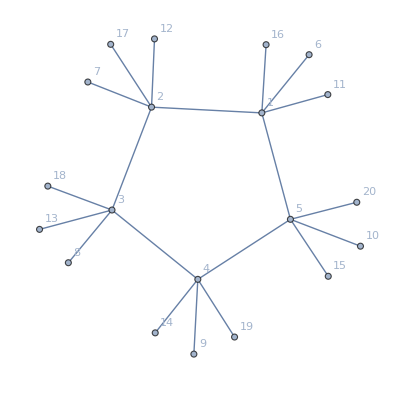

```mathematica
hairy
```

```mathematica
DistributeDefinitions[hairy]
```

{hairy}

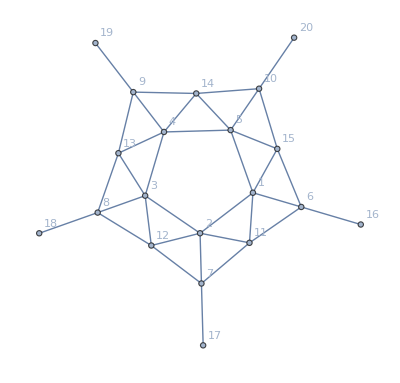

```mathematica
expMixedBisWithHair
```

```mathematica
DistributeDefinitions[expMixedBisWithHair, CountSolutions6]
```

{}

```mathematica
AbsoluteTiming[
TableForm[
ParallelTable[CountSolutions6[expMixedBisWithHair,{1<->3,1<->4},{2<->4,2<->5},{3<->5},k,{11,12,13,14,15,16,17,18,19,20}],{k,2*1024,4*1024}], TableDepth->2
]
]
```

{2241,{1,1,1,1,3,1,4,1,1,2},{4,4,12,0,0,0,0}}

{2113,{1,1,1,1,3,1,2,1,1,2},{4,4,20,0,0,0,0}}

{2177,{1,1,1,1,3,1,3,1,1,2},{8,8,16,0,0,0,0}}

{2048,{1,1,1,1,3,1,1,1,1,1},{16,16,48,0,0,0,0}}

{2242,{1,1,1,1,3,1,4,1,1,3},{8,8,32,0,0,0,0}}

{2114,{1,1,1,1,3,1,2,1,1,3},{8,8,32,0,0,0,0}}

{2178,{1,1,1,1,3,1,3,1,1,3},{16,16,32,0,0,0,0}}

{2049,{1,1,1,1,3,1,1,1,1,2},{8,8,24,0,0,0,0}}

{2243,{1,1,1,1,3,1,4,1,1,4},{4,4,20,0,0,0,0}}

{2115,{1,1,1,1,3,1,2,1,1,4},{4,4,12,0,0,0,0}}

{2179,{1,1,1,1,3,1,3,1,1,4},{8,8,16,0,0,0,0}}

{2050,{1,1,1,1,3,1,1,1,1,3},{16,16,48,0,0,0,0}}

{2244,{1,1,1,1,3,1,4,1,2,1},{4,6,20,0,0,0,0}}

{2116,{1,1,1,1,3,1,2,1,2,1},{4,6,18,0,0,0,0}}

{2180,{1,1,1,1,3,1,3,1,2,1},{8,12,18,0,0,0,0}}

{2051,{1,1,1,1,3,1,1,1,1,4},{8,8,24,0,0,0,0}}

{2245,{1,1,1,1,3,1,4,1,2,2},{2,2,6,0,0,0,0}}

{2117,{1,1,1,1,3,1,2,1,2,2},{2,2,10,0,0,0,0}}

{2052,{1,1,1,1,3,1,1,1,2,1},{8,12,28,0,0,0,0}}

{2181,{1,1,1,1,3,1,3,1,2,2},{4,4,8,0,0,0,0}}

{2246,{1,1,1,1,3,1,4,1,2,3},{4,6,20,0,0,0,0}}

{2118,{1,1,1,1,3,1,2,1,2,3},{4,6,18,0,0,0,0}}

{2053,{1,1,1,1,3,1,1,1,2,2},{4,4,12,0,0,0,0}}

{2182,{1,1,1,1,3,1,3,1,2,3},{8,12,18,0,0,0,0}}

{2247,{1,1,1,1,3,1,4,1,2,4},{2,4,14,0,0,0,0}}

{2119,{1,1,1,1,3,1,2,1,2,4},{2,4,8,0,0,0,0}}

{2054,{1,1,1,1,3,1,1,1,2,3},{8,12,28,0,0,0,0}}

{2183,{1,1,1,1,3,1,3,1,2,4},{4,8,10,0,0,0,0}}

{2248,{1,1,1,1,3,1,4,1,3,1},{8,4,26,0,0,0,0}}

{2120,{1,1,1,1,3,1,2,1,3,1},{8,4,26,0,0,0,0}}

{2055,{1,1,1,1,3,1,1,1,2,4},{4,8,16,0,0,0,0}}

{2184,{1,1,1,1,3,1,3,1,3,1},{16,8,28,0,0,0,0}}

{2249,{1,1,1,1,3,1,4,1,3,2},{4,2,10,0,0,0,0}}

{2121,{1,1,1,1,3,1,2,1,3,2},{4,2,16,0,0,0,0}}

{2056,{1,1,1,1,3,1,1,1,3,1},{16,8,40,0,0,0,0}}

{2185,{1,1,1,1,3,1,3,1,3,2},{8,4,14,0,0,0,0}}

{2250,{1,1,1,1,3,1,4,1,3,3},{8,4,26,0,0,0,0}}

{2122,{1,1,1,1,3,1,2,1,3,3},{8,4,26,0,0,0,0}}

{2057,{1,1,1,1,3,1,1,1,3,2},{8,4,20,0,0,0,0}}

{2186,{1,1,1,1,3,1,3,1,3,3},{16,8,28,0,0,0,0}}

{2251,{1,1,1,1,3,1,4,1,3,4},{4,2,16,0,0,0,0}}

{2123,{1,1,1,1,3,1,2,1,3,4},{4,2,10,0,0,0,0}}

{2058,{1,1,1,1,3,1,1,1,3,3},{16,8,40,0,0,0,0}}

{2187,{1,1,1,1,3,1,3,1,3,4},{8,4,14,0,0,0,0}}

{2252,{1,1,1,1,3,1,4,1,4,1},{4,6,18,0,0,0,0}}

{2124,{1,1,1,1,3,1,2,1,4,1},{4,6,20,0,0,0,0}}

{2059,{1,1,1,1,3,1,1,1,3,4},{8,4,20,0,0,0,0}}

{2188,{1,1,1,1,3,1,3,1,4,1},{8,12,18,0,0,0,0}}

{2253,{1,1,1,1,3,1,4,1,4,2},{2,4,8,0,0,0,0}}

{2125,{1,1,1,1,3,1,2,1,4,2},{2,4,14,0,0,0,0}}

{2060,{1,1,1,1,3,1,1,1,4,1},{8,12,28,0,0,0,0}}

{2189,{1,1,1,1,3,1,3,1,4,2},{4,8,10,0,0,0,0}}

{2254,{1,1,1,1,3,1,4,1,4,3},{4,6,18,0,0,0,0}}

{2126,{1,1,1,1,3,1,2,1,4,3},{4,6,20,0,0,0,0}}

{2061,{1,1,1,1,3,1,1,1,4,2},{4,8,16,0,0,0,0}}

{2190,{1,1,1,1,3,1,3,1,4,3},{8,12,18,0,0,0,0}}

{2255,{1,1,1,1,3,1,4,1,4,4},{2,2,10,0,0,0,0}}

{2127,{1,1,1,1,3,1,2,1,4,4},{2,2,6,0,0,0,0}}

{2062,{1,1,1,1,3,1,1,1,4,3},{8,12,28,0,0,0,0}}

{2191,{1,1,1,1,3,1,3,1,4,4},{4,4,8,0,0,0,0}}

{2256,{1,1,1,1,3,1,4,2,1,1},{6,6,22,0,0,0,0}}

{2063,{1,1,1,1,3,1,1,1,4,4},{4,4,12,0,0,0,0}}

{2128,{1,1,1,1,3,1,2,2,1,1},{6,6,20,0,0,0,0}}

{2192,{1,1,1,1,3,1,3,2,1,1},{12,12,22,0,0,0,0}}

{2257,{1,1,1,1,3,1,4,2,1,2},{4,4,6,0,0,0,0}}

{2129,{1,1,1,1,3,1,2,2,1,2},{4,4,10,0,0,0,0}}

{2064,{1,1,1,1,3,1,1,2,1,1},{12,12,32,0,0,0,0}}

{2193,{1,1,1,1,3,1,3,2,1,2},{8,8,8,0,0,0,0}}

{2258,{1,1,1,1,3,1,4,2,1,3},{6,6,22,0,0,0,0}}

{2065,{1,1,1,1,3,1,1,2,1,2},{8,8,12,0,0,0,0}}

{2130,{1,1,1,1,3,1,2,2,1,3},{6,6,20,0,0,0,0}}

{2194,{1,1,1,1,3,1,3,2,1,3},{12,12,22,0,0,0,0}}

{2259,{1,1,1,1,3,1,4,2,1,4},{2,2,16,0,0,0,0}}

{2131,{1,1,1,1,3,1,2,2,1,4},{2,2,10,0,0,0,0}}

{2066,{1,1,1,1,3,1,1,2,1,3},{12,12,32,0,0,0,0}}

{2195,{1,1,1,1,3,1,3,2,1,4},{4,4,14,0,0,0,0}}

{2260,{1,1,1,1,3,1,4,2,2,1},{3,4,13,0,0,0,0}}

{2067,{1,1,1,1,3,1,1,2,1,4},{4,4,20,0,0,0,0}}

{2132,{1,1,1,1,3,1,2,2,2,1},{3,4,11,0,0,0,0}}

{2196,{1,1,1,1,3,1,3,2,2,1},{6,8,12,0,0,0,0}}

{2261,{1,1,1,1,3,1,4,2,2,2},{2,2,3,0,0,0,0}}

{2068,{1,1,1,1,3,1,1,2,2,1},{6,8,18,0,0,0,0}}

{2133,{1,1,1,1,3,1,2,2,2,2},{2,2,5,0,0,0,0}}

{2197,{1,1,1,1,3,1,3,2,2,2},{4,4,4,0,0,0,0}}

{2262,{1,1,1,1,3,1,4,2,2,3},{3,4,13,0,0,0,0}}

{2069,{1,1,1,1,3,1,1,2,2,2},{4,4,6,0,0,0,0}}

{2134,{1,1,1,1,3,1,2,2,2,3},{3,4,11,0,0,0,0}}

{2198,{1,1,1,1,3,1,3,2,2,3},{6,8,12,0,0,0,0}}

{2263,{1,1,1,1,3,1,4,2,2,4},{1,2,10,0,0,0,0}}

{2070,{1,1,1,1,3,1,1,2,2,3},{6,8,18,0,0,0,0}}

{2135,{1,1,1,1,3,1,2,2,2,4},{1,2,6,0,0,0,0}}

{2199,{1,1,1,1,3,1,3,2,2,4},{2,4,8,0,0,0,0}}

{2264,{1,1,1,1,3,1,4,2,3,1},{6,3,19,0,0,0,0}}

{2071,{1,1,1,1,3,1,1,2,2,4},{2,4,12,0,0,0,0}}

{2136,{1,1,1,1,3,1,2,2,3,1},{6,3,17,0,0,0,0}}

{2200,{1,1,1,1,3,1,3,2,3,1},{12,6,20,0,0,0,0}}

{2265,{1,1,1,1,3,1,4,2,3,2},{4,2,5,0,0,0,0}}

{2072,{1,1,1,1,3,1,1,2,3,1},{12,6,28,0,0,0,0}}

{2137,{1,1,1,1,3,1,2,2,3,2},{4,2,8,0,0,0,0}}

{2201,{1,1,1,1,3,1,3,2,3,2},{8,4,7,0,0,0,0}}

{2266,{1,1,1,1,3,1,4,2,3,3},{6,3,19,0,0,0,0}}

{2073,{1,1,1,1,3,1,1,2,3,2},{8,4,10,0,0,0,0}}

{2138,{1,1,1,1,3,1,2,2,3,3},{6,3,17,0,0,0,0}}

{2202,{1,1,1,1,3,1,3,2,3,3},{12,6,20,0,0,0,0}}

{2267,{1,1,1,1,3,1,4,2,3,4},{2,1,14,0,0,0,0}}

{2074,{1,1,1,1,3,1,1,2,3,3},{12,6,28,0,0,0,0}}

{2139,{1,1,1,1,3,1,2,2,3,4},{2,1,9,0,0,0,0}}

{2203,{1,1,1,1,3,1,3,2,3,4},{4,2,13,0,0,0,0}}

{2268,{1,1,1,1,3,1,4,2,4,1},{3,5,12,0,0,0,0}}

{2075,{1,1,1,1,3,1,1,2,3,4},{4,2,18,0,0,0,0}}

{2140,{1,1,1,1,3,1,2,2,4,1},{3,5,12,0,0,0,0}}

{2204,{1,1,1,1,3,1,3,2,4,1},{6,10,12,0,0,0,0}}

{2269,{1,1,1,1,3,1,4,2,4,2},{2,4,4,0,0,0,0}}

{2076,{1,1,1,1,3,1,1,2,4,1},{6,10,18,0,0,0,0}}

{2141,{1,1,1,1,3,1,2,2,4,2},{2,4,7,0,0,0,0}}

{2205,{1,1,1,1,3,1,3,2,4,2},{4,8,5,0,0,0,0}}

{2270,{1,1,1,1,3,1,4,2,4,3},{3,5,12,0,0,0,0}}

{2077,{1,1,1,1,3,1,1,2,4,2},{4,8,8,0,0,0,0}}

{2142,{1,1,1,1,3,1,2,2,4,3},{3,5,12,0,0,0,0}}

{2206,{1,1,1,1,3,1,3,2,4,3},{6,10,12,0,0,0,0}}

{2271,{1,1,1,1,3,1,4,2,4,4},{1,1,8,0,0,0,0}}

{2078,{1,1,1,1,3,1,1,2,4,3},{6,10,18,0,0,0,0}}

{2143,{1,1,1,1,3,1,2,2,4,4},{1,1,5,0,0,0,0}}

{2207,{1,1,1,1,3,1,3,2,4,4},{2,2,7,0,0,0,0}}

{2272,{1,1,1,1,3,1,4,3,1,1},{4,4,22,0,0,0,0}}

{2079,{1,1,1,1,3,1,1,2,4,4},{2,2,10,0,0,0,0}}

{2144,{1,1,1,1,3,1,2,3,1,1},{4,4,22,0,0,0,0}}

{2208,{1,1,1,1,3,1,3,3,1,1},{8,8,20,0,0,0,0}}

{2273,{1,1,1,1,3,1,4,3,1,2},{2,2,8,0,0,0,0}}

{2080,{1,1,1,1,3,1,1,3,1,1},{8,8,32,0,0,0,0}}

{2145,{1,1,1,1,3,1,2,3,1,2},{2,2,14,0,0,0,0}}

{2209,{1,1,1,1,3,1,3,3,1,2},{4,4,10,0,0,0,0}}

{2274,{1,1,1,1,3,1,4,3,1,3},{4,4,22,0,0,0,0}}

{2081,{1,1,1,1,3,1,1,3,1,2},{4,4,16,0,0,0,0}}

{2146,{1,1,1,1,3,1,2,3,1,3},{4,4,22,0,0,0,0}}

{2210,{1,1,1,1,3,1,3,3,1,3},{8,8,20,0,0,0,0}}

{2275,{1,1,1,1,3,1,4,3,1,4},{2,2,14,0,0,0,0}}

{2082,{1,1,1,1,3,1,1,3,1,3},{8,8,32,0,0,0,0}}

{2147,{1,1,1,1,3,1,2,3,1,4},{2,2,8,0,0,0,0}}

{2211,{1,1,1,1,3,1,3,3,1,4},{4,4,10,0,0,0,0}}

{2276,{1,1,1,1,3,1,4,3,2,1},{2,3,15,0,0,0,0}}

{2083,{1,1,1,1,3,1,1,3,1,4},{4,4,16,0,0,0,0}}

{2148,{1,1,1,1,3,1,2,3,2,1},{2,3,13,0,0,0,0}}

{2212,{1,1,1,1,3,1,3,3,2,1},{4,6,12,0,0,0,0}}

{2277,{1,1,1,1,3,1,4,3,2,2},{1,1,4,0,0,0,0}}

{2084,{1,1,1,1,3,1,1,3,2,1},{4,6,20,0,0,0,0}}

{2149,{1,1,1,1,3,1,2,3,2,2},{1,1,7,0,0,0,0}}

{2213,{1,1,1,1,3,1,3,3,2,2},{2,2,5,0,0,0,0}}

$Aborted

```mathematica
AbsoluteTiming[
TableForm[
ParallelTable[CountSolutions6[expMixedBisWithHair,{1<->3,1<->4},{2<->4,2<->5},{3<->5},k,{11,12,13,14,15,16,17,18,19,20}],{k,5*1024,7*1024}], TableDepth->2
]
]
```

{5313,{1,1,1,2,2,1,4,1,1,2},{0,8,24,0,28,12,0}}

{5120,{1,1,1,2,2,1,1,1,1,1},{0,8,24,0,48,16,0}}

{5249,{1,1,1,2,2,1,3,1,1,2},{0,8,24,0,28,12,0}}

{5185,{1,1,1,2,2,1,2,1,1,2},{0,16,16,0,40,8,0}}

{5314,{1,1,1,2,2,1,4,1,1,3},{0,6,14,0,14,6,0}}

{5250,{1,1,1,2,2,1,3,1,1,3},{0,6,16,0,14,6,0}}

{5186,{1,1,1,2,2,1,2,1,1,3},{0,12,10,0,20,4,0}}

{5121,{1,1,1,2,2,1,1,1,1,2},{0,16,32,0,48,16,0}}

{5315,{1,1,1,2,2,1,4,1,1,4},{0,6,16,0,14,6,0}}

{5251,{1,1,1,2,2,1,3,1,1,4},{0,6,14,0,14,6,0}}

{5187,{1,1,1,2,2,1,2,1,1,4},{0,12,10,0,20,4,0}}

{5122,{1,1,1,2,2,1,1,1,1,3},{0,12,20,0,24,8,0}}

{5316,{1,1,1,2,2,1,4,1,2,1},{0,4,18,0,28,12,0}}

{5252,{1,1,1,2,2,1,3,1,2,1},{0,4,18,0,28,12,0}}

{5188,{1,1,1,2,2,1,2,1,2,1},{0,8,12,0,40,8,0}}

{5123,{1,1,1,2,2,1,1,1,1,4},{0,12,20,0,24,8,0}}

{5317,{1,1,1,2,2,1,4,1,2,2},{0,8,24,0,28,12,0}}

{5253,{1,1,1,2,2,1,3,1,2,2},{0,8,24,0,28,12,0}}

{5189,{1,1,1,2,2,1,2,1,2,2},{0,16,16,0,40,8,0}}

{5124,{1,1,1,2,2,1,1,1,2,1},{0,8,24,0,48,16,0}}

{5318,{1,1,1,2,2,1,4,1,2,3},{0,6,14,0,14,6,0}}

{5254,{1,1,1,2,2,1,3,1,2,3},{0,6,16,0,14,6,0}}

{5190,{1,1,1,2,2,1,2,1,2,3},{0,12,10,0,20,4,0}}

{5125,{1,1,1,2,2,1,1,1,2,2},{0,16,32,0,48,16,0}}

{5319,{1,1,1,2,2,1,4,1,2,4},{0,6,16,0,14,6,0}}

{5191,{1,1,1,2,2,1,2,1,2,4},{0,12,10,0,20,4,0}}

{5255,{1,1,1,2,2,1,3,1,2,4},{0,6,14,0,14,6,0}}

{5126,{1,1,1,2,2,1,1,1,2,3},{0,12,20,0,24,8,0}}

{5320,{1,1,1,2,2,1,4,1,3,1},{0,2,8,0,16,4,0}}

{5192,{1,1,1,2,2,1,2,1,3,1},{0,4,6,0,20,4,0}}

{5256,{1,1,1,2,2,1,3,1,3,1},{0,2,10,0,12,8,0}}

{5127,{1,1,1,2,2,1,1,1,2,4},{0,12,20,0,24,8,0}}

{5321,{1,1,1,2,2,1,4,1,3,2},{0,4,12,0,16,4,0}}

{5193,{1,1,1,2,2,1,2,1,3,2},{0,8,8,0,20,4,0}}

{5257,{1,1,1,2,2,1,3,1,3,2},{0,4,12,0,12,8,0}}

{5128,{1,1,1,2,2,1,1,1,3,1},{0,4,12,0,24,8,0}}

{5322,{1,1,1,2,2,1,4,1,3,3},{0,2,6,0,8,2,0}}

{5194,{1,1,1,2,2,1,2,1,3,3},{0,4,4,0,10,2,0}}

{5258,{1,1,1,2,2,1,3,1,3,3},{0,2,6,0,6,4,0}}

{5129,{1,1,1,2,2,1,1,1,3,2},{0,8,16,0,24,8,0}}

{5323,{1,1,1,2,2,1,4,1,3,4},{0,4,10,0,8,2,0}}

{5195,{1,1,1,2,2,1,2,1,3,4},{0,8,6,0,10,2,0}}

{5259,{1,1,1,2,2,1,3,1,3,4},{0,4,8,0,6,4,0}}

{5130,{1,1,1,2,2,1,1,1,3,3},{0,4,8,0,12,4,0}}

{5324,{1,1,1,2,2,1,4,1,4,1},{0,2,10,0,12,8,0}}

{5196,{1,1,1,2,2,1,2,1,4,1},{0,4,6,0,20,4,0}}

{5260,{1,1,1,2,2,1,3,1,4,1},{0,2,8,0,16,4,0}}

{5131,{1,1,1,2,2,1,1,1,3,4},{0,8,12,0,12,4,0}}

{5325,{1,1,1,2,2,1,4,1,4,2},{0,4,12,0,12,8,0}}

{5197,{1,1,1,2,2,1,2,1,4,2},{0,8,8,0,20,4,0}}

{5261,{1,1,1,2,2,1,3,1,4,2},{0,4,12,0,16,4,0}}

{5132,{1,1,1,2,2,1,1,1,4,1},{0,4,12,0,24,8,0}}

{5326,{1,1,1,2,2,1,4,1,4,3},{0,4,8,0,6,4,0}}

{5198,{1,1,1,2,2,1,2,1,4,3},{0,8,6,0,10,2,0}}

{5262,{1,1,1,2,2,1,3,1,4,3},{0,4,10,0,8,2,0}}

{5133,{1,1,1,2,2,1,1,1,4,2},{0,8,16,0,24,8,0}}

{5327,{1,1,1,2,2,1,4,1,4,4},{0,2,6,0,6,4,0}}

{5199,{1,1,1,2,2,1,2,1,4,4},{0,4,4,0,10,2,0}}

{5263,{1,1,1,2,2,1,3,1,4,4},{0,2,6,0,8,2,0}}

{5134,{1,1,1,2,2,1,1,1,4,3},{0,8,12,0,12,4,0}}

{5328,{1,1,1,2,2,1,4,2,1,1},{0,2,12,0,20,12,0}}

{5200,{1,1,1,2,2,1,2,2,1,1},{0,4,8,0,24,8,0}}

{5264,{1,1,1,2,2,1,3,2,1,1},{0,2,12,0,20,12,0}}

{5135,{1,1,1,2,2,1,1,1,4,4},{0,4,8,0,12,4,0}}

{5329,{1,1,1,2,2,1,4,2,1,2},{0,4,18,0,20,12,0}}

{5201,{1,1,1,2,2,1,2,2,1,2},{0,8,12,0,24,8,0}}

{5265,{1,1,1,2,2,1,3,2,1,2},{0,4,18,0,20,12,0}}

{5136,{1,1,1,2,2,1,1,2,1,1},{0,4,16,0,32,16,0}}

{5330,{1,1,1,2,2,1,4,2,1,3},{0,3,11,0,10,6,0}}

{5202,{1,1,1,2,2,1,2,2,1,3},{0,6,8,0,12,4,0}}

{5266,{1,1,1,2,2,1,3,2,1,3},{0,3,13,0,10,6,0}}

{5137,{1,1,1,2,2,1,1,2,1,2},{0,8,24,0,32,16,0}}

{5331,{1,1,1,2,2,1,4,2,1,4},{0,3,13,0,10,6,0}}

{5203,{1,1,1,2,2,1,2,2,1,4},{0,6,8,0,12,4,0}}

{5267,{1,1,1,2,2,1,3,2,1,4},{0,3,11,0,10,6,0}}

{5138,{1,1,1,2,2,1,1,2,1,3},{0,6,16,0,16,8,0}}

{5332,{1,1,1,2,2,1,4,2,2,1},{0,2,12,0,20,12,0}}

{5204,{1,1,1,2,2,1,2,2,2,1},{0,4,8,0,24,8,0}}

{5268,{1,1,1,2,2,1,3,2,2,1},{0,2,12,0,20,12,0}}

{5139,{1,1,1,2,2,1,1,2,1,4},{0,6,16,0,16,8,0}}

{5333,{1,1,1,2,2,1,4,2,2,2},{0,4,18,0,20,12,0}}

{5205,{1,1,1,2,2,1,2,2,2,2},{0,8,12,0,24,8,0}}

{5269,{1,1,1,2,2,1,3,2,2,2},{0,4,18,0,20,12,0}}

{5140,{1,1,1,2,2,1,1,2,2,1},{0,4,16,0,32,16,0}}

{5334,{1,1,1,2,2,1,4,2,2,3},{0,3,11,0,10,6,0}}

{5206,{1,1,1,2,2,1,2,2,2,3},{0,6,8,0,12,4,0}}

{5270,{1,1,1,2,2,1,3,2,2,3},{0,3,13,0,10,6,0}}

{5141,{1,1,1,2,2,1,1,2,2,2},{0,8,24,0,32,16,0}}

{5335,{1,1,1,2,2,1,4,2,2,4},{0,3,13,0,10,6,0}}

{5207,{1,1,1,2,2,1,2,2,2,4},{0,6,8,0,12,4,0}}

{5271,{1,1,1,2,2,1,3,2,2,4},{0,3,11,0,10,6,0}}

{5142,{1,1,1,2,2,1,1,2,2,3},{0,6,16,0,16,8,0}}

{5336,{1,1,1,2,2,1,4,2,3,1},{0,1,6,0,12,4,0}}

{5208,{1,1,1,2,2,1,2,2,3,1},{0,2,4,0,12,4,0}}

{5272,{1,1,1,2,2,1,3,2,3,1},{0,1,6,0,8,8,0}}

{5143,{1,1,1,2,2,1,1,2,2,4},{0,6,16,0,16,8,0}}

{5337,{1,1,1,2,2,1,4,2,3,2},{0,2,10,0,12,4,0}}

{5209,{1,1,1,2,2,1,2,2,3,2},{0,4,6,0,12,4,0}}

{5273,{1,1,1,2,2,1,3,2,3,2},{0,2,8,0,8,8,0}}

{5144,{1,1,1,2,2,1,1,2,3,1},{0,2,8,0,16,8,0}}

{5338,{1,1,1,2,2,1,4,2,3,3},{0,1,5,0,6,2,0}}

{5210,{1,1,1,2,2,1,2,2,3,3},{0,2,3,0,6,2,0}}

{5274,{1,1,1,2,2,1,3,2,3,3},{0,1,4,0,4,4,0}}

{5145,{1,1,1,2,2,1,1,2,3,2},{0,4,12,0,16,8,0}}

{5339,{1,1,1,2,2,1,4,2,3,4},{0,2,9,0,6,2,0}}

{5211,{1,1,1,2,2,1,2,2,3,4},{0,4,5,0,6,2,0}}

{5275,{1,1,1,2,2,1,3,2,3,4},{0,2,6,0,4,4,0}}

{5146,{1,1,1,2,2,1,1,2,3,3},{0,2,6,0,8,4,0}}

{5340,{1,1,1,2,2,1,4,2,4,1},{0,1,6,0,8,8,0}}

{5212,{1,1,1,2,2,1,2,2,4,1},{0,2,4,0,12,4,0}}

{5276,{1,1,1,2,2,1,3,2,4,1},{0,1,6,0,12,4,0}}

{5147,{1,1,1,2,2,1,1,2,3,4},{0,4,10,0,8,4,0}}

{5341,{1,1,1,2,2,1,4,2,4,2},{0,2,8,0,8,8,0}}

{5213,{1,1,1,2,2,1,2,2,4,2},{0,4,6,0,12,4,0}}

{5277,{1,1,1,2,2,1,3,2,4,2},{0,2,10,0,12,4,0}}

{5148,{1,1,1,2,2,1,1,2,4,1},{0,2,8,0,16,8,0}}

{5342,{1,1,1,2,2,1,4,2,4,3},{0,2,6,0,4,4,0}}

{5214,{1,1,1,2,2,1,2,2,4,3},{0,4,5,0,6,2,0}}

{5278,{1,1,1,2,2,1,3,2,4,3},{0,2,9,0,6,2,0}}

{5149,{1,1,1,2,2,1,1,2,4,2},{0,4,12,0,16,8,0}}

{5343,{1,1,1,2,2,1,4,2,4,4},{0,1,4,0,4,4,0}}

{5215,{1,1,1,2,2,1,2,2,4,4},{0,2,3,0,6,2,0}}

{5279,{1,1,1,2,2,1,3,2,4,4},{0,1,5,0,6,2,0}}

{5150,{1,1,1,2,2,1,1,2,4,3},{0,4,10,0,8,4,0}}

{5344,{1,1,1,2,2,1,4,3,1,1},{0,3,13,0,18,6,0}}

{5216,{1,1,1,2,2,1,2,3,1,1},{0,6,8,0,28,4,0}}

{5151,{1,1,1,2,2,1,1,2,4,4},{0,2,6,0,8,4,0}}

{5280,{1,1,1,2,2,1,3,3,1,1},{0,3,11,0,18,6,0}}

{5345,{1,1,1,2,2,1,4,3,1,2},{0,6,16,0,18,6,0}}

{5217,{1,1,1,2,2,1,2,3,1,2},{0,12,10,0,28,4,0}}

{5152,{1,1,1,2,2,1,1,3,1,1},{0,6,16,0,32,8,0}}

{5281,{1,1,1,2,2,1,3,3,1,2},{0,6,14,0,18,6,0}}

{5346,{1,1,1,2,2,1,4,3,1,3},{0,5,9,0,9,3,0}}

{5218,{1,1,1,2,2,1,2,3,1,3},{0,10,6,0,14,2,0}}

{5282,{1,1,1,2,2,1,3,3,1,3},{0,5,9,0,9,3,0}}

{5153,{1,1,1,2,2,1,1,3,1,2},{0,12,20,0,32,8,0}}

{5347,{1,1,1,2,2,1,4,3,1,4},{0,4,10,0,9,3,0}}

{5219,{1,1,1,2,2,1,2,3,1,4},{0,8,6,0,14,2,0}}

{5283,{1,1,1,2,2,1,3,3,1,4},{0,4,8,0,9,3,0}}

{5154,{1,1,1,2,2,1,1,3,1,3},{0,10,12,0,16,4,0}}

{5348,{1,1,1,2,2,1,4,3,2,1},{0,3,13,0,18,6,0}}

{5220,{1,1,1,2,2,1,2,3,2,1},{0,6,8,0,28,4,0}}

{5155,{1,1,1,2,2,1,1,3,1,4},{0,8,12,0,16,4,0}}

{5284,{1,1,1,2,2,1,3,3,2,1},{0,3,11,0,18,6,0}}

{5349,{1,1,1,2,2,1,4,3,2,2},{0,6,16,0,18,6,0}}

{5221,{1,1,1,2,2,1,2,3,2,2},{0,12,10,0,28,4,0}}

{5285,{1,1,1,2,2,1,3,3,2,2},{0,6,14,0,18,6,0}}

{5156,{1,1,1,2,2,1,1,3,2,1},{0,6,16,0,32,8,0}}

{5350,{1,1,1,2,2,1,4,3,2,3},{0,5,9,0,9,3,0}}

{5222,{1,1,1,2,2,1,2,3,2,3},{0,10,6,0,14,2,0}}

{5286,{1,1,1,2,2,1,3,3,2,3},{0,5,9,0,9,3,0}}

{5157,{1,1,1,2,2,1,1,3,2,2},{0,12,20,0,32,8,0}}

{5351,{1,1,1,2,2,1,4,3,2,4},{0,4,10,0,9,3,0}}

{5223,{1,1,1,2,2,1,2,3,2,4},{0,8,6,0,14,2,0}}

{5287,{1,1,1,2,2,1,3,3,2,4},{0,4,8,0,9,3,0}}

{5158,{1,1,1,2,2,1,1,3,2,3},{0,10,12,0,16,4,0}}

{5352,{1,1,1,2,2,1,4,3,3,1},{0,1,4,0,8,2,0}}

{5224,{1,1,1,2,2,1,2,3,3,1},{0,2,3,0,10,2,0}}

{5288,{1,1,1,2,2,1,3,3,3,1},{0,1,5,0,6,4,0}}

{5159,{1,1,1,2,2,1,1,3,2,4},{0,8,12,0,16,4,0}}

{5353,{1,1,1,2,2,1,4,3,3,2},{0,2,6,0,8,2,0}}

{5225,{1,1,1,2,2,1,2,3,3,2},{0,4,4,0,10,2,0}}

{5289,{1,1,1,2,2,1,3,3,3,2},{0,2,6,0,6,4,0}}

{5160,{1,1,1,2,2,1,1,3,3,1},{0,2,6,0,12,4,0}}

{5354,{1,1,1,2,2,1,4,3,3,3},{0,1,3,0,4,1,0}}

{5226,{1,1,1,2,2,1,2,3,3,3},{0,2,2,0,5,1,0}}

{5290,{1,1,1,2,2,1,3,3,3,3},{0,1,3,0,3,2,0}}

{5161,{1,1,1,2,2,1,1,3,3,2},{0,4,8,0,12,4,0}}

{5355,{1,1,1,2,2,1,4,3,3,4},{0,2,5,0,4,1,0}}

{5227,{1,1,1,2,2,1,2,3,3,4},{0,4,3,0,5,1,0}}

{5291,{1,1,1,2,2,1,3,3,3,4},{0,2,4,0,3,2,0}}

{5162,{1,1,1,2,2,1,1,3,3,3},{0,2,4,0,6,2,0}}

{5356,{1,1,1,2,2,1,4,3,4,1},{0,2,9,0,10,4,0}}

{5228,{1,1,1,2,2,1,2,3,4,1},{0,4,5,0,18,2,0}}

{5292,{1,1,1,2,2,1,3,3,4,1},{0,2,6,0,12,2,0}}

{5163,{1,1,1,2,2,1,1,3,3,4},{0,4,6,0,6,2,0}}

{5357,{1,1,1,2,2,1,4,3,4,2},{0,4,10,0,10,4,0}}

{5229,{1,1,1,2,2,1,2,3,4,2},{0,8,6,0,18,2,0}}

{5293,{1,1,1,2,2,1,3,3,4,2},{0,4,8,0,12,2,0}}

{5164,{1,1,1,2,2,1,1,3,4,1},{0,4,10,0,20,4,0}}

{5358,{1,1,1,2,2,1,4,3,4,3},{0,4,6,0,5,2,0}}

{5230,{1,1,1,2,2,1,2,3,4,3},{0,8,4,0,9,1,0}}

{5294,{1,1,1,2,2,1,3,3,4,3},{0,4,6,0,6,1,0}}

{5165,{1,1,1,2,2,1,1,3,4,2},{0,8,12,0,20,4,0}}

{5359,{1,1,1,2,2,1,4,3,4,4},{0,2,5,0,5,2,0}}

{5231,{1,1,1,2,2,1,2,3,4,4},{0,4,3,0,9,1,0}}

{5295,{1,1,1,2,2,1,3,3,4,4},{0,2,4,0,6,1,0}}

{5166,{1,1,1,2,2,1,1,3,4,3},{0,8,8,0,10,2,0}}

{5360,{1,1,1,2,2,1,4,4,1,1},{0,3,11,0,18,6,0}}

{5232,{1,1,1,2,2,1,2,4,1,1},{0,6,8,0,28,4,0}}

{5296,{1,1,1,2,2,1,3,4,1,1},{0,3,13,0,18,6,0}}

{5167,{1,1,1,2,2,1,1,3,4,4},{0,4,6,0,10,2,0}}

{5361,{1,1,1,2,2,1,4,4,1,2},{0,6,14,0,18,6,0}}

{5233,{1,1,1,2,2,1,2,4,1,2},{0,12,10,0,28,4,0}}

{5297,{1,1,1,2,2,1,3,4,1,2},{0,6,16,0,18,6,0}}

{5168,{1,1,1,2,2,1,1,4,1,1},{0,6,16,0,32,8,0}}

{5362,{1,1,1,2,2,1,4,4,1,3},{0,4,8,0,9,3,0}}

{5234,{1,1,1,2,2,1,2,4,1,3},{0,8,6,0,14,2,0}}

{5298,{1,1,1,2,2,1,3,4,1,3},{0,4,10,0,9,3,0}}

{5169,{1,1,1,2,2,1,1,4,1,2},{0,12,20,0,32,8,0}}

{5363,{1,1,1,2,2,1,4,4,1,4},{0,5,9,0,9,3,0}}

{5235,{1,1,1,2,2,1,2,4,1,4},{0,10,6,0,14,2,0}}

{5299,{1,1,1,2,2,1,3,4,1,4},{0,5,9,0,9,3,0}}

{5170,{1,1,1,2,2,1,1,4,1,3},{0,8,12,0,16,4,0}}

{5364,{1,1,1,2,2,1,4,4,2,1},{0,3,11,0,18,6,0}}

{5236,{1,1,1,2,2,1,2,4,2,1},{0,6,8,0,28,4,0}}

{5300,{1,1,1,2,2,1,3,4,2,1},{0,3,13,0,18,6,0}}

{5171,{1,1,1,2,2,1,1,4,1,4},{0,10,12,0,16,4,0}}

{5365,{1,1,1,2,2,1,4,4,2,2},{0,6,14,0,18,6,0}}

{5237,{1,1,1,2,2,1,2,4,2,2},{0,12,10,0,28,4,0}}

{5172,{1,1,1,2,2,1,1,4,2,1},{0,6,16,0,32,8,0}}

{5301,{1,1,1,2,2,1,3,4,2,2},{0,6,16,0,18,6,0}}

{5366,{1,1,1,2,2,1,4,4,2,3},{0,4,8,0,9,3,0}}

{5238,{1,1,1,2,2,1,2,4,2,3},{0,8,6,0,14,2,0}}

{5302,{1,1,1,2,2,1,3,4,2,3},{0,4,10,0,9,3,0}}

{5173,{1,1,1,2,2,1,1,4,2,2},{0,12,20,0,32,8,0}}

{5367,{1,1,1,2,2,1,4,4,2,4},{0,5,9,0,9,3,0}}

{5239,{1,1,1,2,2,1,2,4,2,4},{0,10,6,0,14,2,0}}

{5303,{1,1,1,2,2,1,3,4,2,4},{0,5,9,0,9,3,0}}

{5174,{1,1,1,2,2,1,1,4,2,3},{0,8,12,0,16,4,0}}

{5368,{1,1,1,2,2,1,4,4,3,1},{0,2,6,0,12,2,0}}

{5240,{1,1,1,2,2,1,2,4,3,1},{0,4,5,0,18,2,0}}

{5304,{1,1,1,2,2,1,3,4,3,1},{0,2,9,0,10,4,0}}

{5175,{1,1,1,2,2,1,1,4,2,4},{0,10,12,0,16,4,0}}

{5369,{1,1,1,2,2,1,4,4,3,2},{0,4,8,0,12,2,0}}

{5241,{1,1,1,2,2,1,2,4,3,2},{0,8,6,0,18,2,0}}

{5305,{1,1,1,2,2,1,3,4,3,2},{0,4,10,0,10,4,0}}

{5176,{1,1,1,2,2,1,1,4,3,1},{0,4,10,0,20,4,0}}

{5370,{1,1,1,2,2,1,4,4,3,3},{0,2,4,0,6,1,0}}

{5242,{1,1,1,2,2,1,2,4,3,3},{0,4,3,0,9,1,0}}

{5306,{1,1,1,2,2,1,3,4,3,3},{0,2,5,0,5,2,0}}

{5177,{1,1,1,2,2,1,1,4,3,2},{0,8,12,0,20,4,0}}

{5371,{1,1,1,2,2,1,4,4,3,4},{0,4,6,0,6,1,0}}

{5243,{1,1,1,2,2,1,2,4,3,4},{0,8,4,0,9,1,0}}

{5307,{1,1,1,2,2,1,3,4,3,4},{0,4,6,0,5,2,0}}

{5178,{1,1,1,2,2,1,1,4,3,3},{0,4,6,0,10,2,0}}

{5372,{1,1,1,2,2,1,4,4,4,1},{0,1,5,0,6,4,0}}

{5244,{1,1,1,2,2,1,2,4,4,1},{0,2,3,0,10,2,0}}

{5308,{1,1,1,2,2,1,3,4,4,1},{0,1,4,0,8,2,0}}

{5179,{1,1,1,2,2,1,1,4,3,4},{0,8,8,0,10,2,0}}

{5373,{1,1,1,2,2,1,4,4,4,2},{0,2,6,0,6,4,0}}

{5245,{1,1,1,2,2,1,2,4,4,2},{0,4,4,0,10,2,0}}

{5309,{1,1,1,2,2,1,3,4,4,2},{0,2,6,0,8,2,0}}

{5180,{1,1,1,2,2,1,1,4,4,1},{0,2,6,0,12,4,0}}

{5374,{1,1,1,2,2,1,4,4,4,3},{0,2,4,0,3,2,0}}

{5246,{1,1,1,2,2,1,2,4,4,3},{0,4,3,0,5,1,0}}

{5310,{1,1,1,2,2,1,3,4,4,3},{0,2,5,0,4,1,0}}

{5181,{1,1,1,2,2,1,1,4,4,2},{0,4,8,0,12,4,0}}

{5375,{1,1,1,2,2,1,4,4,4,4},{0,1,3,0,3,2,0}}

{5247,{1,1,1,2,2,1,2,4,4,4},{0,2,2,0,5,1,0}}

{5311,{1,1,1,2,2,1,3,4,4,4},{0,1,3,0,4,1,0}}

{5182,{1,1,1,2,2,1,1,4,4,3},{0,4,6,0,6,2,0}}

{5376,{1,1,1,2,2,2,1,1,1,1},{0,8,24,0,48,16,0}}

{5248,{1,1,1,2,2,1,3,1,1,1},{0,4,18,0,28,12,0}}

{5183,{1,1,1,2,2,1,1,4,4,4},{0,2,4,0,6,2,0}}

{5312,{1,1,1,2,2,1,4,1,1,1},{0,4,18,0,28,12,0}}

{5377,{1,1,1,2,2,2,1,1,1,2},{0,16,32,0,48,16,0}}

{5441,{1,1,1,2,2,2,2,1,1,2},{0,16,16,0,40,8,0}}

{5184,{1,1,1,2,2,1,2,1,1,1},{0,8,12,0,40,8,0}}

{5505,{1,1,1,2,2,2,3,1,1,2},{0,8,24,0,28,12,0}}

{5378,{1,1,1,2,2,2,1,1,1,3},{0,12,20,0,24,8,0}}

{5442,{1,1,1,2,2,2,2,1,1,3},{0,12,10,0,20,4,0}}

{5569,{1,1,1,2,2,2,4,1,1,2},{0,8,24,0,28,12,0}}

{5506,{1,1,1,2,2,2,3,1,1,3},{0,6,16,0,14,6,0}}

{5379,{1,1,1,2,2,2,1,1,1,4},{0,12,20,0,24,8,0}}

{5443,{1,1,1,2,2,2,2,1,1,4},{0,12,10,0,20,4,0}}

{5570,{1,1,1,2,2,2,4,1,1,3},{0,6,14,0,14,6,0}}

{5507,{1,1,1,2,2,2,3,1,1,4},{0,6,14,0,14,6,0}}

{5380,{1,1,1,2,2,2,1,1,2,1},{0,8,24,0,48,16,0}}

{5444,{1,1,1,2,2,2,2,1,2,1},{0,8,12,0,40,8,0}}

{5571,{1,1,1,2,2,2,4,1,1,4},{0,6,16,0,14,6,0}}

{5508,{1,1,1,2,2,2,3,1,2,1},{0,4,18,0,28,12,0}}

{5381,{1,1,1,2,2,2,1,1,2,2},{0,16,32,0,48,16,0}}

{5445,{1,1,1,2,2,2,2,1,2,2},{0,16,16,0,40,8,0}}

{5572,{1,1,1,2,2,2,4,1,2,1},{0,4,18,0,28,12,0}}

{5509,{1,1,1,2,2,2,3,1,2,2},{0,8,24,0,28,12,0}}

{5382,{1,1,1,2,2,2,1,1,2,3},{0,12,20,0,24,8,0}}

{5446,{1,1,1,2,2,2,2,1,2,3},{0,12,10,0,20,4,0}}

{5573,{1,1,1,2,2,2,4,1,2,2},{0,8,24,0,28,12,0}}

{5510,{1,1,1,2,2,2,3,1,2,3},{0,6,16,0,14,6,0}}

{5383,{1,1,1,2,2,2,1,1,2,4},{0,12,20,0,24,8,0}}

{5447,{1,1,1,2,2,2,2,1,2,4},{0,12,10,0,20,4,0}}

{5574,{1,1,1,2,2,2,4,1,2,3},{0,6,14,0,14,6,0}}

{5511,{1,1,1,2,2,2,3,1,2,4},{0,6,14,0,14,6,0}}

{5384,{1,1,1,2,2,2,1,1,3,1},{0,4,12,0,24,8,0}}

{5448,{1,1,1,2,2,2,2,1,3,1},{0,4,6,0,20,4,0}}

{5575,{1,1,1,2,2,2,4,1,2,4},{0,6,16,0,14,6,0}}

{5512,{1,1,1,2,2,2,3,1,3,1},{0,2,10,0,12,8,0}}

{5385,{1,1,1,2,2,2,1,1,3,2},{0,8,16,0,24,8,0}}

{5449,{1,1,1,2,2,2,2,1,3,2},{0,8,8,0,20,4,0}}

{5576,{1,1,1,2,2,2,4,1,3,1},{0,2,8,0,16,4,0}}

{5513,{1,1,1,2,2,2,3,1,3,2},{0,4,12,0,12,8,0}}

{5386,{1,1,1,2,2,2,1,1,3,3},{0,4,8,0,12,4,0}}

{5450,{1,1,1,2,2,2,2,1,3,3},{0,4,4,0,10,2,0}}

{5577,{1,1,1,2,2,2,4,1,3,2},{0,4,12,0,16,4,0}}

{5514,{1,1,1,2,2,2,3,1,3,3},{0,2,6,0,6,4,0}}

{5387,{1,1,1,2,2,2,1,1,3,4},{0,8,12,0,12,4,0}}

{5451,{1,1,1,2,2,2,2,1,3,4},{0,8,6,0,10,2,0}}

{5578,{1,1,1,2,2,2,4,1,3,3},{0,2,6,0,8,2,0}}

{5515,{1,1,1,2,2,2,3,1,3,4},{0,4,8,0,6,4,0}}

{5388,{1,1,1,2,2,2,1,1,4,1},{0,4,12,0,24,8,0}}

{5452,{1,1,1,2,2,2,2,1,4,1},{0,4,6,0,20,4,0}}

{5579,{1,1,1,2,2,2,4,1,3,4},{0,4,10,0,8,2,0}}

{5516,{1,1,1,2,2,2,3,1,4,1},{0,2,8,0,16,4,0}}

{5389,{1,1,1,2,2,2,1,1,4,2},{0,8,16,0,24,8,0}}

{5453,{1,1,1,2,2,2,2,1,4,2},{0,8,8,0,20,4,0}}

{5580,{1,1,1,2,2,2,4,1,4,1},{0,2,10,0,12,8,0}}

{5517,{1,1,1,2,2,2,3,1,4,2},{0,4,12,0,16,4,0}}

{5390,{1,1,1,2,2,2,1,1,4,3},{0,8,12,0,12,4,0}}

{5454,{1,1,1,2,2,2,2,1,4,3},{0,8,6,0,10,2,0}}

{5581,{1,1,1,2,2,2,4,1,4,2},{0,4,12,0,12,8,0}}

{5518,{1,1,1,2,2,2,3,1,4,3},{0,4,10,0,8,2,0}}

{5391,{1,1,1,2,2,2,1,1,4,4},{0,4,8,0,12,4,0}}

{5455,{1,1,1,2,2,2,2,1,4,4},{0,4,4,0,10,2,0}}

{5582,{1,1,1,2,2,2,4,1,4,3},{0,4,8,0,6,4,0}}

{5519,{1,1,1,2,2,2,3,1,4,4},{0,2,6,0,8,2,0}}

{5392,{1,1,1,2,2,2,1,2,1,1},{0,4,16,0,32,16,0}}

{5456,{1,1,1,2,2,2,2,2,1,1},{0,4,8,0,24,8,0}}

{5583,{1,1,1,2,2,2,4,1,4,4},{0,2,6,0,6,4,0}}

{5520,{1,1,1,2,2,2,3,2,1,1},{0,2,12,0,20,12,0}}

{5393,{1,1,1,2,2,2,1,2,1,2},{0,8,24,0,32,16,0}}

{5457,{1,1,1,2,2,2,2,2,1,2},{0,8,12,0,24,8,0}}

{5584,{1,1,1,2,2,2,4,2,1,1},{0,2,12,0,20,12,0}}

{5521,{1,1,1,2,2,2,3,2,1,2},{0,4,18,0,20,12,0}}

{5394,{1,1,1,2,2,2,1,2,1,3},{0,6,16,0,16,8,0}}

{5458,{1,1,1,2,2,2,2,2,1,3},{0,6,8,0,12,4,0}}

{5585,{1,1,1,2,2,2,4,2,1,2},{0,4,18,0,20,12,0}}

{5522,{1,1,1,2,2,2,3,2,1,3},{0,3,13,0,10,6,0}}

{5395,{1,1,1,2,2,2,1,2,1,4},{0,6,16,0,16,8,0}}

{5459,{1,1,1,2,2,2,2,2,1,4},{0,6,8,0,12,4,0}}

{5586,{1,1,1,2,2,2,4,2,1,3},{0,3,11,0,10,6,0}}

{5523,{1,1,1,2,2,2,3,2,1,4},{0,3,11,0,10,6,0}}

{5396,{1,1,1,2,2,2,1,2,2,1},{0,4,16,0,32,16,0}}

{5460,{1,1,1,2,2,2,2,2,2,1},{0,4,8,0,24,8,0}}

{5587,{1,1,1,2,2,2,4,2,1,4},{0,3,13,0,10,6,0}}

{5524,{1,1,1,2,2,2,3,2,2,1},{0,2,12,0,20,12,0}}

{5397,{1,1,1,2,2,2,1,2,2,2},{0,8,24,0,32,16,0}}

{5461,{1,1,1,2,2,2,2,2,2,2},{0,8,12,0,24,8,0}}

{5588,{1,1,1,2,2,2,4,2,2,1},{0,2,12,0,20,12,0}}

{5525,{1,1,1,2,2,2,3,2,2,2},{0,4,18,0,20,12,0}}

{5398,{1,1,1,2,2,2,1,2,2,3},{0,6,16,0,16,8,0}}

{5462,{1,1,1,2,2,2,2,2,2,3},{0,6,8,0,12,4,0}}

{5589,{1,1,1,2,2,2,4,2,2,2},{0,4,18,0,20,12,0}}

{5526,{1,1,1,2,2,2,3,2,2,3},{0,3,13,0,10,6,0}}

{5399,{1,1,1,2,2,2,1,2,2,4},{0,6,16,0,16,8,0}}

{5463,{1,1,1,2,2,2,2,2,2,4},{0,6,8,0,12,4,0}}

{5590,{1,1,1,2,2,2,4,2,2,3},{0,3,11,0,10,6,0}}

{5527,{1,1,1,2,2,2,3,2,2,4},{0,3,11,0,10,6,0}}

{5400,{1,1,1,2,2,2,1,2,3,1},{0,2,8,0,16,8,0}}

{5464,{1,1,1,2,2,2,2,2,3,1},{0,2,4,0,12,4,0}}

{5591,{1,1,1,2,2,2,4,2,2,4},{0,3,13,0,10,6,0}}

{5528,{1,1,1,2,2,2,3,2,3,1},{0,1,6,0,8,8,0}}

{5401,{1,1,1,2,2,2,1,2,3,2},{0,4,12,0,16,8,0}}

{5465,{1,1,1,2,2,2,2,2,3,2},{0,4,6,0,12,4,0}}

{5592,{1,1,1,2,2,2,4,2,3,1},{0,1,6,0,12,4,0}}

{5529,{1,1,1,2,2,2,3,2,3,2},{0,2,8,0,8,8,0}}

{5402,{1,1,1,2,2,2,1,2,3,3},{0,2,6,0,8,4,0}}

{5466,{1,1,1,2,2,2,2,2,3,3},{0,2,3,0,6,2,0}}

{5593,{1,1,1,2,2,2,4,2,3,2},{0,2,10,0,12,4,0}}

{5530,{1,1,1,2,2,2,3,2,3,3},{0,1,4,0,4,4,0}}

{5403,{1,1,1,2,2,2,1,2,3,4},{0,4,10,0,8,4,0}}

{5467,{1,1,1,2,2,2,2,2,3,4},{0,4,5,0,6,2,0}}

{5594,{1,1,1,2,2,2,4,2,3,3},{0,1,5,0,6,2,0}}

{5531,{1,1,1,2,2,2,3,2,3,4},{0,2,6,0,4,4,0}}

{5404,{1,1,1,2,2,2,1,2,4,1},{0,2,8,0,16,8,0}}

{5468,{1,1,1,2,2,2,2,2,4,1},{0,2,4,0,12,4,0}}

{5595,{1,1,1,2,2,2,4,2,3,4},{0,2,9,0,6,2,0}}

{5532,{1,1,1,2,2,2,3,2,4,1},{0,1,6,0,12,4,0}}

{5405,{1,1,1,2,2,2,1,2,4,2},{0,4,12,0,16,8,0}}

{5469,{1,1,1,2,2,2,2,2,4,2},{0,4,6,0,12,4,0}}

{5596,{1,1,1,2,2,2,4,2,4,1},{0,1,6,0,8,8,0}}

{5533,{1,1,1,2,2,2,3,2,4,2},{0,2,10,0,12,4,0}}

{5406,{1,1,1,2,2,2,1,2,4,3},{0,4,10,0,8,4,0}}

{5470,{1,1,1,2,2,2,2,2,4,3},{0,4,5,0,6,2,0}}

{5597,{1,1,1,2,2,2,4,2,4,2},{0,2,8,0,8,8,0}}

{5534,{1,1,1,2,2,2,3,2,4,3},{0,2,9,0,6,2,0}}

{5407,{1,1,1,2,2,2,1,2,4,4},{0,2,6,0,8,4,0}}

{5471,{1,1,1,2,2,2,2,2,4,4},{0,2,3,0,6,2,0}}

{5598,{1,1,1,2,2,2,4,2,4,3},{0,2,6,0,4,4,0}}

{5535,{1,1,1,2,2,2,3,2,4,4},{0,1,5,0,6,2,0}}

{5599,{1,1,1,2,2,2,4,2,4,4},{0,1,4,0,4,4,0}}

{5408,{1,1,1,2,2,2,1,3,1,1},{0,6,16,0,32,8,0}}

{5472,{1,1,1,2,2,2,2,3,1,1},{0,6,8,0,28,4,0}}

{5536,{1,1,1,2,2,2,3,3,1,1},{0,3,11,0,18,6,0}}

{5600,{1,1,1,2,2,2,4,3,1,1},{0,3,13,0,18,6,0}}

{5409,{1,1,1,2,2,2,1,3,1,2},{0,12,20,0,32,8,0}}

{5473,{1,1,1,2,2,2,2,3,1,2},{0,12,10,0,28,4,0}}

{5537,{1,1,1,2,2,2,3,3,1,2},{0,6,14,0,18,6,0}}

{5601,{1,1,1,2,2,2,4,3,1,2},{0,6,16,0,18,6,0}}

{5410,{1,1,1,2,2,2,1,3,1,3},{0,10,12,0,16,4,0}}

{5474,{1,1,1,2,2,2,2,3,1,3},{0,10,6,0,14,2,0}}

{5538,{1,1,1,2,2,2,3,3,1,3},{0,5,9,0,9,3,0}}

{5602,{1,1,1,2,2,2,4,3,1,3},{0,5,9,0,9,3,0}}

{5411,{1,1,1,2,2,2,1,3,1,4},{0,8,12,0,16,4,0}}

{5475,{1,1,1,2,2,2,2,3,1,4},{0,8,6,0,14,2,0}}

{5539,{1,1,1,2,2,2,3,3,1,4},{0,4,8,0,9,3,0}}

{5603,{1,1,1,2,2,2,4,3,1,4},{0,4,10,0,9,3,0}}

{5476,{1,1,1,2,2,2,2,3,2,1},{0,6,8,0,28,4,0}}

{5412,{1,1,1,2,2,2,1,3,2,1},{0,6,16,0,32,8,0}}

{5540,{1,1,1,2,2,2,3,3,2,1},{0,3,11,0,18,6,0}}

{5604,{1,1,1,2,2,2,4,3,2,1},{0,3,13,0,18,6,0}}

{5477,{1,1,1,2,2,2,2,3,2,2},{0,12,10,0,28,4,0}}

{5413,{1,1,1,2,2,2,1,3,2,2},{0,12,20,0,32,8,0}}

{5541,{1,1,1,2,2,2,3,3,2,2},{0,6,14,0,18,6,0}}

{5605,{1,1,1,2,2,2,4,3,2,2},{0,6,16,0,18,6,0}}

{5478,{1,1,1,2,2,2,2,3,2,3},{0,10,6,0,14,2,0}}

{5414,{1,1,1,2,2,2,1,3,2,3},{0,10,12,0,16,4,0}}

{5542,{1,1,1,2,2,2,3,3,2,3},{0,5,9,0,9,3,0}}

{5606,{1,1,1,2,2,2,4,3,2,3},{0,5,9,0,9,3,0}}

{5479,{1,1,1,2,2,2,2,3,2,4},{0,8,6,0,14,2,0}}

{5415,{1,1,1,2,2,2,1,3,2,4},{0,8,12,0,16,4,0}}

{5543,{1,1,1,2,2,2,3,3,2,4},{0,4,8,0,9,3,0}}

{5607,{1,1,1,2,2,2,4,3,2,4},{0,4,10,0,9,3,0}}

{5480,{1,1,1,2,2,2,2,3,3,1},{0,2,3,0,10,2,0}}

{5416,{1,1,1,2,2,2,1,3,3,1},{0,2,6,0,12,4,0}}

{5544,{1,1,1,2,2,2,3,3,3,1},{0,1,5,0,6,4,0}}

{5608,{1,1,1,2,2,2,4,3,3,1},{0,1,4,0,8,2,0}}

{5481,{1,1,1,2,2,2,2,3,3,2},{0,4,4,0,10,2,0}}

{5417,{1,1,1,2,2,2,1,3,3,2},{0,4,8,0,12,4,0}}

{5545,{1,1,1,2,2,2,3,3,3,2},{0,2,6,0,6,4,0}}

{5609,{1,1,1,2,2,2,4,3,3,2},{0,2,6,0,8,2,0}}

{5482,{1,1,1,2,2,2,2,3,3,3},{0,2,2,0,5,1,0}}

{5418,{1,1,1,2,2,2,1,3,3,3},{0,2,4,0,6,2,0}}

{5546,{1,1,1,2,2,2,3,3,3,3},{0,1,3,0,3,2,0}}

{5610,{1,1,1,2,2,2,4,3,3,3},{0,1,3,0,4,1,0}}

{5483,{1,1,1,2,2,2,2,3,3,4},{0,4,3,0,5,1,0}}

{5419,{1,1,1,2,2,2,1,3,3,4},{0,4,6,0,6,2,0}}

{5547,{1,1,1,2,2,2,3,3,3,4},{0,2,4,0,3,2,0}}

{5611,{1,1,1,2,2,2,4,3,3,4},{0,2,5,0,4,1,0}}

{5484,{1,1,1,2,2,2,2,3,4,1},{0,4,5,0,18,2,0}}

{5420,{1,1,1,2,2,2,1,3,4,1},{0,4,10,0,20,4,0}}

{5548,{1,1,1,2,2,2,3,3,4,1},{0,2,6,0,12,2,0}}

{5612,{1,1,1,2,2,2,4,3,4,1},{0,2,9,0,10,4,0}}

{5485,{1,1,1,2,2,2,2,3,4,2},{0,8,6,0,18,2,0}}

{5421,{1,1,1,2,2,2,1,3,4,2},{0,8,12,0,20,4,0}}

{5549,{1,1,1,2,2,2,3,3,4,2},{0,4,8,0,12,2,0}}

{5613,{1,1,1,2,2,2,4,3,4,2},{0,4,10,0,10,4,0}}

{5486,{1,1,1,2,2,2,2,3,4,3},{0,8,4,0,9,1,0}}

{5422,{1,1,1,2,2,2,1,3,4,3},{0,8,8,0,10,2,0}}

{5550,{1,1,1,2,2,2,3,3,4,3},{0,4,6,0,6,1,0}}

{5614,{1,1,1,2,2,2,4,3,4,3},{0,4,6,0,5,2,0}}

{5487,{1,1,1,2,2,2,2,3,4,4},{0,4,3,0,9,1,0}}

{5423,{1,1,1,2,2,2,1,3,4,4},{0,4,6,0,10,2,0}}

{5551,{1,1,1,2,2,2,3,3,4,4},{0,2,4,0,6,1,0}}

{5615,{1,1,1,2,2,2,4,3,4,4},{0,2,5,0,5,2,0}}

{5488,{1,1,1,2,2,2,2,4,1,1},{0,6,8,0,28,4,0}}

{5424,{1,1,1,2,2,2,1,4,1,1},{0,6,16,0,32,8,0}}

{5552,{1,1,1,2,2,2,3,4,1,1},{0,3,13,0,18,6,0}}

{5616,{1,1,1,2,2,2,4,4,1,1},{0,3,11,0,18,6,0}}

{5489,{1,1,1,2,2,2,2,4,1,2},{0,12,10,0,28,4,0}}

{5425,{1,1,1,2,2,2,1,4,1,2},{0,12,20,0,32,8,0}}

{5553,{1,1,1,2,2,2,3,4,1,2},{0,6,16,0,18,6,0}}

{5617,{1,1,1,2,2,2,4,4,1,2},{0,6,14,0,18,6,0}}

{5490,{1,1,1,2,2,2,2,4,1,3},{0,8,6,0,14,2,0}}

{5426,{1,1,1,2,2,2,1,4,1,3},{0,8,12,0,16,4,0}}

{5554,{1,1,1,2,2,2,3,4,1,3},{0,4,10,0,9,3,0}}

{5618,{1,1,1,2,2,2,4,4,1,3},{0,4,8,0,9,3,0}}

{5491,{1,1,1,2,2,2,2,4,1,4},{0,10,6,0,14,2,0}}

{5427,{1,1,1,2,2,2,1,4,1,4},{0,10,12,0,16,4,0}}

{5555,{1,1,1,2,2,2,3,4,1,4},{0,5,9,0,9,3,0}}

{5619,{1,1,1,2,2,2,4,4,1,4},{0,5,9,0,9,3,0}}

{5492,{1,1,1,2,2,2,2,4,2,1},{0,6,8,0,28,4,0}}

{5428,{1,1,1,2,2,2,1,4,2,1},{0,6,16,0,32,8,0}}

{5556,{1,1,1,2,2,2,3,4,2,1},{0,3,13,0,18,6,0}}

{5620,{1,1,1,2,2,2,4,4,2,1},{0,3,11,0,18,6,0}}

{5493,{1,1,1,2,2,2,2,4,2,2},{0,12,10,0,28,4,0}}

{5429,{1,1,1,2,2,2,1,4,2,2},{0,12,20,0,32,8,0}}

{5557,{1,1,1,2,2,2,3,4,2,2},{0,6,16,0,18,6,0}}

{5621,{1,1,1,2,2,2,4,4,2,2},{0,6,14,0,18,6,0}}

{5494,{1,1,1,2,2,2,2,4,2,3},{0,8,6,0,14,2,0}}

{5430,{1,1,1,2,2,2,1,4,2,3},{0,8,12,0,16,4,0}}

{5558,{1,1,1,2,2,2,3,4,2,3},{0,4,10,0,9,3,0}}

{5622,{1,1,1,2,2,2,4,4,2,3},{0,4,8,0,9,3,0}}

{5495,{1,1,1,2,2,2,2,4,2,4},{0,10,6,0,14,2,0}}

{5431,{1,1,1,2,2,2,1,4,2,4},{0,10,12,0,16,4,0}}

{5559,{1,1,1,2,2,2,3,4,2,4},{0,5,9,0,9,3,0}}

{5623,{1,1,1,2,2,2,4,4,2,4},{0,5,9,0,9,3,0}}

{5496,{1,1,1,2,2,2,2,4,3,1},{0,4,5,0,18,2,0}}

{5432,{1,1,1,2,2,2,1,4,3,1},{0,4,10,0,20,4,0}}

{5560,{1,1,1,2,2,2,3,4,3,1},{0,2,9,0,10,4,0}}

{5624,{1,1,1,2,2,2,4,4,3,1},{0,2,6,0,12,2,0}}

{5497,{1,1,1,2,2,2,2,4,3,2},{0,8,6,0,18,2,0}}

{5433,{1,1,1,2,2,2,1,4,3,2},{0,8,12,0,20,4,0}}

{5561,{1,1,1,2,2,2,3,4,3,2},{0,4,10,0,10,4,0}}

{5625,{1,1,1,2,2,2,4,4,3,2},{0,4,8,0,12,2,0}}

{5498,{1,1,1,2,2,2,2,4,3,3},{0,4,3,0,9,1,0}}

{5434,{1,1,1,2,2,2,1,4,3,3},{0,4,6,0,10,2,0}}

{5562,{1,1,1,2,2,2,3,4,3,3},{0,2,5,0,5,2,0}}

{5626,{1,1,1,2,2,2,4,4,3,3},{0,2,4,0,6,1,0}}

{5499,{1,1,1,2,2,2,2,4,3,4},{0,8,4,0,9,1,0}}

{5435,{1,1,1,2,2,2,1,4,3,4},{0,8,8,0,10,2,0}}

{5563,{1,1,1,2,2,2,3,4,3,4},{0,4,6,0,5,2,0}}

{5627,{1,1,1,2,2,2,4,4,3,4},{0,4,6,0,6,1,0}}

{5500,{1,1,1,2,2,2,2,4,4,1},{0,2,3,0,10,2,0}}

{5436,{1,1,1,2,2,2,1,4,4,1},{0,2,6,0,12,4,0}}

{5564,{1,1,1,2,2,2,3,4,4,1},{0,1,4,0,8,2,0}}

{5628,{1,1,1,2,2,2,4,4,4,1},{0,1,5,0,6,4,0}}

{5501,{1,1,1,2,2,2,2,4,4,2},{0,4,4,0,10,2,0}}

{5437,{1,1,1,2,2,2,1,4,4,2},{0,4,8,0,12,4,0}}

{5565,{1,1,1,2,2,2,3,4,4,2},{0,2,6,0,8,2,0}}

{5629,{1,1,1,2,2,2,4,4,4,2},{0,2,6,0,6,4,0}}

{5502,{1,1,1,2,2,2,2,4,4,3},{0,4,3,0,5,1,0}}

{5438,{1,1,1,2,2,2,1,4,4,3},{0,4,6,0,6,2,0}}

{5566,{1,1,1,2,2,2,3,4,4,3},{0,2,5,0,4,1,0}}

{5630,{1,1,1,2,2,2,4,4,4,3},{0,2,4,0,3,2,0}}

{5503,{1,1,1,2,2,2,2,4,4,4},{0,2,2,0,5,1,0}}

{5439,{1,1,1,2,2,2,1,4,4,4},{0,2,4,0,6,2,0}}

{5567,{1,1,1,2,2,2,3,4,4,4},{0,1,3,0,4,1,0}}

{5631,{1,1,1,2,2,2,4,4,4,4},{0,1,3,0,3,2,0}}

{5504,{1,1,1,2,2,2,3,1,1,1},{0,4,18,0,28,12,0}}

{5440,{1,1,1,2,2,2,2,1,1,1},{0,8,12,0,40,8,0}}

{5568,{1,1,1,2,2,2,4,1,1,1},{0,4,18,0,28,12,0}}

{5632,{1,1,1,2,2,3,1,1,1,1},{0,4,12,0,24,8,0}}

{5633,{1,1,1,2,2,3,1,1,1,2},{0,8,16,0,24,8,0}}

{5697,{1,1,1,2,2,3,2,1,1,2},{0,8,8,0,20,4,0}}

{5761,{1,1,1,2,2,3,3,1,1,2},{0,4,8,0,12,4,0}}

{5825,{1,1,1,2,2,3,4,1,1,2},{0,4,16,0,16,8,0}}

{5634,{1,1,1,2,2,3,1,1,1,3},{0,4,8,0,12,4,0}}

{5698,{1,1,1,2,2,3,2,1,1,3},{0,4,4,0,10,2,0}}

{5762,{1,1,1,2,2,3,3,1,1,3},{0,2,4,0,6,2,0}}

{5826,{1,1,1,2,2,3,4,1,1,3},{0,2,8,0,8,4,0}}

{5635,{1,1,1,2,2,3,1,1,1,4},{0,8,12,0,12,4,0}}

{5699,{1,1,1,2,2,3,2,1,1,4},{0,8,6,0,10,2,0}}

{5763,{1,1,1,2,2,3,3,1,1,4},{0,4,6,0,6,2,0}}

{5827,{1,1,1,2,2,3,4,1,1,4},{0,4,12,0,8,4,0}}

{5636,{1,1,1,2,2,3,1,1,2,1},{0,4,12,0,24,8,0}}

{5700,{1,1,1,2,2,3,2,1,2,1},{0,4,6,0,20,4,0}}

{5764,{1,1,1,2,2,3,3,1,2,1},{0,2,6,0,12,4,0}}

{5828,{1,1,1,2,2,3,4,1,2,1},{0,2,12,0,16,8,0}}

{5637,{1,1,1,2,2,3,1,1,2,2},{0,8,16,0,24,8,0}}

{5701,{1,1,1,2,2,3,2,1,2,2},{0,8,8,0,20,4,0}}

{5765,{1,1,1,2,2,3,3,1,2,2},{0,4,8,0,12,4,0}}

{5829,{1,1,1,2,2,3,4,1,2,2},{0,4,16,0,16,8,0}}

{5638,{1,1,1,2,2,3,1,1,2,3},{0,4,8,0,12,4,0}}

{5702,{1,1,1,2,2,3,2,1,2,3},{0,4,4,0,10,2,0}}

{5766,{1,1,1,2,2,3,3,1,2,3},{0,2,4,0,6,2,0}}

{5830,{1,1,1,2,2,3,4,1,2,3},{0,2,8,0,8,4,0}}

{5639,{1,1,1,2,2,3,1,1,2,4},{0,8,12,0,12,4,0}}

{5703,{1,1,1,2,2,3,2,1,2,4},{0,8,6,0,10,2,0}}

{5767,{1,1,1,2,2,3,3,1,2,4},{0,4,6,0,6,2,0}}

{5831,{1,1,1,2,2,3,4,1,2,4},{0,4,12,0,8,4,0}}

{5640,{1,1,1,2,2,3,1,1,3,1},{0,4,4,0,16,0,0}}

{5704,{1,1,1,2,2,3,2,1,3,1},{0,4,2,0,12,0,0}}

{5768,{1,1,1,2,2,3,3,1,3,1},{0,2,2,0,8,0,0}}

{5832,{1,1,1,2,2,3,4,1,3,1},{0,2,4,0,12,0,0}}

{5641,{1,1,1,2,2,3,1,1,3,2},{0,8,8,0,16,0,0}}

{5705,{1,1,1,2,2,3,2,1,3,2},{0,8,4,0,12,0,0}}

{5769,{1,1,1,2,2,3,3,1,3,2},{0,4,4,0,8,0,0}}

{5833,{1,1,1,2,2,3,4,1,3,2},{0,4,8,0,12,0,0}}

{5642,{1,1,1,2,2,3,1,1,3,3},{0,4,4,0,8,0,0}}

{5706,{1,1,1,2,2,3,2,1,3,3},{0,4,2,0,6,0,0}}

{5770,{1,1,1,2,2,3,3,1,3,3},{0,2,2,0,4,0,0}}

{5834,{1,1,1,2,2,3,4,1,3,3},{0,2,4,0,6,0,0}}

{5643,{1,1,1,2,2,3,1,1,3,4},{0,8,8,0,8,0,0}}

{5707,{1,1,1,2,2,3,2,1,3,4},{0,8,4,0,6,0,0}}

{5771,{1,1,1,2,2,3,3,1,3,4},{0,4,4,0,4,0,0}}

{5835,{1,1,1,2,2,3,4,1,3,4},{0,4,8,0,6,0,0}}

{5644,{1,1,1,2,2,3,1,1,4,1},{0,0,8,0,8,8,0}}

{5708,{1,1,1,2,2,3,2,1,4,1},{0,0,4,0,8,4,0}}

{5772,{1,1,1,2,2,3,3,1,4,1},{0,0,4,0,4,4,0}}

{5836,{1,1,1,2,2,3,4,1,4,1},{0,0,8,0,4,8,0}}

{5645,{1,1,1,2,2,3,1,1,4,2},{0,0,8,0,8,8,0}}

{5709,{1,1,1,2,2,3,2,1,4,2},{0,0,4,0,8,4,0}}

{5773,{1,1,1,2,2,3,3,1,4,2},{0,0,4,0,4,4,0}}

{5837,{1,1,1,2,2,3,4,1,4,2},{0,0,8,0,4,8,0}}

{5646,{1,1,1,2,2,3,1,1,4,3},{0,0,4,0,4,4,0}}

{5710,{1,1,1,2,2,3,2,1,4,3},{0,0,2,0,4,2,0}}

{5774,{1,1,1,2,2,3,3,1,4,3},{0,0,2,0,2,2,0}}

{5838,{1,1,1,2,2,3,4,1,4,3},{0,0,4,0,2,4,0}}

{5647,{1,1,1,2,2,3,1,1,4,4},{0,0,4,0,4,4,0}}

{5711,{1,1,1,2,2,3,2,1,4,4},{0,0,2,0,4,2,0}}

{5775,{1,1,1,2,2,3,3,1,4,4},{0,0,2,0,2,2,0}}

{5839,{1,1,1,2,2,3,4,1,4,4},{0,0,4,0,2,4,0}}

{5648,{1,1,1,2,2,3,1,2,1,1},{0,2,8,0,16,8,0}}

{5712,{1,1,1,2,2,3,2,2,1,1},{0,2,4,0,12,4,0}}

{5776,{1,1,1,2,2,3,3,2,1,1},{0,1,4,0,8,4,0}}

{5840,{1,1,1,2,2,3,4,2,1,1},{0,1,8,0,12,8,0}}

{5649,{1,1,1,2,2,3,1,2,1,2},{0,4,12,0,16,8,0}}

{5713,{1,1,1,2,2,3,2,2,1,2},{0,4,6,0,12,4,0}}

{5841,{1,1,1,2,2,3,4,2,1,2},{0,2,12,0,12,8,0}}

{5777,{1,1,1,2,2,3,3,2,1,2},{0,2,6,0,8,4,0}}

{5650,{1,1,1,2,2,3,1,2,1,3},{0,2,6,0,8,4,0}}

{5714,{1,1,1,2,2,3,2,2,1,3},{0,2,3,0,6,2,0}}

{5842,{1,1,1,2,2,3,4,2,1,3},{0,1,6,0,6,4,0}}

{5778,{1,1,1,2,2,3,3,2,1,3},{0,1,3,0,4,2,0}}

{5651,{1,1,1,2,2,3,1,2,1,4},{0,4,10,0,8,4,0}}

{5715,{1,1,1,2,2,3,2,2,1,4},{0,4,5,0,6,2,0}}

{5843,{1,1,1,2,2,3,4,2,1,4},{0,2,10,0,6,4,0}}

{5779,{1,1,1,2,2,3,3,2,1,4},{0,2,5,0,4,2,0}}

{5652,{1,1,1,2,2,3,1,2,2,1},{0,2,8,0,16,8,0}}

{5716,{1,1,1,2,2,3,2,2,2,1},{0,2,4,0,12,4,0}}

{5844,{1,1,1,2,2,3,4,2,2,1},{0,1,8,0,12,8,0}}

{5780,{1,1,1,2,2,3,3,2,2,1},{0,1,4,0,8,4,0}}

{5653,{1,1,1,2,2,3,1,2,2,2},{0,4,12,0,16,8,0}}

{5717,{1,1,1,2,2,3,2,2,2,2},{0,4,6,0,12,4,0}}

{5845,{1,1,1,2,2,3,4,2,2,2},{0,2,12,0,12,8,0}}

{5781,{1,1,1,2,2,3,3,2,2,2},{0,2,6,0,8,4,0}}

{5654,{1,1,1,2,2,3,1,2,2,3},{0,2,6,0,8,4,0}}

{5718,{1,1,1,2,2,3,2,2,2,3},{0,2,3,0,6,2,0}}

{5846,{1,1,1,2,2,3,4,2,2,3},{0,1,6,0,6,4,0}}

{5782,{1,1,1,2,2,3,3,2,2,3},{0,1,3,0,4,2,0}}

{5655,{1,1,1,2,2,3,1,2,2,4},{0,4,10,0,8,4,0}}

{5719,{1,1,1,2,2,3,2,2,2,4},{0,4,5,0,6,2,0}}

{5847,{1,1,1,2,2,3,4,2,2,4},{0,2,10,0,6,4,0}}

{5783,{1,1,1,2,2,3,3,2,2,4},{0,2,5,0,4,2,0}}

{5656,{1,1,1,2,2,3,1,2,3,1},{0,2,4,0,12,0,0}}

{5720,{1,1,1,2,2,3,2,2,3,1},{0,2,2,0,8,0,0}}

{5848,{1,1,1,2,2,3,4,2,3,1},{0,1,4,0,10,0,0}}

{5784,{1,1,1,2,2,3,3,2,3,1},{0,1,2,0,6,0,0}}

{5657,{1,1,1,2,2,3,1,2,3,2},{0,4,8,0,12,0,0}}

{5721,{1,1,1,2,2,3,2,2,3,2},{0,4,4,0,8,0,0}}

{5849,{1,1,1,2,2,3,4,2,3,2},{0,2,8,0,10,0,0}}

{5785,{1,1,1,2,2,3,3,2,3,2},{0,2,4,0,6,0,0}}

{5658,{1,1,1,2,2,3,1,2,3,3},{0,2,4,0,6,0,0}}

{5722,{1,1,1,2,2,3,2,2,3,3},{0,2,2,0,4,0,0}}

{5850,{1,1,1,2,2,3,4,2,3,3},{0,1,4,0,5,0,0}}

{5786,{1,1,1,2,2,3,3,2,3,3},{0,1,2,0,3,0,0}}

{5659,{1,1,1,2,2,3,1,2,3,4},{0,4,8,0,6,0,0}}

{5723,{1,1,1,2,2,3,2,2,3,4},{0,4,4,0,4,0,0}}

{5851,{1,1,1,2,2,3,4,2,3,4},{0,2,8,0,5,0,0}}

{5787,{1,1,1,2,2,3,3,2,3,4},{0,2,4,0,3,0,0}}

{5660,{1,1,1,2,2,3,1,2,4,1},{0,0,4,0,4,8,0}}

{5724,{1,1,1,2,2,3,2,2,4,1},{0,0,2,0,4,4,0}}

{5852,{1,1,1,2,2,3,4,2,4,1},{0,0,4,0,2,8,0}}

{5788,{1,1,1,2,2,3,3,2,4,1},{0,0,2,0,2,4,0}}

{5661,{1,1,1,2,2,3,1,2,4,2},{0,0,4,0,4,8,0}}

{5725,{1,1,1,2,2,3,2,2,4,2},{0,0,2,0,4,4,0}}

{5853,{1,1,1,2,2,3,4,2,4,2},{0,0,4,0,2,8,0}}

{5789,{1,1,1,2,2,3,3,2,4,2},{0,0,2,0,2,4,0}}

{5662,{1,1,1,2,2,3,1,2,4,3},{0,0,2,0,2,4,0}}

{5726,{1,1,1,2,2,3,2,2,4,3},{0,0,1,0,2,2,0}}

{5854,{1,1,1,2,2,3,4,2,4,3},{0,0,2,0,1,4,0}}

{5790,{1,1,1,2,2,3,3,2,4,3},{0,0,1,0,1,2,0}}

{5663,{1,1,1,2,2,3,1,2,4,4},{0,0,2,0,2,4,0}}

{5727,{1,1,1,2,2,3,2,2,4,4},{0,0,1,0,2,2,0}}

{5855,{1,1,1,2,2,3,4,2,4,4},{0,0,2,0,1,4,0}}

{5791,{1,1,1,2,2,3,3,2,4,4},{0,0,1,0,1,2,0}}

{5664,{1,1,1,2,2,3,1,3,1,1},{0,2,10,0,16,4,0}}

{5728,{1,1,1,2,2,3,2,3,1,1},{0,2,5,0,14,2,0}}

{5856,{1,1,1,2,2,3,4,3,1,1},{0,1,10,0,10,4,0}}

{5792,{1,1,1,2,2,3,3,3,1,1},{0,1,5,0,8,2,0}}

{5665,{1,1,1,2,2,3,1,3,1,2},{0,4,12,0,16,4,0}}

{5729,{1,1,1,2,2,3,2,3,1,2},{0,4,6,0,14,2,0}}

{5857,{1,1,1,2,2,3,4,3,1,2},{0,2,12,0,10,4,0}}

{5793,{1,1,1,2,2,3,3,3,1,2},{0,2,6,0,8,2,0}}

{5666,{1,1,1,2,2,3,1,3,1,3},{0,2,6,0,8,2,0}}

{5730,{1,1,1,2,2,3,2,3,1,3},{0,2,3,0,7,1,0}}

{5858,{1,1,1,2,2,3,4,3,1,3},{0,1,6,0,5,2,0}}

{5794,{1,1,1,2,2,3,3,3,1,3},{0,1,3,0,4,1,0}}

{5667,{1,1,1,2,2,3,1,3,1,4},{0,4,8,0,8,2,0}}

{5731,{1,1,1,2,2,3,2,3,1,4},{0,4,4,0,7,1,0}}

{5859,{1,1,1,2,2,3,4,3,1,4},{0,2,8,0,5,2,0}}

{5795,{1,1,1,2,2,3,3,3,1,4},{0,2,4,0,4,1,0}}

{5668,{1,1,1,2,2,3,1,3,2,1},{0,2,10,0,16,4,0}}

{5732,{1,1,1,2,2,3,2,3,2,1},{0,2,5,0,14,2,0}}

{5860,{1,1,1,2,2,3,4,3,2,1},{0,1,10,0,10,4,0}}

{5796,{1,1,1,2,2,3,3,3,2,1},{0,1,5,0,8,2,0}}

{5669,{1,1,1,2,2,3,1,3,2,2},{0,4,12,0,16,4,0}}

{5733,{1,1,1,2,2,3,2,3,2,2},{0,4,6,0,14,2,0}}

{5861,{1,1,1,2,2,3,4,3,2,2},{0,2,12,0,10,4,0}}

{5797,{1,1,1,2,2,3,3,3,2,2},{0,2,6,0,8,2,0}}

{5670,{1,1,1,2,2,3,1,3,2,3},{0,2,6,0,8,2,0}}

{5734,{1,1,1,2,2,3,2,3,2,3},{0,2,3,0,7,1,0}}

{5862,{1,1,1,2,2,3,4,3,2,3},{0,1,6,0,5,2,0}}

{5798,{1,1,1,2,2,3,3,3,2,3},{0,1,3,0,4,1,0}}

{5671,{1,1,1,2,2,3,1,3,2,4},{0,4,8,0,8,2,0}}

{5735,{1,1,1,2,2,3,2,3,2,4},{0,4,4,0,7,1,0}}

{5863,{1,1,1,2,2,3,4,3,2,4},{0,2,8,0,5,2,0}}

{5799,{1,1,1,2,2,3,3,3,2,4},{0,2,4,0,4,1,0}}

{5672,{1,1,1,2,2,3,1,3,3,1},{0,2,2,0,8,0,0}}

{5736,{1,1,1,2,2,3,2,3,3,1},{0,2,1,0,6,0,0}}

{5864,{1,1,1,2,2,3,4,3,3,1},{0,1,2,0,6,0,0}}

{5800,{1,1,1,2,2,3,3,3,3,1},{0,1,1,0,4,0,0}}

{5673,{1,1,1,2,2,3,1,3,3,2},{0,4,4,0,8,0,0}}

{5737,{1,1,1,2,2,3,2,3,3,2},{0,4,2,0,6,0,0}}

{5865,{1,1,1,2,2,3,4,3,3,2},{0,2,4,0,6,0,0}}

{5801,{1,1,1,2,2,3,3,3,3,2},{0,2,2,0,4,0,0}}

{5674,{1,1,1,2,2,3,1,3,3,3},{0,2,2,0,4,0,0}}

{5738,{1,1,1,2,2,3,2,3,3,3},{0,2,1,0,3,0,0}}

{5866,{1,1,1,2,2,3,4,3,3,3},{0,1,2,0,3,0,0}}

{5802,{1,1,1,2,2,3,3,3,3,3},{0,1,1,0,2,0,0}}

{5675,{1,1,1,2,2,3,1,3,3,4},{0,4,4,0,4,0,0}}

{5739,{1,1,1,2,2,3,2,3,3,4},{0,4,2,0,3,0,0}}

{5867,{1,1,1,2,2,3,4,3,3,4},{0,2,4,0,3,0,0}}

{5803,{1,1,1,2,2,3,3,3,3,4},{0,2,2,0,2,0,0}}

{5676,{1,1,1,2,2,3,1,3,4,1},{0,0,8,0,8,4,0}}

{5740,{1,1,1,2,2,3,2,3,4,1},{0,0,4,0,8,2,0}}

{5868,{1,1,1,2,2,3,4,3,4,1},{0,0,8,0,4,4,0}}

{5804,{1,1,1,2,2,3,3,3,4,1},{0,0,4,0,4,2,0}}

{5677,{1,1,1,2,2,3,1,3,4,2},{0,0,8,0,8,4,0}}

{5741,{1,1,1,2,2,3,2,3,4,2},{0,0,4,0,8,2,0}}

{5869,{1,1,1,2,2,3,4,3,4,2},{0,0,8,0,4,4,0}}

{5805,{1,1,1,2,2,3,3,3,4,2},{0,0,4,0,4,2,0}}

{5678,{1,1,1,2,2,3,1,3,4,3},{0,0,4,0,4,2,0}}

{5742,{1,1,1,2,2,3,2,3,4,3},{0,0,2,0,4,1,0}}

{5870,{1,1,1,2,2,3,4,3,4,3},{0,0,4,0,2,2,0}}

{5806,{1,1,1,2,2,3,3,3,4,3},{0,0,2,0,2,1,0}}

{5679,{1,1,1,2,2,3,1,3,4,4},{0,0,4,0,4,2,0}}

{5743,{1,1,1,2,2,3,2,3,4,4},{0,0,2,0,4,1,0}}

{5871,{1,1,1,2,2,3,4,3,4,4},{0,0,4,0,2,2,0}}

{5807,{1,1,1,2,2,3,3,3,4,4},{0,0,2,0,2,1,0}}

{5680,{1,1,1,2,2,3,1,4,1,1},{0,4,6,0,16,4,0}}

{5744,{1,1,1,2,2,3,2,4,1,1},{0,4,3,0,14,2,0}}

{5872,{1,1,1,2,2,3,4,4,1,1},{0,2,6,0,10,4,0}}

{5808,{1,1,1,2,2,3,3,4,1,1},{0,2,3,0,8,2,0}}

{5681,{1,1,1,2,2,3,1,4,1,2},{0,8,8,0,16,4,0}}

{5745,{1,1,1,2,2,3,2,4,1,2},{0,8,4,0,14,2,0}}

{5873,{1,1,1,2,2,3,4,4,1,2},{0,4,8,0,10,4,0}}

{5809,{1,1,1,2,2,3,3,4,1,2},{0,4,4,0,8,2,0}}

{5682,{1,1,1,2,2,3,1,4,1,3},{0,4,4,0,8,2,0}}

{5746,{1,1,1,2,2,3,2,4,1,3},{0,4,2,0,7,1,0}}

{5874,{1,1,1,2,2,3,4,4,1,3},{0,2,4,0,5,2,0}}

{5810,{1,1,1,2,2,3,3,4,1,3},{0,2,2,0,4,1,0}}

{5683,{1,1,1,2,2,3,1,4,1,4},{0,8,6,0,8,2,0}}

{5747,{1,1,1,2,2,3,2,4,1,4},{0,8,3,0,7,1,0}}

{5875,{1,1,1,2,2,3,4,4,1,4},{0,4,6,0,5,2,0}}

{5811,{1,1,1,2,2,3,3,4,1,4},{0,4,3,0,4,1,0}}

{5684,{1,1,1,2,2,3,1,4,2,1},{0,4,6,0,16,4,0}}

{5748,{1,1,1,2,2,3,2,4,2,1},{0,4,3,0,14,2,0}}

{5876,{1,1,1,2,2,3,4,4,2,1},{0,2,6,0,10,4,0}}

{5812,{1,1,1,2,2,3,3,4,2,1},{0,2,3,0,8,2,0}}

{5685,{1,1,1,2,2,3,1,4,2,2},{0,8,8,0,16,4,0}}

{5749,{1,1,1,2,2,3,2,4,2,2},{0,8,4,0,14,2,0}}

{5877,{1,1,1,2,2,3,4,4,2,2},{0,4,8,0,10,4,0}}

{5813,{1,1,1,2,2,3,3,4,2,2},{0,4,4,0,8,2,0}}

{5686,{1,1,1,2,2,3,1,4,2,3},{0,4,4,0,8,2,0}}

{5750,{1,1,1,2,2,3,2,4,2,3},{0,4,2,0,7,1,0}}

{5878,{1,1,1,2,2,3,4,4,2,3},{0,2,4,0,5,2,0}}

{5814,{1,1,1,2,2,3,3,4,2,3},{0,2,2,0,4,1,0}}

{5687,{1,1,1,2,2,3,1,4,2,4},{0,8,6,0,8,2,0}}

{5751,{1,1,1,2,2,3,2,4,2,4},{0,8,3,0,7,1,0}}

{5879,{1,1,1,2,2,3,4,4,2,4},{0,4,6,0,5,2,0}}

{5815,{1,1,1,2,2,3,3,4,2,4},{0,4,3,0,4,1,0}}

{5688,{1,1,1,2,2,3,1,4,3,1},{0,4,2,0,12,0,0}}

{5752,{1,1,1,2,2,3,2,4,3,1},{0,4,1,0,10,0,0}}

{5880,{1,1,1,2,2,3,4,4,3,1},{0,2,2,0,8,0,0}}

{5816,{1,1,1,2,2,3,3,4,3,1},{0,2,1,0,6,0,0}}

{5689,{1,1,1,2,2,3,1,4,3,2},{0,8,4,0,12,0,0}}

{5753,{1,1,1,2,2,3,2,4,3,2},{0,8,2,0,10,0,0}}

{5881,{1,1,1,2,2,3,4,4,3,2},{0,4,4,0,8,0,0}}

{5817,{1,1,1,2,2,3,3,4,3,2},{0,4,2,0,6,0,0}}

{5690,{1,1,1,2,2,3,1,4,3,3},{0,4,2,0,6,0,0}}

{5882,{1,1,1,2,2,3,4,4,3,3},{0,2,2,0,4,0,0}}

{5754,{1,1,1,2,2,3,2,4,3,3},{0,4,1,0,5,0,0}}

{5818,{1,1,1,2,2,3,3,4,3,3},{0,2,1,0,3,0,0}}

{5691,{1,1,1,2,2,3,1,4,3,4},{0,8,4,0,6,0,0}}

{5883,{1,1,1,2,2,3,4,4,3,4},{0,4,4,0,4,0,0}}

{5755,{1,1,1,2,2,3,2,4,3,4},{0,8,2,0,5,0,0}}

{5819,{1,1,1,2,2,3,3,4,3,4},{0,4,2,0,3,0,0}}

{5692,{1,1,1,2,2,3,1,4,4,1},{0,0,4,0,4,4,0}}

{5884,{1,1,1,2,2,3,4,4,4,1},{0,0,4,0,2,4,0}}

{5756,{1,1,1,2,2,3,2,4,4,1},{0,0,2,0,4,2,0}}

{5820,{1,1,1,2,2,3,3,4,4,1},{0,0,2,0,2,2,0}}

{5693,{1,1,1,2,2,3,1,4,4,2},{0,0,4,0,4,4,0}}

$Aborted